Here : symetrized before calculating the next kernel (change mb renormalization)

## calculating the kernels

```mathematica
perm12=Permutations[{q1,q2}];
perm123=Permutations[{q1,q2,q3}];
perm1234=Permutations[{q1,q2,q3,q4}];

alf[k1_,k2_]=(k1+k2).k1/(k1.k1);
bef[k1_,k2_]=(k1+k2).(k1+k2) (k1.k2)/2/(k1.k1)/(k2.k2);
alfm[k1_,k2_]=1+1/2 (mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)/mag[k1]^2;
befm[k1_,k2_]=(mag[k1+k2]^2 (mag[k1+k2]^2-mag[k1]^2-mag[k2]^2))/(4 mag[k1]^2 mag[k2]^2);

rules0={al->alf,be->bef};
rules1={al->alfm,be->befm};
rules2={mag[0]-> 0,mag[-q]->q,mag[q]->q,mag[k]-> k,mag[-k]-> k,mag[k-q]-> Sqrt[k^2+q^2-2 k q Cos[θa]],mag[k+q]-> Sqrt[k^2+q^2+2 k q Cos[θa]]};
rules2FFT={mag[0]-> 0,mag[-q]->q,mag[q]->q,mag[k]-> k,mag[-k]-> k,mag[k-q]-> magkmq,mag[k+q]->magkmq};
(*rules3={mag[0]->0,mag[-q]->q,mag[q]->q,mag[k2]-> k2,mag[-k2]-> k2,mag[k3]-> k3,mag[-k3]-> k3,mag[k2-q]-> k2,mag[k2+q]->k2,mag[k3-q]-> k3,mag[k3+q]->k3};*)
rules4={mag[k1]->k1,mag[k2]->k2,mag[k1+k2]->k3};
rules5={mag[0]-> 0,mag[-q]->q,mag[q]->q,mag[k1]->k1,mag[-k1]->k1,mag[-k2]->k2,mag[k2]->k2,mag[k1-q]->k1mq,mag[-k1-q]->k1pq,mag[k1+q]->k1pq,mag[-k1+q]->k1mq,mag[k2-q]->k2mq,mag[-k2-q]->k2pq,mag[k2+q]->k2pq,mag[-k2+q]->k2mq,mag[k1+k2]->k3,mag[-k1-k2]->k3,mag[-k1-k2+q]->k3pq,mag[-k1-k2-q]->k3mq,mag[k2+k3+q]-> k1mq,mag[k3+q]-> k3pq,mag[k1+k3+q]-> k2mq,mag[k1+k2+q]-> k3mq,mag[k2+k3+q]-> k1mq,mag[k3-q]-> k3mq,mag[k2+k3-q]-> k1pq,mag[k1+k3-q]-> k2pq,mag[k1+k2-q]-> k3pq,mag[-k1+k2]-> Sqrt[k1^2+k2^2-2*k1*k2*Cos[θ12]],mag[-k1+k2-q]-> k1m2pq};
rules5b={mag[-q]->q,mag[q]->q,mag[k1]->k1,mag[-k1]->k1,mag[-k2]->k2,mag[k2]->k2,mag[k1-q]->k1mq,mag[-k1-q]->k1pq,mag[k1+q]->k1pq,mag[-k1+q]->k1mq,mag[k2-q]->k2mq,mag[-k2-q]->k2pq,mag[k2+q]->k2pq,mag[-k2+q]->k2mq,mag[k1+k2]->k3,mag[-k1-k2]->k3,mag[-k1-k2+q]->k3pq,mag[-k1-k2-q]->k3mq,mag[k2+k3+q]-> k1mq,mag[k3+q]-> k3pq,mag[k1+k3+q]-> k2mq,mag[k1+k2+q]-> k3mq,mag[k2+k3+q]-> k1mq,mag[k3-q]-> k3mq,mag[k2+k3-q]-> k1pq,mag[k1+k3-q]-> k2pq,mag[k1+k2-q]-> k3pq,mag[-k1+k2]-> Sqrt[k1^2+k2^2-2*k1*k2*Cos[θ12]],mag[-k1+k2-q]-> k1m2pq};
rules6={k1mq->Sqrt[k^2+q^2-2 k q Cos[θa]],k1pq->Sqrt[k^2+q^2+2 k q Cos[θa]],k2pq->Sqrt[k^2+q^2+2 k q ((Sin[θa]*Cos[ϕa])/2-Sqrt[3]/2 Cos[θa])],k2mq->Sqrt[k^2+q^2-2 k q ((Sin[θa]*Cos[ϕa])/2-Sqrt[3]/2 Cos[θa])],k3pq->Sqrt[k^2+q^2+2 k q (-Sqrt[3] (Sin[θa]*Cos[ϕa])/2-Cos[θa]/2)],k3mq->Sqrt[k^2+q^2-2 k q (-Sqrt[3] (Sin[θa]*Cos[ϕa])/2-Cos[θa]/2)],k1->k,k2->k,k3->k,Cos[θ12]-> 1/2,k1m2pq-> Sqrt[k^2+q^2-2*k*q*(Sqrt[3]/2*Sin[θa]*Cos[ϕa]+Cos[θa]/2)]};
(*rules3={mag[0]->0,mag[-q]->q,mag[q]->q,mag[k]->k,mag[-k]->k,mag[k-q]->kmq,mag[-k-q]->kmq,mag[k+q]->kmq,mag[-k+q]->kmq};*)
```

### Newtonian results:

```mathematica
Clear[Fn,Gn,n,m];
Fn[n_,v_]=If[n==1,1,Sum[Gn[m,v[[1;;m]]]/((2 n+3) (n-1)) ((2 n+1) al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]] Fn[n-m,v[[m+1;;n]]]+2 be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]] Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
Gn[n_,v_]=If[n==1,1,Sum[Gn[m,v[[1;;m]]]/((2 n+3) (n-1)) (3 al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]] Fn[n-m,v[[m+1;;n]]]+2 n be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]] Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
```

```mathematica
F2s[q1_,q2_]=Simplify[Sum[1/Length[perm12] Fn[2,{perm12[[i,1]],perm12[[i,2]]}],{i,1,Length[perm12]}]];
F3s[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] Fn[3,{perm123[[i,1]],perm123[[i,2]],perm123[[i,3]]}],{i,1,Length[perm123]}]];
F4s[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234] Fn[4,{perm1234[[i,1]],perm1234[[i,2]],perm1234[[i,3]],perm1234[[i,4]]}],{i,1,Length[perm1234]}]];

G2s[q1_,q2_]=Simplify[Sum[1/Length[perm12] Gn[2,{perm12[[i,1]],perm12[[i,2]]}],{i,1,Length[perm12]}]];
G3s[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] Gn[3,{perm123[[i,1]],perm123[[i,2]],perm123[[i,3]]}],{i,1,Length[perm123]}]];
G4s[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234] Gn[4,{perm1234[[i,1]],perm1234[[i,2]],perm1234[[i,3]],perm1234[[i,4]]}],{i,1,Length[perm1234]}]];
```

```mathematica
preinf2/.Cos[θa]-> 1//Expand
(k*D[preinf2/.Cos[θa]-> 1,k])/(preinf2/.Cos[θa]-> 1)//FullSimplify
```

5/14+(5 k)/(14 q)-k^2/(7 (k^2-2 k q+q^2))+k^3/(7 q (k^2-2 k q+q^2))+(5 k q)/(14 (k^2-2 k q+q^2))-(5 q^2)/(14 (k^2-2 k q+q^2))

2+k/(-k+q)

```mathematica
preinf2=F2s[q,k-q]/.rules1/.rules2//Expand
preinf3=F3s[q,-q,k]/.rules1/.rules2//Expand
```

5/14+(5 k Cos[θa])/(14 q)-k^2/(7 (k^2+q^2-2 k q Cos[θa]))-(5 q^2)/(14 (k^2+q^2-2 k q Cos[θa]))+(k^3 Cos[θa])/(7 q (k^2+q^2-2 k q Cos[θa]))+(5 k q Cos[θa])/(14 (k^2+q^2-2 k q Cos[θa]))

1/9+Cos[θa]^2/54-(7 k^2 Cos[θa]^2)/(54 q^2)-k^2/(63 (k^2+q^2-2 k q Cos[θa]))-q^2/(18 (k^2+q^2-2 k q Cos[θa]))+(13 k^3 Cos[θa])/(378 q (k^2+q^2-2 k q Cos[θa]))+(5 k q Cos[θa])/(36 (k^2+q^2-2 k q Cos[θa]))+(7 q^3 Cos[θa])/(108 k (k^2+q^2-2 k q Cos[θa]))-(79 k^2 Cos[θa]^2)/(756 (k^2+q^2-2 k q Cos[θa]))-(k^4 Cos[θa]^2)/(54 q^2 (k^2+q^2-2 k q Cos[θa]))-(5 q^2 Cos[θa]^2)/(36 (k^2+q^2-2 k q Cos[θa]))+(4 k^3 Cos[θa]^3)/(189 q (k^2+q^2-2 k q Cos[θa]))+(2 k q Cos[θa]^3)/(27 (k^2+q^2-2 k q Cos[θa]))-k^2/(63 (k^2+q^2+2 k q Cos[θa]))-q^2/(18 (k^2+q^2+2 k q Cos[θa]))-(13 k^3 Cos[θa])/(378 q (k^2+q^2+2 k q Cos[θa]))-(5 k q Cos[θa])/(36 (k^2+q^2+2 k q Cos[θa]))-(7 q^3 Cos[θa])/(108 k (k^2+q^2+2 k q Cos[θa]))-(79 k^2 Cos[θa]^2)/(756 (k^2+q^2+2 k q Cos[θa]))-(k^4 Cos[θa]^2)/(54 q^2 (k^2+q^2+2 k q Cos[θa]))-(5 q^2 Cos[θa]^2)/(36 (k^2+q^2+2 k q Cos[θa]))-(4 k^3 Cos[θa]^3)/(189 q (k^2+q^2+2 k q Cos[θa]))-(2 k q Cos[θa]^3)/(27 (k^2+q^2+2 k q Cos[θa]))

### Relativistic corrections:

#### n=2 (!)

```mathematica
preF2sr[q1_,q2_]=1/(4(mag[q1]^2 mag[q2]^2))((59 mag[q1+q2]^2)/14-125/14(mag[q1]^2+mag[q2]^2)-(9/7(mag[q1]^2-mag[q2]^2)^2)/mag[q1+q2]^2);
F2sr[q1_,q2_]=FullSimplify[Sum[1/Length[perm12] preF2sr[perm12[[i,1]],perm12[[i,2]]],{i,1,Length[perm12]}]];
preG2sr[q1_,q2_]=F2sr[q1,q2]+(9F2s[q1,q2])/(2 mag[q1+q2]^2)-13/2(mag[q1+q2]^2-mag[q1]^2-mag[q2]^2)/(2 mag[q1]^2 mag[q2]^2)-3/(2 mag[q1]^2);
G2sr[q1_,q2_]=FullSimplify[Sum[1/Length[perm12] preG2sr[perm12[[i,1]],perm12[[i,2]]],{i,1,Length[perm12]}]];
```

```mathematica
preinf2r=F2sr[q,k-q]/.rules2//Expand
preing2r=G2sr[q,k-q]/.rules1/.rules2//Expand;
```

-125/(28 (k^2+q^2-2 k q Cos[θa]))-(3 k^2)/(2 q^2 (k^2+q^2-2 k q Cos[θa]))+(23 k Cos[θa])/(4 q (k^2+q^2-2 k q Cos[θa]))-(9 Cos[θa]^2)/(7 (k^2+q^2-2 k q Cos[θa]))

```mathematica
4*F2s[q,k-q]*F2sr[q,k-q]/.rules1/.rules2FFT//Expand
```

135/(98 k^2)-(353 k^2)/(196 magkmq^4)-571/(392 magkmq^2)-(353 k^2)/(196 q^4)+(59 k^6)/(196 magkmq^4 q^4)-(73 k^4)/(392 magkmq^2 q^4)+(571 magkmq^2)/(392 q^4)+(45 magkmq^4)/(196 k^2 q^4)-571/(392 q^2)-(73 k^4)/(392 magkmq^4 q^2)-(11 k^2)/(49 magkmq^2 q^2)-(45 magkmq^2)/(49 k^2 q^2)+(571 q^2)/(392 magkmq^4)-(45 q^2)/(49 k^2 magkmq^2)+(45 q^4)/(196 k^2 magkmq^4)

#### F_3^R: using all orders for renormalisation (!)

```mathematica
(*preF3sr1[q1_,q2_,q3_]=1/14(18 F3s[q1,q2,q3]/mag[q1+q2+q3]^2+(52+3 al[q3,q1+q2])(mag[q1+q2]^2-mag[q1]^2-mag[q2]^2)/(2 mag[q1]^2 mag[q2]^2)+G2sr[q1,q2]*(10al[q1+q2,q3]+4be[q1+q2,q3]+4be[q3,q1+q2])+F2sr[q1,q2]*(10al[q3,q1+q2])+F2s[q1,q2](-30/mag[q3]^2-81/mag[q1+q2]^2-75 (mag[q1+q2+q3]^2-mag[q3]^2-mag[q1+q2]^2)/(2 mag[q3]^2 mag[q1+q2]^2))+G2s[q1,q2](65(mag[q1+q2+q3]^2-mag[q3]^2-mag[q1+q2]^2)/(2 mag[q3]^2 mag[q1+q2]^2)+15/mag[q3]^2));

F3sr1[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] preF3sr1[perm123[[i,1]],perm123[[i,2]],perm123[[i,3]]],{i,1,Length[perm123]}]];
*)
preF3sr2[q1_,q2_,q3_]=1/14(18 F3s[q1,q2,q3]/mag[q1+q2+q3]^2+(52+3 al[q3,q1+q2])(mag[q1+q2]^2-mag[q1]^2-mag[q2]^2)/(2 mag[q1]^2 mag[q2]^2)+0*G2sr[q1,q2]*(10al[q1+q2,q3]+4be[q1+q2,q3]+4be[q3,q1+q2])+0*F2sr[q1,q2]*(10al[q3,q1+q2])+F2s[q1,q2](-30/mag[q3]^2-(81*0)/mag[q1+q2]^2-75 (mag[q1+q2+q3]^2-mag[q3]^2-mag[q1+q2]^2)/(2 mag[q3]^2 mag[q1+q2]^2))+G2s[q1,q2](65(mag[q1+q2+q3]^2-mag[q3]^2-mag[q1+q2]^2)/(2 mag[q3]^2 mag[q1+q2]^2)+15/mag[q3]^2));

F3sr2[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] preF3sr2[perm123[[i,1]],perm123[[i,2]],perm123[[i,3]]],{i,1,Length[perm123]}]];

preF3srvt[q1_,q2_,q3_]=-6/7(((0*mag[q3]^2+mag[q1+q3]^2)*(7 mag[q2]^2+2*(mag[q1+q2+q3]^2-mag[q2]^2-mag[q1+q3]^2))*((mag[q1+q2]^2-mag[q1]^2-mag[q2]^2)/2-(mag[q1]^2+(mag[q1+q3]^2-mag[q3]^2-mag[q1]^2)/2)(mag[q1+q2+q3]^2-mag[q2]^2-mag[q1+q3]^2)/(2 mag[q1+q3]^2)))/(mag[q1]^2 mag[q2]^2 mag[q3]^2 mag[q1+q3]^2));

F3srvt[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] preF3srvt[perm123[[i,1]],perm123[[i,2]],perm123[[i,3]]],{i,1,Length[perm123]}]];
```

```mathematica
F3srvt[k,q,-q]/.rules1/.rules2//FullSimplify
```

0

renormalisation of the background:

```mathematica
prerenoma[q1_,q2_,q3_]=G2sr[q1,q2]*(10 al[q1+q2,q3]+4 be[q1+q2,q3]+4 be[q3,q1+q2])+F2sr[q1,q2]*(10 al[q3,q1+q2]);
permnoma12={{q1,q3,q2},{q2,q3,q1},{q3,q1,q2},{q3,q2,q1}};
permnoma13={{q1,q2,q3}, {q2,q1,q3},{q2,q3,q1},{q3,q2,q1}};
permnoma23={{q1,q2,q3},{q1,q3,q2},{q2,q1,q3},{q3,q1,q2}};

renorma23[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] prerenoma[permnoma23[[i,1]],permnoma23[[i,2]],permnoma23[[i,3]]],{i,1,Length[permnoma23]}]];
renorma12[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] prerenoma[permnoma12[[i,1]],permnoma12[[i,2]],permnoma12[[i,3]]],{i,1,Length[permnoma12]}]];
renorma13[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] prerenoma[permnoma13[[i,1]],permnoma13[[i,2]],permnoma13[[i,3]]],{i,1,Length[permnoma13]}]];

permnoma12e13=Intersection[permnoma12,permnoma13];
permnoma12e23=Intersection[permnoma12,permnoma23];
permnoma13e23=Intersection[permnoma23,permnoma13];

renorma12e23[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] prerenoma[permnoma12e23[[i,1]],permnoma12e23[[i,2]],permnoma12e23[[i,3]]],{i,1,Length[permnoma12e23]}]];
renorma12e13[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] prerenoma[permnoma12e13[[i,1]],permnoma12e13[[i,2]],permnoma12e13[[i,3]]],{i,1,Length[permnoma12e13]}]];
renorma13e23[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] prerenoma[permnoma13e23[[i,1]],permnoma13e23[[i,2]],permnoma13e23[[i,3]]],{i,1,Length[permnoma13e23]}]];
```

difficult but zero limit

```mathematica
prediff[q1_,q2_,q3_]=-(81/mag[q1+q2]^2) F2s[q1,q2];
diff12[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] prediff[permnoma12[[i,1]],permnoma12[[i,2]],permnoma12[[i,3]]],{i,1,Length[permnoma12]}]];
diff13[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] prediff[permnoma13[[i,1]],permnoma13[[i,2]],permnoma13[[i,3]]],{i,1,Length[permnoma13]}]];
diff23[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] prediff[permnoma23[[i,1]],permnoma23[[i,2]],permnoma23[[i,3]]],{i,1,Length[permnoma23]}]];

diff12e23[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] prediff[permnoma12e23[[i,1]],permnoma12e23[[i,2]],permnoma12e23[[i,3]]],{i,1,Length[permnoma12e23]}]];
diff12e13[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] prediff[permnoma12e13[[i,1]],permnoma12e13[[i,2]],permnoma12e13[[i,3]]],{i,1,Length[permnoma12e13]}]];
diff13e23[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] prediff[permnoma13e23[[i,1]],permnoma13e23[[i,2]],permnoma13e23[[i,3]]],{i,1,Length[permnoma13e23]}]];

(*difff=(diff[k,q,-q])/.rules1/.rules2//Expand*)
```

transverse velocity  (zero because of projector after angular intergration)

```mathematica
prevt[q1_,q2_,q3_]=-6/7(((mag[q3]^2+0*mag[q1+q3]^2)*(7 mag[q2]^2+2*(mag[q1+q2+q3]^2-mag[q2]^2-mag[q1+q3]^2))*((mag[q1+q2]^2-mag[q1]^2-mag[q2]^2)/2-(mag[q1]^2+(mag[q1+q3]^2-mag[q3]^2-mag[q1]^2)/2)(mag[q1+q2+q3]^2-mag[q2]^2-mag[q1+q3]^2)/(2 mag[q1+q3]^2)))/(mag[q1]^2 mag[q2]^2 mag[q3]^2 mag[q1+q3]^2));


permvt={{q1,q2,q3},{q1,q3,q2},{q2,q3,q1},{q3,q2,q1}};
permvt12={{q1,q2,q3},{q2,q1,q3},{q3,q1,q2},{q3,q2,q1}};
permvt13={{q1,q3,q2},{q2,q3,q1},{q2,q1,q3},{q3,q1,q2}};


permvt12e23=Intersection[permvt,permvt12];
permvt13e23=Intersection[permvt,permvt13];

F3srvtr[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] prevt[permvt[[i,1]],permvt[[i,2]],permvt[[i,3]]],{i,1,Length[permvt]}]];
F3srvtr[k,q,-q]/.rules1/.rules2//Expand ;

F3srvtr12[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] prevt[permvt12[[i,1]],permvt12[[i,2]],permvt12[[i,3]]],{i,1,Length[permvt12]}]];
F3srvtr13[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] prevt[permvt13[[i,1]],permvt13[[i,2]],permvt13[[i,3]]],{i,1,Length[permvt13]}]];
F3srvtr12[q,-q,k]/.rules1/.rules2//Expand ;
F3srvtr13[q,k,-q]/.rules1/.rules2//Expand ;


F3srvtr12e23[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] prevt[permvt12e23[[i,1]],permvt12e23[[i,2]],permvt12e23[[i,3]]],{i,1,Length[permvt12e23]}]];
F3srvtr13e23[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123] prevt[permvt13e23[[i,1]],permvt13e23[[i,2]],permvt13e23[[i,3]]],{i,1,Length[permvt13e23]}]];

(*F3srvtr13e23[q,q,-q]/.rules1/.rules2//Expand *)
```

final result

```mathematica
F3sr2[q1,q2,q3]+F3srvt[q1,q2,q3]
```

1/(14 mag[q1]^2 mag[q2]^2 mag[q3]^2)(5 mag[q1]^4+5 mag[q2]^4+2 mag[q1+q2]^4-7 mag[q1+q2]^2 mag[q3]^2+5 mag[q3]^4+4 mag[q1+q2]^2 mag[q1+q3]^2-7 mag[q3]^2 mag[q1+q3]^2+2 mag[q1+q3]^4+4 mag[q1+q2]^2 mag[q2+q3]^2-7 mag[q3]^2 mag[q2+q3]^2+4 mag[q1+q3]^2 mag[q2+q3]^2+2 mag[q2+q3]^4-8 mag[q1+q2]^2 mag[q1+q2+q3]^2+11 mag[q3]^2 mag[q1+q2+q3]^2-8 mag[q1+q3]^2 mag[q1+q2+q3]^2-8 mag[q2+q3]^2 mag[q1+q2+q3]^2+6 mag[q1+q2+q3]^4+mag[q2]^2 (-7 mag[q1+q2]^2+10 mag[q3]^2-7 mag[q1+q3]^2-7 mag[q2+q3]^2+11 mag[q1+q2+q3]^2)+mag[q1]^2 (10 mag[q2]^2-7 mag[q1+q2]^2+10 mag[q3]^2-7 mag[q1+q3]^2-7 mag[q2+q3]^2+11 mag[q1+q2+q3]^2))+1/1176(-(14 (52+3 al[q3,q1+q2]) (mag[q1]^2+mag[q2]^2-mag[q1+q2]^2))/(mag[q1]^2 mag[q2]^2)-(14 (52+3 al[q2,q1+q3]) (mag[q1]^2+mag[q3]^2-mag[q1+q3]^2))/(mag[q1]^2 mag[q3]^2)-(14 (52+3 al[q1,q2+q3]) (mag[q2]^2+mag[q3]^2-mag[q2+q3]^2))/(mag[q2]^2 mag[q3]^2)+1/mag[q1+q2+q3]^2 2 (7 (al[q1,q2+q3] (5 al[q2,q3]+2 be[q2,q3])+2/7 be[q1,q2+q3] (3 al[q2,q3]+4 be[q2,q3]))+7 (al[q2,q1+q3] (5 al[q1,q3]+2 be[q1,q3])+2/7 (3 al[q1,q3]+4 be[q1,q3]) be[q2,q1+q3])+(3 al[q1,q2]+4 be[q1,q2]) (7 al[q1+q2,q3]+2 be[q1+q2,q3])+(3 al[q2,q1]+4 be[q2,q1]) (7 al[q1+q2,q3]+2 be[q1+q2,q3])+7 (al[q2,q1+q3] (5 al[q3,q1]+2 be[q3,q1])+2/7 be[q2,q1+q3] (3 al[q3,q1]+4 be[q3,q1]))+7 (al[q1,q2+q3] (5 al[q3,q2]+2 be[q3,q2])+2/7 be[q1,q2+q3] (3 al[q3,q2]+4 be[q3,q2]))+7 (al[q3,q1+q2] (5 al[q1,q2]+2 be[q1,q2])+2/7 (3 al[q1,q2]+4 be[q1,q2]) be[q3,q1+q2])+7 (al[q3,q1+q2] (5 al[q2,q1]+2 be[q2,q1])+2/7 (3 al[q2,q1]+4 be[q2,q1]) be[q3,q1+q2])+(3 al[q1,q3]+4 be[q1,q3]) (7 al[q1+q3,q2]+2 be[q1+q3,q2])+(3 al[q3,q1]+4 be[q3,q1]) (7 al[q1+q3,q2]+2 be[q1+q3,q2])+(3 al[q2,q3]+4 be[q2,q3]) (7 al[q2+q3,q1]+2 be[q2+q3,q1])+(3 al[q3,q2]+4 be[q3,q2]) (7 al[q2+q3,q1]+2 be[q2+q3,q1]))-(5 (3 al[q1,q3]+3 al[q3,q1]+4 (be[q1,q3]+be[q3,q1])) (13 mag[q2]^2+7 mag[q1+q3]^2-13 mag[q1+q2+q3]^2))/(mag[q2]^2 mag[q1+q3]^2)-(5 (3 al[q2,q3]+3 al[q3,q2]+4 (be[q2,q3]+be[q3,q2])) (13 mag[q1]^2+7 mag[q2+q3]^2-13 mag[q1+q2+q3]^2))/(mag[q1]^2 mag[q2+q3]^2)+(15 (5 al[q1,q2]+5 al[q2,q1]+2 (be[q1,q2]+be[q2,q1])) (mag[q1+q2]^2+5 mag[q3]^2-5 mag[q1+q2+q3]^2))/(mag[q1+q2]^2 mag[q3]^2)+(15 (5 al[q1,q3]+5 al[q3,q1]+2 (be[q1,q3]+be[q3,q1])) (5 mag[q2]^2+mag[q1+q3]^2-5 mag[q1+q2+q3]^2))/(mag[q2]^2 mag[q1+q3]^2)+(15 (5 al[q2,q3]+5 al[q3,q2]+2 (be[q2,q3]+be[q3,q2])) (5 mag[q1]^2+mag[q2+q3]^2-5 mag[q1+q2+q3]^2))/(mag[q1]^2 mag[q2+q3]^2)-(5 (3 al[q1,q2]+3 al[q2,q1]+4 (be[q1,q2]+be[q2,q1])) (7 mag[q1+q2]^2+13 (mag[q3]^2-mag[q1+q2+q3]^2)))/(mag[q1+q2]^2 mag[q3]^2))

```mathematica
F3sr[q1_,q2_,q3_]=F3sr2[q1,q2,q3]+(renorma23[q1,q2,q3]+diff23[q1,q2,q3]+F3srvt[q1,q2,q3]+F3srvtr[q1,q2,q3]);
F3sr12[q1_,q2_,q3_]=F3sr2[q1,q2,q3]+renorma12[q1,q2,q3]+diff12[q1,q2,q3]+F3srvt[q1,q2,q3]+F3srvtr12[q1,q2,q3];
F3sr13[q1_,q2_,q3_]=F3sr2[q1,q2,q3]+renorma13[q1,q2,q3]+diff13[q1,q2,q3]+F3srvt[q1,q2,q3]+F3srvtr13[q1,q2,q3];
preinf3r=F3sr[k,q,-q]/.rules1/.rules2//Expand
```

1/(7 k^2)-55/(42 q^2)+Cos[θa]^2/(42 k^2)-(13 Cos[θa]^2)/(42 q^2)+(15 k^2)/(2 (k^2+q^2-2 k q Cos[θa])^2)+(3 k^4)/(q^2 (k^2+q^2-2 k q Cos[θa])^2)+(15 q^2)/(7 (k^2+q^2-2 k q Cos[θa])^2)+(15 q^4)/(2 k^2 (k^2+q^2-2 k q Cos[θa])^2)-(3 k^5 Cos[θa])/(q^3 (k^2+q^2-2 k q Cos[θa])^2)-(31 k^3 Cos[θa])/(2 q (k^2+q^2-2 k q Cos[θa])^2)-(216 k q Cos[θa])/(7 (k^2+q^2-2 k q Cos[θa])^2)-(379 q^3 Cos[θa])/(14 k (k^2+q^2-2 k q Cos[θa])^2)+(275 k^2 Cos[θa]^2)/(7 (k^2+q^2-2 k q Cos[θa])^2)+(8 k^4 Cos[θa]^2)/(q^2 (k^2+q^2-2 k q Cos[θa])^2)+(316 q^2 Cos[θa]^2)/(7 (k^2+q^2-2 k q Cos[θa])^2)-(74 k^3 Cos[θa]^3)/(7 q (k^2+q^2-2 k q Cos[θa])^2)-(179 k q Cos[θa]^3)/(7 (k^2+q^2-2 k q Cos[θa])^2)-1825/(98 (k^2+q^2-2 k q Cos[θa]))-(55 k^2)/(7 q^2 (k^2+q^2-2 k q Cos[θa]))-(53 q^2)/(7 k^2 (k^2+q^2-2 k q Cos[θa]))-(135 k^3 Cos[θa])/(28 q^3 (k^2+q^2-2 k q Cos[θa]))+(4225 k Cos[θa])/(147 q (k^2+q^2-2 k q Cos[θa]))+(1189 q Cos[θa])/(42 k (k^2+q^2-2 k q Cos[θa]))+(q^3 Cos[θa])/(12 k^3 (k^2+q^2-2 k q Cos[θa]))-(6507 Cos[θa]^2)/(196 (k^2+q^2-2 k q Cos[θa]))+(4 k^2 Cos[θa]^2)/(7 q^2 (k^2+q^2-2 k q Cos[θa]))-(5 q^2 Cos[θa]^2)/(28 k^2 (k^2+q^2-2 k q Cos[θa]))+(708 k Cos[θa]^3)/(49 q (k^2+q^2-2 k q Cos[θa]))+(2 q Cos[θa]^3)/(21 k (k^2+q^2-2 k q Cos[θa]))+(111 k^2)/(14 (k^2+q^2+2 k q Cos[θa])^2)+(3 k^4)/(q^2 (k^2+q^2+2 k q Cos[θa])^2)+(18 q^2)/(7 (k^2+q^2+2 k q Cos[θa])^2)+(15 q^4)/(2 k^2 (k^2+q^2+2 k q Cos[θa])^2)+(3 k^5 Cos[θa])/(q^3 (k^2+q^2+2 k q Cos[θa])^2)+(209 k^3 Cos[θa])/(14 q (k^2+q^2+2 k q Cos[θa])^2)+(221 k q Cos[θa])/(7 (k^2+q^2+2 k q Cos[θa])^2)+(55 q^3 Cos[θa])/(2 k (k^2+q^2+2 k q Cos[θa])^2)+(263 k^2 Cos[θa]^2)/(7 (k^2+q^2+2 k q Cos[θa])^2)+(8 k^4 Cos[θa]^2)/(q^2 (k^2+q^2+2 k q Cos[θa])^2)+(318 q^2 Cos[θa]^2)/(7 (k^2+q^2+2 k q Cos[θa])^2)+(74 k^3 Cos[θa]^3)/(7 q (k^2+q^2+2 k q Cos[θa])^2)+(171 k q Cos[θa]^3)/(7 (k^2+q^2+2 k q Cos[θa])^2)-1867/(98 (k^2+q^2+2 k q Cos[θa]))-(55 k^2)/(7 q^2 (k^2+q^2+2 k q Cos[θa]))-(53 q^2)/(7 k^2 (k^2+q^2+2 k q Cos[θa]))+(135 k^3 Cos[θa])/(28 q^3 (k^2+q^2+2 k q Cos[θa]))-(4141 k Cos[θa])/(147 q (k^2+q^2+2 k q Cos[θa]))-(1207 q Cos[θa])/(42 k (k^2+q^2+2 k q Cos[θa]))-(q^3 Cos[θa])/(12 k^3 (k^2+q^2+2 k q Cos[θa]))-(6395 Cos[θa]^2)/(196 (k^2+q^2+2 k q Cos[θa]))+(4 k^2 Cos[θa]^2)/(7 q^2 (k^2+q^2+2 k q Cos[θa]))-(5 q^2 Cos[θa]^2)/(28 k^2 (k^2+q^2+2 k q Cos[θa]))-(708 k Cos[θa]^3)/(49 q (k^2+q^2+2 k q Cos[θa]))-(2 q Cos[θa]^3)/(21 k (k^2+q^2+2 k q Cos[θa]))

```mathematica
F3s[k,q,-q]/.rules1/.rules2FFT//Expand
```

85/1512+(5 k^2)/(168 magkmq^2)+magkmq^2/(72 k^2)-(31 k^4)/(1512 q^4)-k^6/(252 magkmq^2 q^4)+(11 k^2 magkmq^2)/(252 q^4)-(5 magkmq^4)/(504 q^4)-magkmq^6/(108 k^2 q^4)-(5 k^2)/(1512 q^2)-k^4/(504 magkmq^2 q^2)-(13 magkmq^2)/(1512 q^2)+magkmq^4/(72 k^2 q^2)-(7 q^2)/(216 k^2)-(19 q^2)/(504 magkmq^2)+q^4/(72 k^2 magkmq^2)

```mathematica
F3sr[k,q,-q]/.rules1/.rules2FFT//Expand
```

-1671/(392 k^2)+(207 k^2)/(28 magkmq^4)-2969/(392 magkmq^2)+magkmq^2/(56 k^4)-(10595 k^2)/(1176 q^4)-(23 k^6)/(14 magkmq^4 q^4)+(393 k^4)/(196 magkmq^2 q^4)+(1726 magkmq^2)/(147 q^4)-(3625 magkmq^4)/(1176 k^2 q^4)-magkmq^6/(84 k^4 q^4)-30683/(1176 q^2)+(23 k^4)/(28 magkmq^4 q^2)+(2689 k^2)/(392 magkmq^2 q^2)+(643 magkmq^2)/(1176 k^2 q^2)+magkmq^4/(56 k^4 q^2)-q^2/(24 k^4)-(299 q^2)/(28 magkmq^4)+(1055 q^2)/(392 k^2 magkmq^2)+(115 q^4)/(28 k^2 magkmq^4)+q^4/(56 k^4 magkmq^2)

```mathematica
subtr12e23=FullSimplify[(renorma23[k,q,-q]-renorma12e23[k,q,-q]+diff23[k,q,-q]-diff12e23[k,q,-q]+F3srvtr[k,q,-q]-F3srvtr12e23[k,q,-q])];
subtr13e23=FullSimplify[(renorma23[k,q,-q]-renorma13e23[k,q,-q]+diff23[k,q,-q]-diff13e23[k,q,-q]+F3srvtr[k,q,-q]-F3srvtr13e23[k,q,-q])];
```

```mathematica
renomadd=subtr12e23*(HeavisideTheta[mag[k-q]-lowercutof]-HeavisideTheta[mag[k-q]+lowercutof])+subtr13e23*(HeavisideTheta[mag[k+q]-lowercutof]-HeavisideTheta[mag[k+q]+lowercutof])/.rules1/.rules2;
```

#### G_3^R: (!)

```mathematica
preG3rb[q1_,q2_,q3_]=9 F3s[q1,q2,q3]/mag[q1+q2+q3]^2+2(preF3sr2[q1,q2,q3])-0*F2sr[q1,q2]al[q3,q1+q2]-0*G2sr[q1,q2]al[q1+q2,q3]-4(mag[q1+q2]^2-mag[q1]^2-mag[q2]^2)/(2 mag[q1]^2 mag[q2]^2)+F2s[q1,q2](3/mag[q3]^2+(0*6)/mag[k1+k2]^2-3(mag[q1+q2+q3]^2-mag[q3]^2-mag[q1+q2]^2)/(2 mag[q3]^2 mag[q1+q2]^2))-G2s[q1,q2](3/mag[q3]^2+8(mag[q1+q2+q3]^2-mag[q3]^2-mag[q1+q2]^2)/(2 mag[q3]^2 mag[q1+q2]^2));


preG3rvt[q1_,q2_,q3_]=2preF3srvt[q1,q2,q3]+6((mag[q1+q3]^2+0*mag[q3]^2)/(mag[q1+q3]^2*mag[q3]^2))((mag[q1+q2]^2-mag[q1]^2-mag[q2]^2)/(2 mag[q1]^2)-(1+(mag[q1+q3]^2-mag[q3]^2-mag[q1]^2)/(2 mag[q1]^2))(mag[q1+q2+q3]^2-mag[q2]^2-mag[q1+q3]^2)/(2 mag[q1+q3]^2));
```

#### F_4^R: final good one renormalized (using renormalized kernels F3)

```mathematica
preF4srb2[q1_,q2_,q3_,q4_]=1/36(36 F4s[q1,q2,q3,q4]/mag[q1+q2+q3+q4]^2+F2s[q1,q2]G2s[q3,q4](-33(mag[q1+q2+q3+q4]^2-mag[q3+q4]^2-mag[q1+q2]^2)/(2 mag[q3+q4]^2 mag[q1+q2]^2) -(0*27)/mag[q1+q2]^2)+F2s[q1,q2]F2s[q3,q4](-18(mag[q1+q2+q3+q4]^2-mag[q3+q4]^2-mag[q1+q2]^2)/(2 mag[q3+q4]^2 mag[q1+q2]^2) -(105*0)/mag[q1+q2]^2)+33G2s[q1,q2]G2s[q3,q4]((mag[q1+q2+q3+q4]^2-mag[q3+q4]^2-mag[q1+q2]^2)/(2 mag[q3+q4]^2 mag[q1+q2]^2))+F3s[q1,q2,q3](-99(mag[q1+q2+q3+q4]^2-mag[q4]^2-mag[q1+q2+q3]^2)/(2 mag[q4]^2 mag[q1+q2+q3]^2) -180/mag[q1+q2+q3]^2-63/mag[q4]^2)+G3s[q1,q2,q3](105(mag[q1+q2+q3+q4]^2-mag[q4]^2-mag[q1+q2+q3]^2)/(2 mag[q4]^2 mag[q1+q2+q3]^2) +21/mag[q4]^2)+F2s[q3,q4]((mag[q1+q2]^2-mag[q1]^2-mag[q2]^2)/(2 mag[q1]^2 mag[q2]^2)(75+12al[q3+q4,q1+q2])+(mag[q1+q3+q4]^2-mag[q1]^2-mag[q3+q4]^2)/(2 mag[q1]^2 mag[q3+q4]^2)(42-12al[q2,q1+q3+q4]))+G2s[q3,q4]((mag[q1+q2]^2-mag[q1]^2-mag[q2]^2)/(2 mag[q1]^2 mag[q2]^2)(-7al[q3+q4,q1+q2])+(mag[q1+q3+q4]^2-mag[q1]^2-mag[q3+q4]^2)/(2 mag[q1]^2 mag[q3+q4]^2)(33+15al[q2,q1+q3+q4])+(mag[q2+q3+q4]^2-mag[q2]^2-mag[q3+q4]^2)/(2 mag[q2]^2 mag[q3+q4]^2)(75+3al[q1,q2+q3+q4]))+preG3rb[q1,q2,q3]*(14al[q1+q2+q3,q4]+4be[q1+q2+q3,q4]+4be[q4,q1+q2+q3])+0*14al[q1+q2,q3+q4]*(F2sr[q3,q4]G2s[q1,q2]+F2s[q3,q4]G2sr[q1,q2])+0*8be[q1+q2,q3+q4]G2sr[q1,q2]G2s[q3,q4]+14preF3sr2[q1,q2,q3]*al[q4,q1+q2+q3]);
F4srr2[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234] preF4srb2[perm1234[[i,1]],perm1234[[i,2]],perm1234[[i,3]],perm1234[[i,4]]],{i,1,Length[perm1234]}]];
```

```mathematica
F4srr2[q,-q,k1,k2]/.rules1/.rules5//Expand
```

-504551/(1862784 k1^2)+21545/(1241856 k1mq^2)-(25 k1mq^2)/(8448 k1^4)+21545/(1241856 k1pq^2)-(25 k1pq^2)/(8448 k1^4)+(241 k1^2)/(8064 k2^4)-504551/(1862784 k2^2)-(15359 k1^2)/(620928 k1mq^2 k2^2)-(157859 k1mq^2)/(3725568 k1^2 k2^2)-(15359 k1^2)/(620928 k1pq^2 k2^2)-(157859 k1pq^2)/(3725568 k1^2 k2^2)+2109+(481 q^4)/(12672 k1^2 k2^2 k3pq^2)+(347 q^4)/(16128 k2^2 k2mq^2 k3pq^2)+q^4/(4928 k3^4 k3pq^2)-(k1^2 q^4)/(9856 k2^2 k3^4 k3pq^2)-(k2^2 q^4)/(9856 k1^2 k3^4 k3pq^2)+q^4/(4224 k1^2 k3^2 k3pq^2)+q^4/(4224 k2^2 k3^2 k3pq^2)-(5 k1mq^2 q^4)/(29568 k1^2 k2^2 k3^2 k3pq^2)-(k2^2 q^4)/(9856 k1^2 k1mq^2 k3^2 k3pq^2)-(k1^2 q^4)/(9856 k2^2 k2mq^2 k3^2 k3pq^2)-(5 k2mq^2 q^4)/(29568 k1^2 k2^2 k3^2 k3pq^2)+(k3pq^2 q^4)/(4928 k1^2 k1mq^2 k2^2 k3^2)+(k3pq^2 q^4)/(4928 k1^2 k2^2 k2mq^2 k3^2)
 |  |  |  |

```mathematica
pref4srvt[q1_,q2_,q3_,q4_]=1/36(preG3rvt[q1,q2,q3]*(14al[q1+q2+q3,q4]+4be[q1+q2+q3,q4]+4be[q4,q1+q2+q3])+14preF3srvt[q1,q2,q3]*al[q4,q1+q2+q3])-1/(36 mag[q1+q3]^2 mag[q2]^2 mag[q3]^2)(0*12G2s[q1,q4]*mag[q1+q3]^2/mag[q1+q3+q4]^2*(9 mag[q2]^2+4(mag[q1+q2+q3+q4]^2-mag[q1 +q3+q4]^2-mag[q2]^2)/2)*(mag[q1+q3+q4]^2+mag[q3]^2)*((mag[q1+q2+q4]^2-mag[q1+q4]^2-mag[q2]^2)/(2 mag[q1+q4]^2)-(1+(mag[q1+q4+q3]^2-mag[q3]^2-mag[q1+q4]^2)/(2 mag[q1+q4]^2))(mag[q1+q2+q3+q4]^2-mag[q2]^2-mag[q1+q3+q4]^2)/(2 mag[q1+q3+q4]^2))+0*(9 mag[q2]^2+4(mag[q1+q2+q3+q4]^2-mag[q2]^2-mag[q1+q3+q4]^2)/2)*mag[q1+q3]^2/mag[q1+q3+q4]^2*mag[q3]^2/mag[q3+q4]^2*((9F2s[q3,q4]+5G2s[q3,q4])mag[q1+q3+q4]^2+12*0*mag[q3+q4]^2*F2s[q3,q4])*((mag[q1+q2]^2-mag[q1]^2-mag[q2]^2)/(2 mag[q1]^2)-(1+(mag[q1+q3+q4]^2-mag[q1]^2-mag[q3+q4]^2)/(2 mag[q1]^2))(mag[q1+q2+q3+q4]^2-mag[q2]^2-mag[q1+q3+q4]^2)/(2 mag[q1+q3+q4]^2))+0*mag[q1+q3]^2*(9 mag[q2]^2+4(mag[q1+q2+q3+q4]^2-mag[q2]^2-mag[q1+q3+q4]^2)/2)*(mag[q3+q4]^2-mag[q3]^2-mag[q4]^2)/(2 mag[q4]^2)*((mag[q1+q2]^2-mag[q1]^2-mag[q2]^2)/(2 mag[q1]^2)-(1+(mag[q1+q3+q4]^2-mag[q1]^2-mag[q3+q4]^2)/(2 mag[q1]^2))(mag[q1+q2+q3+q4]^2-mag[q2]^2-mag[q1+q3+q4]^2)/(2 mag[q1+q3+q4]^2))+mag[q2]^2/mag[q2+q4]^2*84F2s[q2,q4] mag[q2+q4]^2*(mag[q1+q3]^2+0*mag[q3]^2)*((mag[q1+q2+q4]^2-mag[q1]^2-mag[q2+q4]^2)/(2 mag[q1]^2)-(1+(mag[q1+q3]^2-mag[q1]^2-mag[q3]^2)/(2 mag[q1]^2))(mag[q1+q2+q3+q4]^2-mag[q2+q4]^2-mag[q1+q3]^2)/(2 mag[q1+q3]^2))+0*24*mag[q2]^2/mag[q2+q4]^2 G2s[q2,q4]*(mag[q2+q4]^2+mag[q1+q2+q3+q4]^2-mag[q2+q4]^2-mag[q1+q3]^2)*(mag[q1+q3]^2+mag[q3]^2)*((mag[q1+q2+q4]^2-mag[q1]^2-mag[q2+q4]^2)/(2 mag[q1]^2)-(1+(mag[q1+q3]^2-mag[q1]^2-mag[q3]^2)/(2 mag[q1]^2))(mag[q1+q2+q3+q4]^2-mag[q2+q4]^2-mag[q1+q3]^2)/(2 mag[q1+q3]^2)));
F4srr2vt[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234] pref4srvt[perm1234[[i,1]],perm1234[[i,2]],perm1234[[i,3]],perm1234[[i,4]]],{i,1,Length[perm1234]}]];
F4srr2vt[q,-q,k1,k2]/.rules1/.rules5//Expand;
```

renormalisation of the background:

```mathematica
permf4renorma={{q4,q3,q2,q1},{q4,q3,q1,q2},{q4,q2,q3,q1},{q4,q2,q1,q3},{q4,q1,q3,q2},{q3,q4,q1,q2},{q3,q4,q2,q1},{q4,q1,q2,q3},{q2,q3,q1,q4},{q2,q3,q4,q1},{q2,q4,q1,q3},{q2,q4,q3,q1},{q3,q1,q2,q4},{q3,q1,q4,q2},{q3,q2,q1,q4},{q3,q2,q4,q1},{q1,q4,q3,q2},{q1,q4,q2,q3},{q1,q3,q4,q2},{q1,q3,q2,q4}};
badpermuf4={{q2,q1,q4,q3},{q2,q1,q3,q4},{q1,q2,q4,q3},{q1,q2,q3,q4}};
```

```mathematica
(*
permnorma41n12={{q1,q3,q4,q2},{q1,q4,q3,q2},{q2,q4,q3,q1},{q2,q3,q4,q1},{q3,q1,q4,q2},{q3,q2,q4,q1},{q3,q4,q1,q2},{q3,q4,q2,q1},{q4,q1,q3,q2},{q4,q2,q3,q1},{q4,q3,q1,q2},{q4,q3,q2,q1}};
badpermulimn={{q1,q2,q3,q4},{q1,q2,q4,q3},{q1,q3,q2,q4},{q1,q4,q2,q3},{q2,q1,q3,q4},{q2,q1,q4,q3},{q2,q3,q1,q4},{q2,q4,q1,q3},{q3,q1,q2,q4},{q3,q2,q1,q4},{q4,q1,q2,q3},{q4,q2,q1,q3}};
*)
```

1st sort of term (term in F3R)

```mathematica
prerenoma41n[q1_,q2_,q3_,q4_]=1/36(G2sr[q1,q2]*(10 al[q1+q2,q3]+4 be[q1+q2,q3]+4 be[q3,q1+q2])+F2sr[q1,q2]*(10 al[q3,q1+q2])-(81/mag[q1+q2]^2) F2s[q1,q2])*al[q4,q1+q2+q3];

renorma4112[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234] prerenoma41n[permf4renorma[[i,1]],permf4renorma[[i,2]],permf4renorma[[i,3]],permf4renorma[[i,4]]],{i,1,Length[permf4renorma]}]]; 
normalizo41=(renorma4112[q,-q,k1,k2])/.rules1/.rules5//Expand;
```

2nd sort of term (terms in G3R)

```mathematica
prerenoma42[q1_,q2_,q3_,q4_]=1/36(2/14*(G2sr[q1,q2]*(10 al[q1+q2,q3]+4 be[q1+q2,q3]+4 be[q3,q1+q2])+F2sr[q1,q2]*(10 al[q3,q1+q2])-(81/mag[q1+q2]^2) F2s[q1,q2])-F2sr[q1,q2]al[q3,q1+q2]-G2sr[q1,q2]al[q1+q2,q3]+6/mag[k1+k2]^2 F2s[q1,q2])*(14al[q1+q2+q3,q4]+4be[q1+q2+q3,q4]+4be[q4,q1+q2+q3]); (*dived by 14, changed 4 al[q1+q2+q3,q4] to 14al[q1+q2+q3,q4] *)

renorma4212[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234] prerenoma42[permf4renorma[[i,1]],permf4renorma[[i,2]],permf4renorma[[i,3]],permf4renorma[[i,4]]],{i,1,Length[permf4renorma]}]]; 
normalizo42=(renorma4212[q,-q,k1,k2])/.rules1/.rules5//Expand;
```

3rd sort of term

```mathematica
prerenoma43[q1_,q2_,q3_,q4_]=1/36(14al[q1+q2,q3+q4]*(F2s[q3,q4]G2sr[q1,q2])+8be[q1+q2,q3+q4]G2sr[q1,q2]G2s[q3,q4]+14al[q3+q4,q1+q2]*(F2sr[q1,q2]G2s[q3,q4])-105/mag[q1+q2]^2 F2s[q1,q2]F2s[q3,q4]-27/mag[q1+q2]^2 F2s[q1,q2]G2s[q3,q4]);
(*rem : order of q1 q3 changed from draft in 14al[q3+q4,q1+q2]*(F2sr[q1,q2]G2s[q3,q4] *)
renorma4312[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234] prerenoma43[permf4renorma[[i,1]],permf4renorma[[i,2]],permf4renorma[[i,3]],permf4renorma[[i,4]]],{i,1,Length[permf4renorma]}]];
normalizo43=(renorma4312[q,-q,k1,k2])/.rules1/.rules5//Expand;
```

divergent terms arising from Vt

```mathematica
permvtfq={{q1,q2,q3,q4},{q2,q1,q3,q4},{q1,q2,q4,q3},{q2,q1,q4,q3},{q1,q3,q4,q2},{q1,q4,q3,q2},{q3,q1,q2,q4},{q3,q1,q4,q2},{q3,q2,q1,q4},{q3,q2,q4,q1},{q2,q4,q3,q1},{q2,q3,q4,q1},{q4,q1,q2,q3},{q4,q3,q2,q1},{q4,q3,q1,q2},{q4,q2,q3,q1},{q4,q2,q1,q3},{q4,q1,q3,q2},{q3,q4,q1,q2},{q3,q4,q2,q1}};
badpermvtfq={{q1,q3,q2,q4},{q1,q4,q2,q3},{q2,q4,q1,q3},{q2,q3,q1,q4}};
```

with F3R

```mathematica
prerenoma41nvt[q1_,q2_,q3_,q4_]=-al[q4,q1+q2+q3]/3*(((mag[q3]^2)*(7 mag[q2]^2+2*(mag[q1+q2+q3]^2-mag[q2]^2-mag[q1+q3]^2))*((mag[q1+q2]^2-mag[q1]^2-mag[q2]^2)/2-(mag[q1]^2+(mag[q1+q3]^2-mag[q3]^2-mag[q1]^2)/2)(mag[q1+q2+q3]^2-mag[q2]^2-mag[q1+q3]^2)/(2 mag[q1+q3]^2)))/(mag[q1]^2 mag[q2]^2 mag[q3]^2 mag[q1+q3]^2));


renorma4112vt[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234] prerenoma41nvt[permvtfq[[i,1]],permvtfq[[i,2]],permvtfq[[i,3]],permvtfq[[i,4]]],{i,1,Length[permvtfq]}]]; 
normalizo41vt=(renorma4112vt[q,-q,k1,k2])/.rules1/.rules5//Expand;
```

with G3R

```mathematica
prerenoma42nvt[q1_,q2_,q3_,q4_]=-(14al[q1+q2+q3,q4]+4be[q1+q2+q3,q4]+4be[q4,q1+q2+q3])/36*(2*(-6/7)*((mag[q3]^2)*(7 mag[q2]^2+2*(mag[q1+q2+q3]^2-mag[q2]^2-mag[q1+q3]^2))*((mag[q1+q2]^2-mag[q1]^2-mag[q2]^2)/2-(mag[q1]^2+(mag[q1+q3]^2-mag[q3]^2-mag[q1]^2)/2)(mag[q1+q2+q3]^2-mag[q2]^2-mag[q1+q3]^2)/(2 mag[q1+q3]^2)))/(mag[q1]^2 mag[q2]^2 mag[q3]^2 mag[q1+q3]^2)+6(mag[q3]^2/(mag[q1+q3]^2*mag[q3]^2))((mag[q1+q2]^2-mag[q1]^2-mag[q2]^2)/(2 mag[q1]^2)-(1+(mag[q1+q3]^2-mag[q3]^2-mag[q1]^2)/(2 mag[q1]^2))(mag[q1+q2+q3]^2-mag[q2]^2-mag[q1+q3]^2)/(2 mag[q1+q3]^2)));


renorma4212vt[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234] prerenoma42nvt[permvtfq[[i,1]],permvtfq[[i,2]],permvtfq[[i,3]],permvtfq[[i,4]]],{i,1,Length[permvtfq]}]]; 
normalizo42vt=(renorma4212vt[q,-q,k1,k2])/.rules1/.rules5//Expand;
```

other terms in F4

```mathematica
prerenoma43nvt[q1_,q2_,q3_,q4_]=-1/(36 mag[q1+q3]^2 mag[q2]^2 mag[q3]^2)(0*(9 mag[q2]^2+4(mag[q1+q2+q3+q4]^2-mag[q2]^2-mag[q1+q3+q4]^2)/(2 mag[q1+q3+q4]^2))*mag[q1+q3]^2/mag[q1+q3+q4]^2*mag[q3]^2/mag[q3+q4]^2*((9F2s[q3,q4]+5G2s[q3,q4])mag[q1+q3+q4]^2+12*mag[q3+q4]^2*F2s[q3,q4])*((mag[q1+q2]^2-mag[q1]^2-mag[q2]^2)/(2 mag[q1]^2)-(1+(mag[q1+q3+q4]^2-mag[q1]^2-mag[q3+q4]^2)/(2 mag[q1]^2))(mag[q1+q2+q3+q4]^2-mag[q2]^2-mag[q1+q3+q4]^2)/(2 mag[q1+q3+q4]^2))+mag[q1+q3]^2*(9 mag[q2]^2+4(mag[q1+q2+q3+q4]^2-mag[q2]^2-mag[q1+q3+q4]^2)/2)*(mag[q3+q4]^2-mag[q3]^2-mag[q4]^2)/(2 mag[q4]^2)*((mag[q1+q2]^2-mag[q1]^2-mag[q2]^2)/(2 mag[q1]^2)-(1+(mag[q1+q3+q4]^2-mag[q1]^2-mag[q3+q4]^2)/(2 mag[q1]^2))(mag[q1+q2+q3+q4]^2-mag[q2]^2-mag[q1+q3+q4]^2)/(2 mag[q1+q3+q4]^2))+mag[q2]^2/mag[q2+q4]^2*84F2s[q2,q4] mag[q2+q4]^2*(0*mag[q1+q3]^2+mag[q3]^2)*((mag[q1+q2+q4]^2-mag[q1]^2-mag[q2+q4]^2)/(2 mag[q1]^2)-(1+(mag[q1+q3]^2-mag[q1]^2-mag[q3]^2)/(2 mag[q1]^2))(mag[q1+q2+q3+q4]^2-mag[q2+q4]^2-mag[q1+q3]^2)/(2 mag[q1+q3]^2))+24*mag[q2]^2/mag[q2+q4]^2 G2s[q2,q4]*(mag[q2+q4]^2+mag[q1+q2+q3+q4]^2-mag[q2+q4]^2-mag[q1+q3]^2)*(mag[q1+q3]^2+mag[q3]^2)*((mag[q1+q2+q4]^2-mag[q1]^2-mag[q2+q4]^2)/(2 mag[q1]^2)-(1+(mag[q1+q3]^2-mag[q1]^2-mag[q3]^2)/(2 mag[q1]^2))(mag[q1+q2+q3+q4]^2-mag[q2+q4]^2-mag[q1+q3]^2)/(2 mag[q1+q3]^2)));


renorma4312vt[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234] prerenoma43nvt[permvtfq[[i,1]],permvtfq[[i,2]],permvtfq[[i,3]],permvtfq[[i,4]]],{i,1,Length[permvtfq]}]]; 
normalizo43vt=(renorma4312vt[q,-q,k1,k2])/.rules1/.rules5//Expand;
```

one but last term

```mathematica
permvtfq5={{q3,q4,q1,q2},{q3,q4,q2,q1},{q4,q3,q1,q2},{q4,q3,q2,q1},{q1,q2,q3,q4},{q1,q2,q4,q3},{q1,q3,q2,q4},{q1,q4,q2,q3},{q2,q1,q3,q4},{q2,q1,q4,q3},{q2,q3,q1,q4},{q2,q4,q1,q3},{q3,q1,q2,q4},{q3,q1,q4,q2},{q3,q2,q1,q4},{q3,q2,q4,q1},{q4,q1,q2,q3},{q4,q1,q3,q2},{q4,q2,q1,q3},{q4,q2,q3,q1}};
badpermuf5={{q1,q3,q4,q2},{q1,q4,q3,q2},{q2,q4,q3,q1},{q2,q3,q4,q1}};

prerenoma45nvt[q1_,q2_,q3_,q4_]=-1/(36 mag[q1+q3+q4]^2 mag[q2]^2 mag[q3]^2)(12G2s[q1,q4]*(9 mag[q2]^2+4(mag[q1+q2+q3+q4]^2-mag[q1 +q3+q4]^2-mag[q2]^2)/2)*(mag[q1+q3+q4]^2+mag[q3]^2)*((mag[q1+q2+q4]^2-mag[q1+q4]^2-mag[q2]^2)/(2 mag[q1+q4]^2)-(1+(mag[q1+q4+q3]^2-mag[q3]^2-mag[q1+q4]^2)/(2 mag[q1+q4]^2))(mag[q1+q2+q3+q4]^2-mag[q2]^2-mag[q1+q3+q4]^2)/(2 mag[q1+q3+q4]^2)));
renorma4512vt[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234] prerenoma45nvt[permvtfq5[[i,1]],permvtfq5[[i,2]],permvtfq5[[i,3]],permvtfq5[[i,4]]],{i,1,Length[permvtfq5]}]];
normalizo45vt=(renorma4512vt[q,-q,k1,k2])/.rules1/.rules5//Expand;
```

last term (different permutations divergence)

```mathematica
permvtfq4={{q1,q2,q3,q4},{q1,q2,q4,q3},{q1,q3,q2,q4},{q1,q3,q4,q2},{q1,q4,q2,q3},{q1,q4,q3,q2},{q2,q1,q3,q4},{q2,q1,q4,q3},{q2,q3,q1,q4},{q2,q3,q4,q1},{q2,q4,q1,q3},{q2,q4,q3,q1},{q3,q1,q2,q4},{q3,q1,q4,q2},{q3,q2,q1,q4},{q3,q2,q4,q1},{q4,q1,q2,q3},{q4,q1,q3,q2},{q4,q2,q1,q3},{q4,q2,q3,q1}};
badpermvtfq4={{q3,q4,q1,q2},{q3,q4,q2,q1},{q4,q3,q1,q2},{q4,q3,q2,q1}};

prerenoma44nvt[q1_,q2_,q3_,q4_]=-1/(36 mag[q1+q3+q4]^2 mag[q2]^2 mag[q3+q4]^2)(9 mag[q2]^2+4(mag[q1+q2+q3+q4]^2-mag[q2]^2-mag[q1+q3+q4]^2)/2)*((9F2s[q3,q4]+5G2s[q3,q4])mag[q1+q3+q4]^2+12*mag[q3+q4]^2*F2s[q3,q4])*((mag[q1+q2]^2-mag[q1]^2-mag[q2]^2)/(2 mag[q1]^2)-(1+(mag[q1+q3+q4]^2-mag[q1]^2-mag[q3+q4]^2)/(2 mag[q1]^2))(mag[q1+q2+q3+q4]^2-mag[q2]^2-mag[q1+q3+q4]^2)/(2 mag[q1+q3+q4]^2));


renorma4412vt[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234] prerenoma44nvt[permvtfq4[[i,1]],permvtfq4[[i,2]],permvtfq4[[i,3]],permvtfq4[[i,4]]],{i,1,Length[permvtfq4]}]];
normalizo44vt=(renorma4412vt[q,-q,k1,k2])/.rules1/.rules5//Expand;
```

final result

```mathematica
F4srn[q1_,q2_,q3_,q4_]=Simplify[F4srr2[q1,q2,q3,q4]+renorma4112[q1,q2,q3,q4]+renorma4212[q1,q2,q3,q4]+renorma4312[q1,q2,q3,q4]+F4srr2vt[q1,q2,q3,q4]+renorma4112vt[q1,q2,q3,q4]+renorma4212vt[q1,q2,q3,q4]+renorma4312vt[q1,q2,q3,q4]+renorma4412vt[q1,q2,q3,q4]+renorma4512vt[q1,q2,q3,q4]];
preinf4rn=F4srn[q,-q,k1,k2]/.rules1/.rules5//Expand
```

-55373/(232848 k1^2)+(67 k1^2)/(2304 k1mq^4)-91051/(1241856 k1mq^2)+(1367 k1mq^2)/(177408 k1^4)+(67 k1^2)/(2304 k1pq^4)-91051/(1241856 k1pq^2)-k1mq^2/(144 k1^2 k1pq^2)+(1367 k1pq^2)/(177408 k1^4)-k1pq^2/(144 k1^2 k1mq^2)-(7 k1^2)/(64 k2^4)+(5 k1mq^2)/(288 k2^4)+3521+(71 k1^2 q^4)/(59136 k2^2 k3^4 k3pq^2)+(71 k2^2 q^4)/(59136 k1^2 k3^4 k3pq^2)+(161 q^4)/(6336 k1^2 k3^2 k3pq^2)+(161 q^4)/(6336 k2^2 k3^2 k3pq^2)-(5 k1mq^2 q^4)/(29568 k1^2 k2^2 k3^2 k3pq^2)-(k2^2 q^4)/(9856 k1^2 k1mq^2 k3^2 k3pq^2)-(k1^2 q^4)/(9856 k2^2 k2mq^2 k3^2 k3pq^2)-(5 k2mq^2 q^4)/(29568 k1^2 k2^2 k3^2 k3pq^2)-(k3pq^2 q^4)/(576 k1^2 k1mq^4 k2^2)-(k3pq^2 q^4)/(576 k1^2 k2^2 k2mq^4)+(k3pq^2 q^4)/(4928 k1^2 k1mq^2 k2^2 k3^2)+(k3pq^2 q^4)/(4928 k1^2 k2^2 k2mq^2 k3^2)
 |  |  |  |

#### further renormalizations

Without Vt

```mathematica
prerenormatot[q1_,q2_,q3_,q4_]=Simplify[prerenoma41n[q1,q2,q3,q4]+prerenoma42[q1,q2,q3,q4]+prerenoma43[q1,q2,q3,q4]];
```

```mathematica
permnorma13=permf4renorma/.{q2->q3,q3->q2};
permnorma1213=Intersection[permf4renorma,permnorma13];

renorma412e13[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234] prerenormatot[permnorma1213[[i,1]],permnorma1213[[i,2]],permnorma1213[[i,3]],permnorma1213[[i,4]]],{i,1,Length[permnorma1213]}]];
```

```mathematica
permnorma14=permf4renorma/.{q2->q4,q4->q2};
permnorma1214=Intersection[permf4renorma,permnorma14];
renorma412e14[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234] prerenormatot[permnorma1214[[i,1]],permnorma1214[[i,2]],permnorma1214[[i,3]],permnorma1214[[i,4]]],{i,1,Length[permnorma1214]}]];

(*renorma412e14[q,-q,k1,-q]/.rules1/.rules5//Expand;*)
```

```mathematica
permnorma23=permf4renorma/.{q1->q3,q3->q1};
permnorma1223=Intersection[permf4renorma,permnorma23];

renorma412e23[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234] prerenormatot[permnorma1223[[i,1]],permnorma1223[[i,2]],permnorma1223[[i,3]],permnorma1223[[i,4]]],{i,1,Length[permnorma1223]}]];
```

```mathematica
permnorma24=permf4renorma/.{q1->q4,q4->q1};
permnorma1224=Intersection[permf4renorma,permnorma24];

renorma412e24[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234] prerenormatot[permnorma1224[[i,1]],permnorma1224[[i,2]],permnorma1224[[i,3]],permnorma1224[[i,4]]],{i,1,Length[permnorma1224]}]];
```

With Vt :

17

```mathematica
prerenormatotvt[q1_,q2_,q3_,q4_]=Simplify[prerenoma41nvt[q1,q2,q3,q4]+prerenoma42nvt[q1,q2,q3,q4]+prerenoma43nvt[q1,q2,q3,q4]];
```

```mathematica
permnormavt13=permvtfq/.{q2->q3,q3->q2};
permnormavt13p2=permvtfq5/.{q2->q3,q3->q2};
permnormavt13p3=permvtfq4/.{q2->q3,q3->q2};

permnorma1213vt=Intersection[permvtfq,permnormavt13];
permnorma1213vtp2=Intersection[permvtfq5,permnormavt13p2];
permnorma1213vtp3=Intersection[permvtfq4,permnormavt13p3];


renormavt412e13[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234] (0*prerenormatotvt[permnorma1213vt[[i,1]],permnorma1213vt[[i,2]],permnorma1213vt[[i,3]],permnorma1213vt[[i,4]]]+prerenoma45nvt[permnorma1213vtp2[[i,1]],permnorma1213vtp2[[i,2]],permnorma1213vtp2[[i,3]],permnorma1213vtp2[[i,4]]]+prerenoma44nvt[permnorma1213vtp3[[i,1]],permnorma1213vtp3[[i,2]],permnorma1213vtp3[[i,3]],permnorma1213vtp3[[i,4]]]),{i,1,Length[permnorma1213vt]}]];
```

```mathematica
(*enormavt412e13[q,-q,-q,k1]/.rules1/.rules5//Expand;*)
```

```mathematica
permnormavt14=permvtfq/.{q2->q4,q4->q2};
permnormavt14p2=permvtfq5/.{q2->q4,q4->q2};
permnormavt14p3=permvtfq4/.{q2->q4,q4->q2};


permnorma1214vt=Intersection[permvtfq,permnormavt14];
permnorma1214vtp2=Intersection[permvtfq5,permnormavt14p2];
permnorma1214vtp3=Intersection[permvtfq4,permnormavt14p3];


renormavt412e14[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234] (prerenormatotvt[permnorma1214vt[[i,1]],permnorma1214vt[[i,2]],permnorma1214vt[[i,3]],permnorma1214vt[[i,4]]]+prerenoma45nvt[permnorma1214vtp2[[i,1]],permnorma1214vtp2[[i,2]],permnorma1214vtp2[[i,3]],permnorma1214vtp2[[i,4]]]+prerenoma44nvt[permnorma1214vtp3[[i,1]],permnorma1214vtp3[[i,2]],permnorma1214vtp3[[i,3]],permnorma1214vtp3[[i,4]]]),{i,1,Length[permnorma1214vt]}]];
(*renorma412e14[q,-q,k1,-q]/.rules1/.rules5//Expand;*)
```

```mathematica
permnormavt23=permvtfq/.{q1->q3,q3->q1};
permnormavt23p2=permvtfq5/.{q1->q3,q3->q1};
permnormavt23p3=permvtfq4/.{q1->q3,q3->q1};


permnorma1223vt=Intersection[permvtfq,permnormavt23];
permnorma1223vtp2=Intersection[permvtfq5,permnormavt23p2];
permnorma1223vtp3=Intersection[permvtfq4,permnormavt23p3];


renormavt412e23[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234]( prerenormatotvt[permnorma1223vt[[i,1]],permnorma1223vt[[i,2]],permnorma1223vt[[i,3]],permnorma1223vt[[i,4]]]+prerenoma45nvt[permnorma1223vtp2[[i,1]],permnorma1223vtp2[[i,2]],permnorma1223vtp2[[i,3]],permnorma1223vtp2[[i,4]]]+prerenoma44nvt[permnorma1223vtp3[[i,1]],permnorma1223vtp3[[i,2]],permnorma1223vtp3[[i,3]],permnorma1223vtp3[[i,4]]]),{i,1,Length[permnorma1223vt]}]];
```

```mathematica
permnormavt24=permvtfq/.{q1->q4,q4->q1};
permnormavt24p2=permvtfq5/.{q1->q4,q4->q1};
permnormavt24p3=permvtfq4/.{q1->q4,q4->q1};


permnormavt1224=Intersection[permvtfq,permnormavt24];
permnorma1224vtp2=Intersection[permvtfq5,permnormavt24p2];
permnorma1224vtp3=Intersection[permvtfq4,permnormavt24p3];


renormavt412e24[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234]( prerenormatotvt[permnormavt1224[[i,1]],permnormavt1224[[i,2]],permnormavt1224[[i,3]],permnormavt1224[[i,4]]]+prerenoma45nvt[permnorma1224vtp2[[i,1]],permnorma1224vtp2[[i,2]],permnorma1224vtp2[[i,3]],permnorma1224vtp2[[i,4]]]+prerenoma44nvt[permnorma1224vtp3[[i,1]],permnorma1224vtp3[[i,2]],permnorma1224vtp3[[i,3]],permnorma1224vtp3[[i,4]]]),{i,1,Length[permnormavt1224]}]];
```

```mathematica
F4srn12e13[q1_,q2_,q3_,q4_]=Refine[F4srr2[q1,q2,q3,q4]+renorma412e13[q1,q2,q3,q4]+F4srr2vt[q1,q2,q3,q4]+renormavt412e13[q1,q2,q3,q4]];
F4srn12e14[q1_,q2_,q3_,q4_]=Refine[F4srr2[q1,q2,q3,q4]+renorma412e14[q1,q2,q3,q4]+F4srr2vt[q1,q2,q3,q4]+renormavt412e14[q1,q2,q3,q4]];
F4srn12e23[q1_,q2_,q3_,q4_]=Refine[F4srr2[q1,q2,q3,q4]+renorma412e23[q1,q2,q3,q4]+F4srr2vt[q1,q2,q3,q4]+renormavt412e23[q1,q2,q3,q4]];
F4srn12e24[q1_,q2_,q3_,q4_]=Refine[F4srr2[q1,q2,q3,q4]+renorma412e24[q1,q2,q3,q4]+F4srr2vt[q1,q2,q3,q4]+renormavt412e24[q1,q2,q3,q4]];
```

### Translate inti C n=2 & n=3

#### translate into C 2

```mathematica
one=F2s[k1,k2]/.rules0//TensorExpand;
two=one/.(k1.k1)-> k1^2/.(k2.k2)-> k2^2;
three=two/.k2.k1-> k1.k2;
four=three/.k1.k2-> k1*k2*Cos[θ]
CForm[four]/.Power-> pow/.Cos[θ]-> cosTheta
```

5/7+(k1 Cos[θ])/(2 k2)+(k2 Cos[θ])/(2 k1)+(2 Cos[θ]^2)/7

0.7142857142857143 + (2*pow(cosTheta,2))/7. + (cosTheta*k2*pow(k1,-1))/2. + (cosTheta*k1*pow(k2,-1))/2.

```mathematica
one=F2sr[k1,k2]/.mag[k1]-> k1/.mag[k2]-> k2
two=one/.mag[k1+k2]-> Sqrt[k1^2+k2^2+2k1*k2*Cos[θ]]//Expand
```

F2sr[k1,k2]

F2sr[k1,k2]

```mathematica
CForm[two]/.Power-> pow/.Cos[θ]-> cosTheta
```

F2sr(k1,k2)

#### translate into C 3

```mathematica
preinf3
CForm[preinf3]/.Power-> pow/.Cos[θa]-> cosTheta
```

(k^2 (10 q^2 (k^2+q^2)-(21 k^4+44 k^2 q^2+59 q^4) Cos[θa]^2+4 q^2 (19 k^2+7 q^2) Cos[θa]^4))/(126 q^2 (k^4+q^4-2 k^2 q^2 Cos[2 θa]))

(pow(k,2)*pow(q,-2)*(10*pow(q,2)*(pow(k,2) + pow(q,2)) + 4*pow(cosTheta,4)*pow(q,2)*(19*pow(k,2) + 7*pow(q,2)) - pow(cosTheta,2)*(21*pow(k,4) + 44*pow(k,2)*pow(q,2) + 59*pow(q,4)))*
     pow(pow(k,4) - 2*Cos(2*θa)*pow(k,2)*pow(q,2) + pow(q,4),-1))/126.

```mathematica
preinf3r;
CForm[FullSimplify[preinf3r]]/.Power-> pow/.Cos[θa]-> cosTheta
(* Rem : should be renormalized as well but does not change the final result *)
```

(pow(q,-2)*(-14259*pow(k,8) + 8630*pow(k,6)*pow(q,2) - 51909*pow(k,4)*pow(q,4) - Cos(6*θa)*pow(k,2)*(4339*pow(k,2) + 21*pow(q,2))*pow(q,4) - 22900*pow(k,2)*pow(q,6) + 
       Cos(4*θa)*pow(q,2)*(8588*pow(k,6) - 31215*pow(k,4)*pow(q,2) + 1754*pow(k,2)*pow(q,4) + 21*pow(q,6)) - 16998*pow(q,8) + 
       Cos(2*θa)*(-7777*pow(k,8) + 54462*pow(k,6)*pow(q,2) + 4639*pow(k,4)*pow(q,4) + 59919*pow(k,2)*pow(q,6) + 11405*pow(q,8)))*pow(pow(k,4) - 2*Cos(2*θa)*pow(k,2)*pow(q,2) + pow(q,4),-2))
    /588.

```mathematica
rulesc={mag[k1+k2]-> Sqrt[k1^2+k2^2+2*k1*k2*Cos[θ12]],mag[k1-k2]-> Sqrt[k1^2+k2^2-2*k1*k2*Cos[θ12]],mag[k3+k2]-> Sqrt[k3^2+k2^2+2*k3*k2*Cos[θ23]],mag[k3-k2]-> Sqrt[k3^2+k2^2-2*k3*k2*Cos[θ23]],mag[k3+k1]-> Sqrt[k3^2+k1^2+2*k3*k1*Cos[θ13]],mag[k3-k1]-> Sqrt[k3^2+k1^2-2*k3*k1*Cos[θ13]],mag[k1]-> k1,mag[k2]-> k2,mag[k3]-> k3,mag[k1+k2+k3]-> Sqrt[k1^2+k2^2+k3^2+2*k3*k1*Cos[θ13]+2*k2*k1*Cos[θ12]+2*k3*k2*Cos[θ23]]};
```

```mathematica
CForm[F3s[k1,k2,k3]/.rules1/.rulesc]/.Power-> pow/.Cos[θ12]-> cos12/.Cos[θ13]-> cos13/.Cos[θ23]-> cos23;
CForm[Simplify[F3sr[k1,k2,k3]/.rules1/.rulesc]]/.Power-> pow/.Cos[θ12]-> cos12/.Cos[θ13]-> cos13/.Cos[θ23]-> cos23
```

(14*cos12*(3*cos13*k1 + 3*cos23*k2 + 55*k3)*pow(k1,-1)*pow(k2,-1)*pow(k3,-1) + 14*cos23*(55*k1 + 3*cos12*k2 + 3*cos13*k3)*pow(k1,-1)*pow(k2,-1)*pow(k3,-1) + 
     14*cos13*(3*cos12*k1 + 55*k2 + 3*cos23*k3)*pow(k1,-1)*pow(k2,-1)*pow(k3,-1) - 
     15*pow(k1,-1)*pow(k2,-1)*(4*cos12*k1*k2 + 5*cos13*k1*k3 + 5*cos23*k2*k3 + 2*pow(k1,2) + 2*pow(k2,2))*(2*k1*k2*(6 + Cos(2*θ12)) + 7*cos12*(pow(k1,2) + pow(k2,2)))*pow(k3,-2)*
      pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 5*pow(k1,-1)*pow(k2,-1)*(6*cos12*k1*k2 + 13*cos13*k1*k3 + 13*cos23*k2*k3 + 3*pow(k1,2) + 3*pow(k2,2))*
      (6*k1*k2 + 8*k1*k2*pow(cos12,2) + 7*cos12*(pow(k1,2) + pow(k2,2)))*pow(k3,-2)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
     21*(-4*k2*(cos13*(cos12*k1 + k2) - cos23*(k1 + cos12*k2))*(4*cos13*k1 + 4*cos23*k2 + 7*k3)*pow(k1,-1)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2) + 
        4*k1*(cos13*(cos12*k1 + k2) - cos23*(k1 + cos12*k2))*(4*cos13*k1 + 4*cos23*k2 + 7*k3)*pow(k2,-1)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2) - 
        4*k3*(4*cos12*k1 + 7*k2 + 4*cos23*k3)*(cos12*(cos13*k1 + k3) - cos23*(k1 + cos13*k3))*pow(k1,-1)*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-2) + 
        4*k1*(4*cos12*k1 + 7*k2 + 4*cos23*k3)*(cos12*(cos13*k1 + k3) - cos23*(k1 + cos13*k3))*pow(k3,-1)*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-2)) - 
     15*pow(k1,-1)*pow(k2,-2)*pow(k3,-1)*(5*cos12*k1*k2 + 4*cos13*k1*k3 + 5*cos23*k2*k3 + 2*pow(k1,2) + 2*pow(k3,2))*(2*k1*k3*(6 + Cos(2*θ13)) + 7*cos13*(pow(k1,2) + pow(k3,2)))*
      pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1) + 5*pow(k1,-1)*pow(k2,-2)*pow(k3,-1)*(13*cos12*k1*k2 + 6*cos13*k1*k3 + 13*cos23*k2*k3 + 3*pow(k1,2) + 3*pow(k3,2))*
      (6*k1*k3 + 8*k1*k3*pow(cos13,2) + 7*cos13*(pow(k1,2) + pow(k3,2)))*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1) - 
     1134*pow(k1,-1)*(pow(k2,-1)*(10*k1*k2 + 4*k1*k2*pow(cos12,2) + 7*cos12*(pow(k1,2) + pow(k2,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        pow(k3,-1)*(10*k1*k3 + 4*k1*k3*pow(cos13,2) + 7*cos13*(pow(k1,2) + pow(k3,2)))*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1)) + 
     14*pow(k1,-2)*pow(k2,-2)*pow(k3,-2)*(-21*k3*(10*pow(cos12,2)*pow(k1,2)*pow(k2,2) + 8*cos12*k1*k2*(pow(k1,2) + pow(k2,2)) + 3*(pow(k1,4) + pow(k2,4)))*
         (2*cos12*k1*k2*(2*cos13*k1 + 2*cos23*k2 + 5*k3) + 2*cos23*k2*pow(k1,2) + 5*k3*pow(k1,2) + 4*k3*pow(cos13,2)*pow(k1,2) + 7*k3*pow(k2,2) + 2*k3*Cos(2*θ23)*pow(k2,2) + 
           2*cos23*pow(k2,3) + 7*cos23*k2*pow(k3,2) + cos13*k1*(8*cos23*k2*k3 + 2*pow(k1,2) + 2*pow(k2,2) + 7*pow(k3,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2) - 
        5*k3*(cos13*k1 + cos23*k2 + k3)*(42*pow(k1,4) - 11*pow(k1,2)*pow(k2,2) - 59*Cos(2*θ12)*pow(k1,2)*pow(k2,2) + 7*cos12*k1*k2*(pow(k1,2) + pow(k2,2)) + 42*pow(k2,4))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 21*k2*(2*cos13*k1*k3*(5*k2 + 2*cos23*k3) + 5*k2*pow(k1,2) + 2*cos23*k3*pow(k1,2) + 4*k2*pow(cos12,2)*pow(k1,2) + 
           7*cos23*k3*pow(k2,2) + 7*k2*pow(k3,2) + 2*k2*Cos(2*θ23)*pow(k3,2) + cos12*k1*(4*cos13*k1*k3 + 8*cos23*k2*k3 + 2*pow(k1,2) + 7*pow(k2,2) + 2*pow(k3,2)) + 2*cos23*pow(k3,3))*
         (10*pow(cos13,2)*pow(k1,2)*pow(k3,2) + 8*cos13*k1*k3*(pow(k1,2) + pow(k3,2)) + 3*(pow(k1,4) + pow(k3,4)))*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-2) - 
        5*k2*(cos12*k1 + k2 + cos23*k3)*(42*pow(k1,4) - 11*pow(k1,2)*pow(k3,2) - 59*Cos(2*θ13)*pow(k1,2)*pow(k3,2) + 7*cos13*k1*k3*(pow(k1,2) + pow(k3,2)) + 42*pow(k3,4))*
         pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1)) - 15*pow(k1,-2)*pow(k2,-1)*pow(k3,-1)*(2*k2*k3*(6 + Cos(2*θ23)) + 7*cos23*(pow(k2,2) + pow(k3,2)))*
      (5*cos12*k1*k2 + 5*cos13*k1*k3 + 2*(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2)))*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1) + 
     5*pow(k1,-2)*pow(k2,-1)*pow(k3,-1)*(6*k2*k3 + 8*k2*k3*pow(cos23,2) + 7*cos23*(pow(k2,2) + pow(k3,2)))*(13*cos12*k1*k2 + 13*cos13*k1*k3 + 3*(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2)))*
      pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1) + (pow(k1,-1)*pow(k2,-1)*pow(k3,-1)*
         (7*(cos13*k1 + cos23*k2 + k3)*(k1*k2*(6 + Cos(2*θ12)) + cos12*(6*pow(k1,2) + pow(k2,2))) + 
           (cos13*k1 + cos23*k2)*(k1*k2*(5 + 2*Cos(2*θ12)) + cos12*(5*pow(k1,2) + 2*pow(k2,2)))*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*
            pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)) + pow(k1,-1)*pow(k2,-1)*pow(k3,-1)*
         (7*(cos13*k1 + cos23*k2 + k3)*(k1*k2*(6 + Cos(2*θ12)) + cos12*(pow(k1,2) + 6*pow(k2,2))) + 
           (cos13*k1 + cos23*k2)*(k1*k2*(5 + 2*Cos(2*θ12)) + cos12*(2*pow(k1,2) + 5*pow(k2,2)))*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*
            pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)) + (3 + 4*pow(cos12,2) + cos12*(5*k2*pow(k1,-1) + 2*k1*pow(k2,-1)))*
         ((cos13*k1 + cos23*k2)*pow(k3,-1)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
           7*(1 + (cos13*k1 + cos23*k2)*k3*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))) + 
        (3 + 4*pow(cos12,2) + cos12*(2*k2*pow(k1,-1) + 5*k1*pow(k2,-1)))*((cos13*k1 + cos23*k2)*pow(k3,-1)*
            (2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
           7*(1 + (cos13*k1 + cos23*k2)*k3*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))) + 
        pow(k1,-1)*pow(k2,-1)*pow(k3,-1)*(7*(cos12*k1 + k2 + cos23*k3)*(k1*k3*(6 + Cos(2*θ13)) + cos13*(6*pow(k1,2) + pow(k3,2))) + 
           (cos12*k1 + cos23*k3)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*(k1*k3*(5 + 2*Cos(2*θ13)) + cos13*(5*pow(k1,2) + 2*pow(k3,2)))*
            pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1)) + pow(k1,-1)*pow(k2,-1)*pow(k3,-1)*
         (7*(cos12*k1 + k2 + cos23*k3)*(k1*k3*(6 + Cos(2*θ13)) + cos13*(pow(k1,2) + 6*pow(k3,2))) + 
           (cos12*k1 + cos23*k3)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*(k1*k3*(5 + 2*Cos(2*θ13)) + cos13*(2*pow(k1,2) + 5*pow(k3,2)))*
            pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1)) + (3 + 4*pow(cos13,2) + cos13*(5*k3*pow(k1,-1) + 2*k1*pow(k3,-1)))*
         ((cos12*k1 + cos23*k3)*pow(k2,-1)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1) + 
           7*(1 + k2*(cos12*k1 + cos23*k3)*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1))) + 
        (3 + 4*pow(cos13,2) + cos13*(2*k3*pow(k1,-1) + 5*k1*pow(k3,-1)))*((cos12*k1 + cos23*k3)*pow(k2,-1)*
            (2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1) + 
           7*(1 + k2*(cos12*k1 + cos23*k3)*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1))) + 
        pow(k1,-1)*pow(k2,-1)*pow(k3,-1)*(7*(k1 + cos12*k2 + cos13*k3)*(k2*k3*(6 + Cos(2*θ23)) + cos23*(6*pow(k2,2) + pow(k3,2))) + 
           (cos12*k2 + cos13*k3)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*(k2*k3*(5 + 2*Cos(2*θ23)) + cos23*(5*pow(k2,2) + 2*pow(k3,2)))*
            pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1)) + pow(k1,-1)*pow(k2,-1)*pow(k3,-1)*
         (7*(k1 + cos12*k2 + cos13*k3)*(k2*k3*(6 + Cos(2*θ23)) + cos23*(pow(k2,2) + 6*pow(k3,2))) + 
           (cos12*k2 + cos13*k3)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*(k2*k3*(5 + 2*Cos(2*θ23)) + cos23*(2*pow(k2,2) + 5*pow(k3,2)))*
            pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1)) + (3 + 4*pow(cos23,2) + cos23*(5*k3*pow(k2,-1) + 2*k2*pow(k3,-1)))*
         ((cos12*k2 + cos13*k3)*pow(k1,-1)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1) + 
           7*(1 + k1*(cos12*k2 + cos13*k3)*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1))) + 
        (3 + 4*pow(cos23,2) + cos23*(2*k3*pow(k2,-1) + 5*k2*pow(k3,-1)))*((cos12*k2 + cos13*k3)*pow(k1,-1)*
            (2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1) + 
           7*(1 + k1*(cos12*k2 + cos13*k3)*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1))))*pow(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2),-1))/588.

```mathematica
CForm[Simplify[F3sr12[k1,k2,k3]/.rules1/.rulesc]]/.Power->pow/.Cos[θ12]->cos12/.Cos[θ13]->cos13/.Cos[θ23]->cos23
```

(14*cos12*(3*cos13*k1 + 3*cos23*k2 + 55*k3)*pow(k1,-1)*pow(k2,-1)*pow(k3,-1) + 14*cos23*(55*k1 + 3*cos12*k2 + 3*cos13*k3)*pow(k1,-1)*pow(k2,-1)*pow(k3,-1) + 
     14*cos13*(3*cos12*k1 + 55*k2 + 3*cos23*k3)*pow(k1,-1)*pow(k2,-1)*pow(k3,-1) - 
     15*pow(k1,-1)*pow(k2,-1)*(4*cos12*k1*k2 + 5*cos13*k1*k3 + 5*cos23*k2*k3 + 2*pow(k1,2) + 2*pow(k2,2))*(2*k1*k2*(6 + Cos(2*θ12)) + 7*cos12*(pow(k1,2) + pow(k2,2)))*pow(k3,-2)*
      pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 5*pow(k1,-1)*pow(k2,-1)*(6*cos12*k1*k2 + 13*cos13*k1*k3 + 13*cos23*k2*k3 + 3*pow(k1,2) + 3*pow(k2,2))*
      (6*k1*k2 + 8*k1*k2*pow(cos12,2) + 7*cos12*(pow(k1,2) + pow(k2,2)))*pow(k3,-2)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
     15*pow(k1,-1)*pow(k2,-2)*pow(k3,-1)*(5*cos12*k1*k2 + 4*cos13*k1*k3 + 5*cos23*k2*k3 + 2*pow(k1,2) + 2*pow(k3,2))*(2*k1*k3*(6 + Cos(2*θ13)) + 7*cos13*(pow(k1,2) + pow(k3,2)))*
      pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1) + 5*pow(k1,-1)*pow(k2,-2)*pow(k3,-1)*(13*cos12*k1*k2 + 6*cos13*k1*k3 + 13*cos23*k2*k3 + 3*pow(k1,2) + 3*pow(k3,2))*
      (6*k1*k3 + 8*k1*k3*pow(cos13,2) + 7*cos13*(pow(k1,2) + pow(k3,2)))*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1) + 
     42*(-2*k3*(4*cos12*k1 + 7*k2 + 4*cos23*k3)*(cos12*(cos13*k1 + k3) - cos23*(k1 + cos13*k3))*pow(k1,-1)*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-2) + 
        2*k1*(4*cos12*k1 + 7*k2 + 4*cos23*k3)*(cos12*(cos13*k1 + k3) - cos23*(k1 + cos13*k3))*pow(k3,-1)*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-2) - 
        2*k3*(7*k1 + 4*cos12*k2 + 4*cos13*k3)*(cos12*(cos23*k2 + k3) - cos13*(k2 + cos23*k3))*pow(k2,-1)*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-2) + 
        2*k2*(7*k1 + 4*cos12*k2 + 4*cos13*k3)*(cos12*(cos23*k2 + k3) - cos13*(k2 + cos23*k3))*pow(k3,-1)*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-2)) - 
     15*pow(k1,-2)*pow(k2,-1)*pow(k3,-1)*(2*k2*k3*(6 + Cos(2*θ23)) + 7*cos23*(pow(k2,2) + pow(k3,2)))*(5*cos12*k1*k2 + 5*cos13*k1*k3 + 2*(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2)))*
      pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1) + 5*pow(k1,-2)*pow(k2,-1)*pow(k3,-1)*(6*k2*k3 + 8*k2*k3*pow(cos23,2) + 7*cos23*(pow(k2,2) + pow(k3,2)))*
      (13*cos12*k1*k2 + 13*cos13*k1*k3 + 3*(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2)))*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1) - 
     1134*pow(k3,-1)*(pow(k1,-1)*(10*k1*k3 + 4*k1*k3*pow(cos13,2) + 7*cos13*(pow(k1,2) + pow(k3,2)))*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1) + 
        pow(k2,-1)*(10*k2*k3 + 4*k2*k3*pow(cos23,2) + 7*cos23*(pow(k2,2) + pow(k3,2)))*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1)) + 
     14*pow(k1,-2)*pow(k2,-2)*pow(k3,-2)*(-21*k2*(2*cos13*k1*k3*(5*k2 + 2*cos23*k3) + 5*k2*pow(k1,2) + 2*cos23*k3*pow(k1,2) + 4*k2*pow(cos12,2)*pow(k1,2) + 7*cos23*k3*pow(k2,2) + 
           7*k2*pow(k3,2) + 2*k2*Cos(2*θ23)*pow(k3,2) + cos12*k1*(4*cos13*k1*k3 + 8*cos23*k2*k3 + 2*pow(k1,2) + 7*pow(k2,2) + 2*pow(k3,2)) + 2*cos23*pow(k3,3))*
         (10*pow(cos13,2)*pow(k1,2)*pow(k3,2) + 8*cos13*k1*k3*(pow(k1,2) + pow(k3,2)) + 3*(pow(k1,4) + pow(k3,4)))*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-2) - 
        5*k2*(cos12*k1 + k2 + cos23*k3)*(42*pow(k1,4) - 11*pow(k1,2)*pow(k3,2) - 59*Cos(2*θ13)*pow(k1,2)*pow(k3,2) + 7*cos13*k1*k3*(pow(k1,2) + pow(k3,2)) + 42*pow(k3,4))*
         pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1) - 21*k1*(4*k1*pow(cos12,2)*pow(k2,2) + 4*k1*pow(cos13,2)*pow(k3,2) + 5*k1*(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2)) + 
           cos12*k2*(8*cos13*k1*k3 + 4*cos23*k2*k3 + 7*pow(k1,2) + 2*pow(k2,2) + 2*pow(k3,2)) + cos13*k3*(4*cos23*k2*k3 + 7*pow(k1,2) + 2*(pow(k2,2) + pow(k3,2))))*
         (10*pow(cos23,2)*pow(k2,2)*pow(k3,2) + 8*cos23*k2*k3*(pow(k2,2) + pow(k3,2)) + 3*(pow(k2,4) + pow(k3,4)))*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-2) - 
        5*k1*(k1 + cos12*k2 + cos13*k3)*(42*pow(k2,4) - 11*pow(k2,2)*pow(k3,2) - 59*Cos(2*θ23)*pow(k2,2)*pow(k3,2) + 7*cos23*k2*k3*(pow(k2,2) + pow(k3,2)) + 42*pow(k3,4))*
         pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1)) + (pow(k1,-1)*pow(k2,-1)*pow(k3,-1)*
         (7*(cos13*k1 + cos23*k2 + k3)*(k1*k2*(6 + Cos(2*θ12)) + cos12*(6*pow(k1,2) + pow(k2,2))) + 
           (cos13*k1 + cos23*k2)*(k1*k2*(5 + 2*Cos(2*θ12)) + cos12*(5*pow(k1,2) + 2*pow(k2,2)))*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*
            pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)) + pow(k1,-1)*pow(k2,-1)*pow(k3,-1)*
         (7*(cos13*k1 + cos23*k2 + k3)*(k1*k2*(6 + Cos(2*θ12)) + cos12*(pow(k1,2) + 6*pow(k2,2))) + 
           (cos13*k1 + cos23*k2)*(k1*k2*(5 + 2*Cos(2*θ12)) + cos12*(2*pow(k1,2) + 5*pow(k2,2)))*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*
            pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)) + (3 + 4*pow(cos12,2) + cos12*(5*k2*pow(k1,-1) + 2*k1*pow(k2,-1)))*
         ((cos13*k1 + cos23*k2)*pow(k3,-1)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
           7*(1 + (cos13*k1 + cos23*k2)*k3*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))) + 
        (3 + 4*pow(cos12,2) + cos12*(2*k2*pow(k1,-1) + 5*k1*pow(k2,-1)))*((cos13*k1 + cos23*k2)*pow(k3,-1)*
            (2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
           7*(1 + (cos13*k1 + cos23*k2)*k3*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))) + 
        pow(k1,-1)*pow(k2,-1)*pow(k3,-1)*(7*(cos12*k1 + k2 + cos23*k3)*(k1*k3*(6 + Cos(2*θ13)) + cos13*(6*pow(k1,2) + pow(k3,2))) + 
           (cos12*k1 + cos23*k3)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*(k1*k3*(5 + 2*Cos(2*θ13)) + cos13*(5*pow(k1,2) + 2*pow(k3,2)))*
            pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1)) + pow(k1,-1)*pow(k2,-1)*pow(k3,-1)*
         (7*(cos12*k1 + k2 + cos23*k3)*(k1*k3*(6 + Cos(2*θ13)) + cos13*(pow(k1,2) + 6*pow(k3,2))) + 
           (cos12*k1 + cos23*k3)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*(k1*k3*(5 + 2*Cos(2*θ13)) + cos13*(2*pow(k1,2) + 5*pow(k3,2)))*
            pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1)) + (3 + 4*pow(cos13,2) + cos13*(5*k3*pow(k1,-1) + 2*k1*pow(k3,-1)))*
         ((cos12*k1 + cos23*k3)*pow(k2,-1)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1) + 
           7*(1 + k2*(cos12*k1 + cos23*k3)*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1))) + 
        (3 + 4*pow(cos13,2) + cos13*(2*k3*pow(k1,-1) + 5*k1*pow(k3,-1)))*((cos12*k1 + cos23*k3)*pow(k2,-1)*
            (2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1) + 
           7*(1 + k2*(cos12*k1 + cos23*k3)*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1))) + 
        pow(k1,-1)*pow(k2,-1)*pow(k3,-1)*(7*(k1 + cos12*k2 + cos13*k3)*(k2*k3*(6 + Cos(2*θ23)) + cos23*(6*pow(k2,2) + pow(k3,2))) + 
           (cos12*k2 + cos13*k3)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*(k2*k3*(5 + 2*Cos(2*θ23)) + cos23*(5*pow(k2,2) + 2*pow(k3,2)))*
            pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1)) + pow(k1,-1)*pow(k2,-1)*pow(k3,-1)*
         (7*(k1 + cos12*k2 + cos13*k3)*(k2*k3*(6 + Cos(2*θ23)) + cos23*(pow(k2,2) + 6*pow(k3,2))) + 
           (cos12*k2 + cos13*k3)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*(k2*k3*(5 + 2*Cos(2*θ23)) + cos23*(2*pow(k2,2) + 5*pow(k3,2)))*
            pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1)) + (3 + 4*pow(cos23,2) + cos23*(5*k3*pow(k2,-1) + 2*k2*pow(k3,-1)))*
         ((cos12*k2 + cos13*k3)*pow(k1,-1)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1) + 
           7*(1 + k1*(cos12*k2 + cos13*k3)*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1))) + 
        (3 + 4*pow(cos23,2) + cos23*(2*k3*pow(k2,-1) + 5*k2*pow(k3,-1)))*((cos12*k2 + cos13*k3)*pow(k1,-1)*
            (2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1) + 
           7*(1 + k1*(cos12*k2 + cos13*k3)*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1))))*pow(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2),-1))/588.

```mathematica
CForm[Simplify[F3sr13[k1,k2,k3]/.rules1/.rulesc]]/.Power->pow/.Cos[θ12]->cos12/.Cos[θ13]->cos13/.Cos[θ23]->cos23
```

(14*cos12*(3*cos13*k1 + 3*cos23*k2 + 55*k3)*pow(k1,-1)*pow(k2,-1)*pow(k3,-1) + 14*cos23*(55*k1 + 3*cos12*k2 + 3*cos13*k3)*pow(k1,-1)*pow(k2,-1)*pow(k3,-1) + 
     14*cos13*(3*cos12*k1 + 55*k2 + 3*cos23*k3)*pow(k1,-1)*pow(k2,-1)*pow(k3,-1) - 
     15*pow(k1,-1)*pow(k2,-1)*(4*cos12*k1*k2 + 5*cos13*k1*k3 + 5*cos23*k2*k3 + 2*pow(k1,2) + 2*pow(k2,2))*(2*k1*k2*(6 + Cos(2*θ12)) + 7*cos12*(pow(k1,2) + pow(k2,2)))*pow(k3,-2)*
      pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 5*pow(k1,-1)*pow(k2,-1)*(6*cos12*k1*k2 + 13*cos13*k1*k3 + 13*cos23*k2*k3 + 3*pow(k1,2) + 3*pow(k2,2))*
      (6*k1*k2 + 8*k1*k2*pow(cos12,2) + 7*cos12*(pow(k1,2) + pow(k2,2)))*pow(k3,-2)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
     15*pow(k1,-1)*pow(k2,-2)*pow(k3,-1)*(5*cos12*k1*k2 + 4*cos13*k1*k3 + 5*cos23*k2*k3 + 2*pow(k1,2) + 2*pow(k3,2))*(2*k1*k3*(6 + Cos(2*θ13)) + 7*cos13*(pow(k1,2) + pow(k3,2)))*
      pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1) + 5*pow(k1,-1)*pow(k2,-2)*pow(k3,-1)*(13*cos12*k1*k2 + 6*cos13*k1*k3 + 13*cos23*k2*k3 + 3*pow(k1,2) + 3*pow(k3,2))*
      (6*k1*k3 + 8*k1*k3*pow(cos13,2) + 7*cos13*(pow(k1,2) + pow(k3,2)))*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1) + 
     21*(-4*k2*(cos13*(cos12*k1 + k2) - cos23*(k1 + cos12*k2))*(4*cos13*k1 + 4*cos23*k2 + 7*k3)*pow(k1,-1)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2) + 
        4*k1*(cos13*(cos12*k1 + k2) - cos23*(k1 + cos12*k2))*(4*cos13*k1 + 4*cos23*k2 + 7*k3)*pow(k2,-1)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2) - 
        4*k3*(7*k1 + 4*cos12*k2 + 4*cos13*k3)*(cos12*(cos23*k2 + k3) - cos13*(k2 + cos23*k3))*pow(k2,-1)*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-2) + 
        4*k2*(7*k1 + 4*cos12*k2 + 4*cos13*k3)*(cos12*(cos23*k2 + k3) - cos13*(k2 + cos23*k3))*pow(k3,-1)*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-2)) - 
     15*pow(k1,-2)*pow(k2,-1)*pow(k3,-1)*(2*k2*k3*(6 + Cos(2*θ23)) + 7*cos23*(pow(k2,2) + pow(k3,2)))*(5*cos12*k1*k2 + 5*cos13*k1*k3 + 2*(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2)))*
      pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1) + 5*pow(k1,-2)*pow(k2,-1)*pow(k3,-1)*(6*k2*k3 + 8*k2*k3*pow(cos23,2) + 7*cos23*(pow(k2,2) + pow(k3,2)))*
      (13*cos12*k1*k2 + 13*cos13*k1*k3 + 3*(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2)))*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1) - 
     1134*pow(k2,-1)*(pow(k1,-1)*(10*k1*k2 + 4*k1*k2*pow(cos12,2) + 7*cos12*(pow(k1,2) + pow(k2,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        pow(k3,-1)*(10*k2*k3 + 4*k2*k3*pow(cos23,2) + 7*cos23*(pow(k2,2) + pow(k3,2)))*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1)) + 
     14*pow(k1,-2)*pow(k2,-2)*pow(k3,-2)*(-21*k3*(10*pow(cos12,2)*pow(k1,2)*pow(k2,2) + 8*cos12*k1*k2*(pow(k1,2) + pow(k2,2)) + 3*(pow(k1,4) + pow(k2,4)))*
         (2*cos12*k1*k2*(2*cos13*k1 + 2*cos23*k2 + 5*k3) + 2*cos23*k2*pow(k1,2) + 5*k3*pow(k1,2) + 4*k3*pow(cos13,2)*pow(k1,2) + 7*k3*pow(k2,2) + 2*k3*Cos(2*θ23)*pow(k2,2) + 
           2*cos23*pow(k2,3) + 7*cos23*k2*pow(k3,2) + cos13*k1*(8*cos23*k2*k3 + 2*pow(k1,2) + 2*pow(k2,2) + 7*pow(k3,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2) - 
        5*k3*(cos13*k1 + cos23*k2 + k3)*(42*pow(k1,4) - 11*pow(k1,2)*pow(k2,2) - 59*Cos(2*θ12)*pow(k1,2)*pow(k2,2) + 7*cos12*k1*k2*(pow(k1,2) + pow(k2,2)) + 42*pow(k2,4))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 21*k1*(4*k1*pow(cos12,2)*pow(k2,2) + 4*k1*pow(cos13,2)*pow(k3,2) + 5*k1*(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2)) + 
           cos12*k2*(8*cos13*k1*k3 + 4*cos23*k2*k3 + 7*pow(k1,2) + 2*pow(k2,2) + 2*pow(k3,2)) + cos13*k3*(4*cos23*k2*k3 + 7*pow(k1,2) + 2*(pow(k2,2) + pow(k3,2))))*
         (10*pow(cos23,2)*pow(k2,2)*pow(k3,2) + 8*cos23*k2*k3*(pow(k2,2) + pow(k3,2)) + 3*(pow(k2,4) + pow(k3,4)))*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-2) - 
        5*k1*(k1 + cos12*k2 + cos13*k3)*(42*pow(k2,4) - 11*pow(k2,2)*pow(k3,2) - 59*Cos(2*θ23)*pow(k2,2)*pow(k3,2) + 7*cos23*k2*k3*(pow(k2,2) + pow(k3,2)) + 42*pow(k3,4))*
         pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1)) + (pow(k1,-1)*pow(k2,-1)*pow(k3,-1)*
         (7*(cos13*k1 + cos23*k2 + k3)*(k1*k2*(6 + Cos(2*θ12)) + cos12*(6*pow(k1,2) + pow(k2,2))) + 
           (cos13*k1 + cos23*k2)*(k1*k2*(5 + 2*Cos(2*θ12)) + cos12*(5*pow(k1,2) + 2*pow(k2,2)))*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*
            pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)) + pow(k1,-1)*pow(k2,-1)*pow(k3,-1)*
         (7*(cos13*k1 + cos23*k2 + k3)*(k1*k2*(6 + Cos(2*θ12)) + cos12*(pow(k1,2) + 6*pow(k2,2))) + 
           (cos13*k1 + cos23*k2)*(k1*k2*(5 + 2*Cos(2*θ12)) + cos12*(2*pow(k1,2) + 5*pow(k2,2)))*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*
            pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)) + (3 + 4*pow(cos12,2) + cos12*(5*k2*pow(k1,-1) + 2*k1*pow(k2,-1)))*
         ((cos13*k1 + cos23*k2)*pow(k3,-1)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
           7*(1 + (cos13*k1 + cos23*k2)*k3*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))) + 
        (3 + 4*pow(cos12,2) + cos12*(2*k2*pow(k1,-1) + 5*k1*pow(k2,-1)))*((cos13*k1 + cos23*k2)*pow(k3,-1)*
            (2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
           7*(1 + (cos13*k1 + cos23*k2)*k3*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))) + 
        pow(k1,-1)*pow(k2,-1)*pow(k3,-1)*(7*(cos12*k1 + k2 + cos23*k3)*(k1*k3*(6 + Cos(2*θ13)) + cos13*(6*pow(k1,2) + pow(k3,2))) + 
           (cos12*k1 + cos23*k3)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*(k1*k3*(5 + 2*Cos(2*θ13)) + cos13*(5*pow(k1,2) + 2*pow(k3,2)))*
            pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1)) + pow(k1,-1)*pow(k2,-1)*pow(k3,-1)*
         (7*(cos12*k1 + k2 + cos23*k3)*(k1*k3*(6 + Cos(2*θ13)) + cos13*(pow(k1,2) + 6*pow(k3,2))) + 
           (cos12*k1 + cos23*k3)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*(k1*k3*(5 + 2*Cos(2*θ13)) + cos13*(2*pow(k1,2) + 5*pow(k3,2)))*
            pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1)) + (3 + 4*pow(cos13,2) + cos13*(5*k3*pow(k1,-1) + 2*k1*pow(k3,-1)))*
         ((cos12*k1 + cos23*k3)*pow(k2,-1)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1) + 
           7*(1 + k2*(cos12*k1 + cos23*k3)*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1))) + 
        (3 + 4*pow(cos13,2) + cos13*(2*k3*pow(k1,-1) + 5*k1*pow(k3,-1)))*((cos12*k1 + cos23*k3)*pow(k2,-1)*
            (2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1) + 
           7*(1 + k2*(cos12*k1 + cos23*k3)*pow(2*cos13*k1*k3 + pow(k1,2) + pow(k3,2),-1))) + 
        pow(k1,-1)*pow(k2,-1)*pow(k3,-1)*(7*(k1 + cos12*k2 + cos13*k3)*(k2*k3*(6 + Cos(2*θ23)) + cos23*(6*pow(k2,2) + pow(k3,2))) + 
           (cos12*k2 + cos13*k3)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*(k2*k3*(5 + 2*Cos(2*θ23)) + cos23*(5*pow(k2,2) + 2*pow(k3,2)))*
            pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1)) + pow(k1,-1)*pow(k2,-1)*pow(k3,-1)*
         (7*(k1 + cos12*k2 + cos13*k3)*(k2*k3*(6 + Cos(2*θ23)) + cos23*(pow(k2,2) + 6*pow(k3,2))) + 
           (cos12*k2 + cos13*k3)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*(k2*k3*(5 + 2*Cos(2*θ23)) + cos23*(2*pow(k2,2) + 5*pow(k3,2)))*
            pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1)) + (3 + 4*pow(cos23,2) + cos23*(5*k3*pow(k2,-1) + 2*k2*pow(k3,-1)))*
         ((cos12*k2 + cos13*k3)*pow(k1,-1)*(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1) + 
           7*(1 + k1*(cos12*k2 + cos13*k3)*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1))) + 
        (3 + 4*pow(cos23,2) + cos23*(2*k3*pow(k2,-1) + 5*k2*pow(k3,-1)))*((cos12*k2 + cos13*k3)*pow(k1,-1)*
            (2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2))*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1) + 
           7*(1 + k1*(cos12*k2 + cos13*k3)*pow(2*cos23*k2*k3 + pow(k2,2) + pow(k3,2),-1))))*pow(2*cos12*k1*k2 + 2*cos13*k1*k3 + 2*cos23*k2*k3 + pow(k1,2) + pow(k2,2) + pow(k3,2),-1))/588.

### Translat to C n=4 (!)

```mathematica
rulesc4={mag[k1+k2]-> Sqrt[k1^2+k2^2+2*k1*k2*Cos[θ12]],mag[k1-k2]-> Sqrt[k1^2+k2^2-2*k1*k2*Cos[θ12]],mag[q+k2]-> Sqrt[q^2+k2^2+2*q*k2*Cos[θ2]],mag[q-k2]-> Sqrt[q^2+k2^2-2*q*k2*Cos[θ2]],mag[k2-q]-> Sqrt[q^2+k2^2-2*q*k2*Cos[θ2]],mag[q+k1]-> Sqrt[q^2+k1^2+2*q*k1*Cos[θ1]],mag[q-k1]-> Sqrt[q^2+k1^2-2*q*k1*Cos[θ1]],mag[k1-q]-> Sqrt[q^2+k1^2-2*q*k1*Cos[θ1]],mag[k1]-> k1,mag[k2]-> k2,mag[q]-> q,mag[-q]-> q, mag[0]-> 0,mag[k1+k2+q]-> Sqrt[q^2+k1^2+k2^2+2*q*k1*Cos[θ1]+2*q*k2*Cos[θ2]+2*k2*k1*Cos[θ12]],mag[k1+k2-q]-> Sqrt[q^2+k1^2+k2^2-2*q*k1*Cos[θ1]-2*q*k2*Cos[θ2]+2*k2*k1*Cos[θ12]]};
```

#### 12

```mathematica
tooconvert=F4s[q,-q,k1,k2]/.rules1/.rulesc4;
tooconvertrn=Simplify[F4srn[q,-q,k1,k2]]/.rules1/.rulesc4;
```

```mathematica
CForm[tooconvertrn]/.Power-> pow/.Cos[θ1]-> cos1/.Cos[θ2]-> cos2/.Cos[θ12]-> cos12
```

(44*(-210*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        54*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (3*(1 + cos2*q*pow(k2,-1)) + 3*(1 + cos2*k2*pow(q,-1)) + 4*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        21*pow(k1,-2)*pow(q,-2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
           6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) - 54*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (3*(1 - cos2*q*pow(k2,-1)) + 3*(1 - cos2*k2*pow(q,-1)) - 4*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        210*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        21*pow(k1,-2)*pow(q,-2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
           6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) - 210*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        54*(3*(1 + cos1*q*pow(k1,-1)) + 3*(1 + cos1*k1*pow(q,-1)) + 4*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        3*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (3*(1 - cos2*q*pow(k2,-1)) + 3*(1 - cos2*k2*pow(q,-1)) - 4*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-2)*
         (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
           6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        7*pow(k1,-2)*pow(q,-2)*(3*(1 - cos2*q*pow(k2,-1)) + 3*(1 - cos2*k2*pow(q,-1)) - 4*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 
           59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (3*(1 + cos1*q*pow(k1,-1)) + 3*(1 + cos1*k1*pow(q,-1)) + 4*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*(-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
           6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 21*pow(k2,-2)*pow(q,-2)*
         (5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
           6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 7*pow(k2,-2)*pow(q,-2)*
         (3*(1 + cos1*q*pow(k1,-1)) + 3*(1 + cos1*k1*pow(q,-1)) + 4*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - 
        54*(3*(1 - cos1*q*pow(k1,-1)) + 3*(1 - cos1*k1*pow(q,-1)) - 4*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        210*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        3*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (3*(1 + cos2*q*pow(k2,-1)) + 3*(1 + cos2*k2*pow(q,-1)) + 4*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-2)*
         (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
           6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        7*pow(k1,-2)*pow(q,-2)*(3*(1 + cos2*q*pow(k2,-1)) + 3*(1 + cos2*k2*pow(q,-1)) + 4*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 
           59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (3*(1 - cos1*q*pow(k1,-1)) + 3*(1 - cos1*k1*pow(q,-1)) - 4*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*(-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
           6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 21*pow(k2,-2)*pow(q,-2)*
         (5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
           6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 7*pow(k2,-2)*pow(q,-2)*
         (3*(1 - cos1*q*pow(k1,-1)) + 3*(1 - cos1*k1*pow(q,-1)) - 4*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))) + 
     154*((1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (-324*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 
           3*pow(k1,-2)*pow(k2,-2)*(2*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 10*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(k2,2))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
              6*pow(k1,2)*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))) - 
              6*pow(k2,4) - 41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)) + 
           10*pow(k1,-2)*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
            (-125*(pow(k1,2) + pow(k2,2))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 18*pow(pow(k1,2) - pow(k2,2),2) + 59*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2))) + 
        (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (-324*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 
           3*pow(k1,-2)*pow(k2,-2)*(2*(2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 10*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(k2,2))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
              6*pow(k1,2)*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))) - 
              6*pow(k2,4) - 41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)) + 
           10*pow(k1,-2)*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*
            (-125*(pow(k1,2) + pow(k2,2))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 18*pow(pow(k1,2) - pow(k2,2),2) + 59*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2))) + 
        (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (-324*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
           3*pow(k1,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*
            (-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))) + 
        (1 + cos12*k1*pow(k2,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (-324*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
           3*pow(k1,-2)*pow(q,-2)*(2*pow(k1,2)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
              10*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*
            (-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))) + 
        (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (-324*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
           3*pow(k1,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*
            (-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2))) + 
        (1 + cos12*k1*pow(k2,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (-324*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
           3*pow(k1,-2)*pow(q,-2)*(2*pow(k1,2)*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
              10*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*
            (-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2))) + 
        (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-324*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
           3*pow(k2,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*
            (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))) + 
        (1 + cos12*k2*pow(k1,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-324*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
           3*pow(k2,-2)*pow(q,-2)*(2*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
              10*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*
            (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))) + 
        (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-324*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
           3*pow(k2,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*
            (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))) + 
        (1 + cos12*k2*pow(k1,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-324*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
           3*pow(k2,-2)*pow(q,-2)*(2*pow(k2,2)*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
              10*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*
            (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)))) + 
     1848*(pow(k1,-4)*pow(k2,-2)*(2*pow(k1,2) - 7*pow(k2,2) - 2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-2)*(pow(k1,2) + pow(q,2))*
         (3*(1 - cos1*q*pow(k1,-1)) + 3*(1 - cos1*k1*pow(q,-1)) - 4*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         ((-2*cos12*k1*k2 - pow(k1,2))*(-2*cos1*k1*q + pow(k1,2)) + pow(k1,4) - 
           pow(k1,2)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*pow(k1,2) + 2*pow(k2,2) + 2*pow(q,2) - 2*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + pow(k1,-4)*pow(k2,-2)*(2*pow(k1,2) - 7*pow(k2,2) - 2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-2)*(pow(k1,2) + pow(q,2))*
         (3*(1 + cos1*q*pow(k1,-1)) + 3*(1 + cos1*k1*pow(q,-1)) + 4*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (-((-2*cos12*k1*k2 - pow(k1,2))*(-2*cos1*k1*q - pow(k1,2))) + pow(k1,4) - 
           pow(k1,2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*pow(k1,2) + 2*pow(k2,2) + 2*pow(q,2) - 2*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - pow(k1,-2)*pow(k2,-2)*(7*pow(k1,2) - 2*pow(k2,2) + 2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
         (-2*(-2*cos12*k1*k2 + 2*cos1*k1*q) - 2*cos12*k1*pow(k2,-1)*(-2*cos2*k2*q + 2*pow(k2,2)))*pow(q,-2)*(pow(k2,2) + pow(q,2))*
         (3*(1 - cos2*q*pow(k2,-1)) + 3*(1 - cos2*k2*pow(q,-1)) - 4*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        pow(k1,-2)*pow(k2,-2)*(7*pow(k1,2) - 2*pow(k2,2) + 2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
         (-2*(-2*cos12*k1*k2 - 2*cos1*k1*q) - 2*cos12*k1*pow(k2,-1)*(2*cos2*k2*q + 2*pow(k2,2)))*pow(q,-2)*(pow(k2,2) + pow(q,2))*
         (3*(1 + cos2*q*pow(k2,-1)) + 3*(1 + cos2*k2*pow(q,-1)) + 4*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        (3*(1 + cos12*k2*pow(k1,-1)) + 3*(1 + cos12*k1*pow(k2,-1)) + 4*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-4)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + 2*pow(q,2))*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 7*pow(q,2) - 2*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (-2*(-2*cos1*k1*q - 2*cos2*k2*q) + (4*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(k2,2))*(-2*cos1*k1*q - 2*cos2*k2*q + 2*pow(q,2))*
            pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)) - 
        pow(k2,-2)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + 2*pow(k2,2) + pow(q,2))*
         (3*(1 - cos1*q*pow(k1,-1)) + 3*(1 - cos1*k1*pow(q,-1)) - 4*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 7*pow(q,2) - 2*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (-2*(-2*cos1*k1*q + 2*pow(q,2)) + (-2*cos1*k1*q - 2*cos2*k2*q + 2*pow(q,2))*(2*cos12*k1*k2 - 4*cos1*k1*q - 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(q,2))*
            pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)) - 
        pow(k1,-2)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + 2*pow(k1,2) + pow(k2,2) + pow(q,2))*
         (3*(1 - cos2*q*pow(k2,-1)) + 3*(1 - cos2*k2*pow(q,-1)) - 4*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 7*pow(q,2) - 2*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (-2*(-2*cos2*k2*q + 2*pow(q,2)) + (-2*cos1*k1*q - 2*cos2*k2*q + 2*pow(q,2))*(2*cos12*k1*k2 - 2*cos1*k1*q - 4*cos2*k2*q + 2*pow(k2,2) + 2*pow(q,2))*
            pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)) - 
        (3*(1 + cos12*k2*pow(k1,-1)) + 3*(1 + cos12*k1*pow(k2,-1)) + 4*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-4)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + 2*pow(q,2))*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 7*pow(q,2) - 2*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (-2*(2*cos1*k1*q + 2*cos2*k2*q) + (4*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(k2,2))*(2*cos1*k1*q + 2*cos2*k2*q + 2*pow(q,2))*
            pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)) - 
        pow(k2,-2)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + 2*pow(k2,2) + pow(q,2))*
         (3*(1 + cos1*q*pow(k1,-1)) + 3*(1 + cos1*k1*pow(q,-1)) + 4*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 7*pow(q,2) - 2*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (-2*(2*cos1*k1*q + 2*pow(q,2)) + (2*cos1*k1*q + 2*cos2*k2*q + 2*pow(q,2))*(2*cos12*k1*k2 + 4*cos1*k1*q + 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(q,2))*
            pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)) - 
        pow(k1,-2)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + 2*pow(k1,2) + pow(k2,2) + pow(q,2))*
         (3*(1 + cos2*q*pow(k2,-1)) + 3*(1 + cos2*k2*pow(q,-1)) + 4*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 7*pow(q,2) - 2*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (-2*(2*cos2*k2*q + 2*pow(q,2)) + (2*cos1*k1*q + 2*cos2*k2*q + 2*pow(q,2))*(2*cos12*k1*k2 + 2*cos1*k1*q + 4*cos2*k2*q + 2*pow(k2,2) + 2*pow(q,2))*
            pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))) + 
     1848*(-(pow(k1,-2)*(7*(1 + cos12*k2*pow(k1,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-2)*
           (4*pow(k1,2) + 3*pow(q,2) - 4*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-2)*
           (pow(k1,4) + pow(k1,2)*(-2*pow(q,2) + 2*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))) + (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*pow(q,2) - 2*(2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
             pow(q,4) - pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))) + (7*(1 + cos12*k2*pow(k1,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-4)*
         (4*pow(k1,2) + 3*pow(q,2) - 4*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-2)*
         (pow(k1,4) - 2*pow(q,2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - pow(k1,2)*(2*pow(q,2) + 2*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))) + pow(q,4) + 
           pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) - pow(k1,-2)*(7*(1 + cos12*k2*pow(k1,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-2)*
         (4*pow(k1,2) + 3*pow(q,2) - 4*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (pow(k1,4) + pow(q,2)*(2*cos1*k1*q + pow(k1,2) + 2*pow(q,2)) + (2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos1*k1*q - pow(k1,2) - 2*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))) - 
           pow(k1,2)*(2*pow(q,2) - 2*(2*cos1*k1*q + pow(k1,2) + pow(q,2))))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-2) + 
        (7*(1 + cos12*k2*pow(k1,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-4)*(4*pow(k1,2) + 3*pow(q,2) - 4*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (pow(k1,4) + (-2*cos1*k1*q - pow(k1,2))*pow(q,2) + (2*cos1*k1*q + pow(k1,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
           pow(k1,2)*(2*pow(q,2) + 2*(2*cos1*k1*q + pow(k1,2) + pow(q,2))))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-2) - 
        pow(k2,-2)*(7*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-2)*
         (4*pow(k2,2) + 3*pow(q,2) - 4*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*
         (pow(k2,4) + pow(k2,2)*(-2*pow(q,2) + 2*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(2*pow(q,2) - 2*(2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
           pow(q,4) - pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + (7*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-4)*
         (4*pow(k2,2) + 3*pow(q,2) - 4*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*
         (pow(k2,4) - 2*pow(q,2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - pow(k2,2)*(2*pow(q,2) + 2*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + pow(q,4) + 
           pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - pow(k2,-2)*(7*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-2)*
         (4*pow(k2,2) + 3*pow(q,2) - 4*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         (pow(k2,4) + pow(q,2)*(2*cos2*k2*q + pow(k2,2) + 2*pow(q,2)) + (2*cos2*k2*q + pow(k2,2) + pow(q,2))*(-2*cos2*k2*q - pow(k2,2) - 2*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) - 
           pow(k2,2)*(2*pow(q,2) - 2*(2*cos2*k2*q + pow(k2,2) + pow(q,2))))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-2) + 
        (7*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-4)*(4*pow(k2,2) + 3*pow(q,2) - 4*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         (pow(k2,4) + (-2*cos2*k2*q - pow(k2,2))*pow(q,2) + (2*cos2*k2*q + pow(k2,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
           pow(k2,2)*(2*pow(q,2) + 2*(2*cos2*k2*q + pow(k2,2) + pow(q,2))))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-2) + 
        pow(k1,-2)*pow(q,-2)*(4*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 3*pow(q,2) - 4*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         ((2*cos1*k1*q + 2*cos2*k2*q)*pow(k2,2) + pow(k1,2)*(4*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(k2,2)) + 
           (2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(-2*cos1*k1*q - 2*cos2*k2*q + 2*pow(q,2) - 2*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2)*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        pow(k2,-2)*pow(q,-2)*(4*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 3*pow(q,2) - 4*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         ((2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,2) + pow(k2,2)*(4*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(k2,2)) + 
           (2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(-2*cos1*k1*q - 2*cos2*k2*q + 2*pow(q,2) - 2*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2)*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        pow(k1,-2)*pow(k2,-2)*(-3*pow(k2,2) + 4*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 4*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         ((-2*cos12*k1*k2 + 2*cos2*k2*q)*pow(q,2) + (2*cos12*k1*k2 - 2*cos2*k2*q + 2*pow(k2,2) - 2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
           pow(k1,2)*(2*cos12*k1*k2 - 4*cos1*k1*q - 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-2)*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        pow(k2,-2)*pow(q,-2)*(-3*pow(k2,2) + 4*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 4*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         ((-2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,2) + pow(q,2)*(2*cos12*k1*k2 - 4*cos1*k1*q - 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(q,2)) + 
           (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos12*k1*k2 - 2*cos2*k2*q + 2*pow(k2,2) - 2*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-2)*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) - 
        pow(k1,-2)*pow(k2,-2)*(3*pow(k1,2) - 4*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 4*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*((-2*cos12*k1*k2 + 2*cos1*k1*q)*pow(q,2) + pow(k1,2)*(-2*cos2*k2*q + pow(q,2)) + pow(k2,2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
           2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + pow(k2,2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
           (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) - 
        pow(k1,-2)*pow(q,-2)*(3*pow(k1,2) - 4*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 4*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*(pow(k2,2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 2*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
           pow(k2,2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
           (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + pow(k1,2)*(-2*cos2*k2*q + 2*pow(k2,2) + pow(q,2)) + 
           pow(q,2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 4*cos2*k2*q + 2*pow(k2,2) + 2*pow(q,2)) - pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        pow(k1,-2)*pow(q,-2)*(4*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 3*pow(q,2) - 4*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(k2,2) + pow(k1,2)*(4*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(k2,2)) + 
           (2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(2*cos1*k1*q + 2*cos2*k2*q + 2*pow(q,2) - 2*(2*cos1*k1*q + pow(k1,2) + pow(q,2))))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2)*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        pow(k2,-2)*pow(q,-2)*(4*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 3*pow(q,2) - 4*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,2) + pow(k2,2)*(4*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(k2,2)) + 
           (2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(2*cos1*k1*q + 2*cos2*k2*q + 2*pow(q,2) - 2*(2*cos2*k2*q + pow(k2,2) + pow(q,2))))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2)*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        pow(k1,-2)*pow(k2,-2)*(-3*pow(k2,2) + 4*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 4*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         ((-2*cos12*k1*k2 - 2*cos2*k2*q)*pow(q,2) + (2*cos12*k1*k2 + 2*cos2*k2*q + 2*pow(k2,2) - 2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
           pow(k1,2)*(2*cos12*k1*k2 + 4*cos1*k1*q + 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(q,2)))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-2)*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        pow(k2,-2)*pow(q,-2)*(-3*pow(k2,2) + 4*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 4*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         ((-2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,2) + pow(q,2)*(2*cos12*k1*k2 + 4*cos1*k1*q + 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(q,2)) + 
           (2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos12*k1*k2 + 2*cos2*k2*q + 2*pow(k2,2) - 2*(2*cos2*k2*q + pow(k2,2) + pow(q,2))))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-2)*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) - 
        pow(k1,-2)*pow(q,-2)*(3*pow(k1,2) - 4*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 4*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*(pow(k2,2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 2*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
           pow(k2,2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
           (2*cos2*k2*q + pow(k2,2) + pow(q,2))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + pow(k1,2)*(2*cos2*k2*q + 2*pow(k2,2) + pow(q,2)) + 
           pow(q,2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 4*cos2*k2*q + 2*pow(k2,2) + 2*pow(q,2)) - pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) - 
        pow(k1,-2)*pow(k2,-2)*(3*pow(k1,2) - 4*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 4*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*(-2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + pow(q,2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
           pow(q,2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
           (2*cos2*k2*q + pow(k2,2) + pow(q,2))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + pow(k1,2)*(2*cos2*k2*q + 2*pow(q,2)) + 
           pow(k2,2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 4*cos2*k2*q + pow(k1,2) + 2*pow(k2,2) + 2*pow(q,2)) - pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.))) + 
     154*((14*(1 + cos12*k2*pow(k1,-1)) + 4*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
         (24*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k1,-2)*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) - pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
            (-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 
           (pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(-324*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
                3*pow(k1,-2)*pow(q,-2)*(2*pow(k1,2)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
                   10*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
                   6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*
                 (-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))))/7.) + 
        (14*(1 + cos12*k2*pow(k1,-1)) + 4*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
         (24*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k1,-2)*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) - pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
            (-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 
           (pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(-324*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
                3*pow(k1,-2)*pow(q,-2)*(2*pow(k1,2)*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
                   10*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
                   6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*
                 (-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2))))/7.) + 
        (14*(1 + cos12*k1*pow(k2,-1)) + 4*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
         (24*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k2,-2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
            (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
           (pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(-324*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
                3*pow(k2,-2)*pow(q,-2)*(2*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
                   10*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
                   6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*
                 (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))))/7.) + 
        (14*(1 + cos12*k1*pow(k2,-1)) + 4*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
         (24*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k2,-2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
            (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
           (pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(-324*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
                3*pow(k2,-2)*pow(q,-2)*(2*pow(k2,2)*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
                   10*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
                   6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*
                 (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))))/7.) + 
        (6*pow(k1,-2)*pow(k2,-2)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
           (4*(-13*pow(k1,2)*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 
                ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
                   (-6*pow(k1,4) + 5*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                     pow(k1,2)*(5*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                        6*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))))) - 
                     6*pow(k2,4) - 41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)))/2.) - 
             (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(18*pow(k1,4) + 125*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                pow(k1,2)*(-36*pow(k2,2) + 125*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 18*pow(k2,4) - 59*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)) + 
             3*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
              (-6*pow(k1,4) + 5*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                pow(k1,2)*(5*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 6*pow(k2,2)*
                    (5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))))) - 6*pow(k2,4) - 
                41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)))*((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
              pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
             7*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)))/7. + 
        (24*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k1,-2)*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) - pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
            (-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 
           (pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(-324*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
                3*pow(k1,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                    pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
                   6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*
                 (-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))))/7.)*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
            pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           14*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        (24*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k2,-2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
            (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
           (pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(-324*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
                3*pow(k2,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                    pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
                   6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*
                 (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))))/7.)*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
            pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           14*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        (6*pow(k1,-2)*pow(k2,-2)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
           (4*(-13*pow(k1,2)*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 
                ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
                   (-6*pow(k1,4) + 5*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                     pow(k1,2)*(5*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                        6*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))))) - 
                     6*pow(k2,4) - 41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)))/2.) - 
             (1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(18*pow(k1,4) + 125*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                pow(k1,2)*(-36*pow(k2,2) + 125*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 18*pow(k2,4) - 59*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)) + 
             3*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
              (-6*pow(k1,4) + 5*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                pow(k1,2)*(5*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 6*pow(k2,2)*
                    (5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))))) - 6*pow(k2,4) - 
                41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)))*((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
              pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
             7*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)))/7. + 
        (24*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k1,-2)*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) - pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
            (-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 
           (pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(-324*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
                3*pow(k1,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                    pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
                   6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*
                 (-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2))))/7.)*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
            pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           14*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        (24*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k2,-2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
            (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
           (pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(-324*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
                3*pow(k2,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                    pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
                   6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*
                 (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))))/7.)*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
            pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           14*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.))) + 
     4*(-98868*(1 - cos1*q*pow(k1,-1))*pow(k2,-2) - 98868*(1 + cos1*q*pow(k1,-1))*pow(k2,-2) - 79464*cos12*pow(k1,-1)*pow(k2,-1) - 98868*pow(k1,-2)*(1 - cos2*q*pow(k2,-1)) - 
        98868*pow(k1,-2)*(1 + cos2*q*pow(k2,-1)) - 29568*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 
        29568*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
        3696*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4) + 
        3696*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4) - 
        3696*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) + 
        3696*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) - 
        3696*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) + 
        3696*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) - 98868*(1 - cos1*q*pow(k1,-1))*pow(q,-2) - 
        98868*(1 + cos1*q*pow(k1,-1))*pow(q,-2) - 8085*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2) - 
        8085*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2) - 9856*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2) - 
        9856*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2) - 98868*(1 - cos2*q*pow(k2,-1))*pow(q,-2) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(q,-2) - 98868*(1 + cos2*q*pow(k2,-1))*pow(q,-2) - 
        8085*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*pow(q,-2) - 250096*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) - 
        8448*cos1*cos2*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
        14388*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
        14388*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) - 
        3234*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.) - 
        3234*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.) + 
        9856*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1) - 9856*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1) + 
        9856*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1) - 9856*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1) + 
        4686*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1) - 4686*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1) + 4686*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1) - 
        4686*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1) - 98868*pow(k2,-2)*(1 - cos1*k1*pow(q,-1)) - 98868*pow(q,-2)*(1 - cos1*k1*pow(q,-1)) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 - cos1*k1*pow(q,-1)) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1)) + 4686*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1)) - 
        98868*pow(k2,-2)*(1 + cos1*k1*pow(q,-1)) - 98868*pow(q,-2)*(1 + cos1*k1*pow(q,-1)) - 8085*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + cos1*k1*pow(q,-1)) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1)) - 4686*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1)) - 
        98868*pow(k1,-2)*(1 - cos2*k2*pow(q,-1)) - 98868*pow(q,-2)*(1 - cos2*k2*pow(q,-1)) - 8085*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 - cos2*k2*pow(q,-1)) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1)) + 4686*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1)) - 
        98868*pow(k1,-2)*(1 + cos2*k2*pow(q,-1)) - 98868*pow(q,-2)*(1 + cos2*k2*pow(q,-1)) - 8085*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + cos2*k2*pow(q,-1)) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1)) - 4686*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1)) - 
        45815*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-3)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        45815*pow(k1,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        45815*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 8085*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-3)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        45815*pow(k1,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 8085*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        45815*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-1)*pow(k2,-3)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        45815*pow(k2,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        112112*pow(k1,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 112112*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        56056*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        112112*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        616*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k1,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        1176*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        3234*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        616*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        616*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 45815*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-1)*pow(k2,-3)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 45815*pow(k2,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        112112*pow(k1,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 112112*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        56056*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        112112*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        616*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k1,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        1176*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        3234*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        12166*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        616*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        12166*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        616*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 9856*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) - 
        3696*cos1*k1*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 224*cos1*cos12*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 
        3696*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 
        1584*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 9856*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) + 
        3696*cos1*k1*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 224*cos1*cos12*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 
        3696*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 
        1584*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 3696*cos2*k2*pow(k1,-2)*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
        224*cos12*cos2*pow(k1,-1)*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) - 9856*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
        1584*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
        3696*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
        112*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
        3432*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) + 
        112*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) + 
        112*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
        3432*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
        3432*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
        384*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) + 3696*cos2*k2*pow(k1,-2)*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
        224*cos12*cos2*pow(k1,-1)*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) + 9856*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
        1584*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
        3696*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
        384*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
        112*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) - 
        3432*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) - 
        112*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) - 
        112*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
        3432*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
        3432*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
        62832*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        3168*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 57750*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        14784*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        62832*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 57750*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        18326*cos1*pow(k1,-3)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        112*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        5544*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        56056*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        62832*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        3234*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3168*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 57750*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        14784*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        62832*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 57750*pow(k1,-2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        18326*cos1*pow(k1,-3)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        3234*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        112*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        3234*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        5544*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        56056*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        62832*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3168*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        57750*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        14784*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        62832*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 57750*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        18326*cos2*pow(k2,-3)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        112*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        5544*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        56056*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        23100*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        23100*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        62832*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3234*cos2*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3168*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        57750*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        14784*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        62832*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 57750*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        18326*cos2*pow(k2,-3)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        112*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3234*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        5544*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3234*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        56056*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        23100*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        23100*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3696*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        3696*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        3696*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        39732*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        39732*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        39732*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        3696*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        3696*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        3696*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        39732*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        39732*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        39732*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        2940*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*
         (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        2940*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*k2*pow(q,-1))*
         (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        2940*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*
         (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        2940*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*k2*pow(q,-1))*
         (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        1176*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        1176*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        1176*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        1176*cos2*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        336*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        336*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        336*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        336*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        336*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        336*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        6468*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) + 
        2352*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) - 
        6468*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) + 
        2352*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) - 82236*(1 - cos1*q*pow(k1,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*(1 - cos1*q*pow(k1,-1))*pow(k1,2)*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        19932*cos12*k1*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4686*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        82236*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*pow(k1,2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        19932*cos12*k1*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4686*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14322*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14322*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*(1 - cos1*q*pow(k1,-1))*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        168*cos12*k1*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        168*cos12*k1*pow(k2,-1)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        288*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        288*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        9966*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        9966*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        4686*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        4686*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 41118*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 2772*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        14322*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        14322*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4851*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6468*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1764*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1764*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        2352*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        27489*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-3)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        27489*pow(k1,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        36652*cos1*pow(k1,-3)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6468*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        224*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6468*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        11088*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        616*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6006*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6006*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4320*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4320*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1296*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1296*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        82236*(1 + cos1*q*pow(k1,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*(1 + cos1*q*pow(k1,-1))*pow(k1,2)*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        19932*cos12*k1*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        4686*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        82236*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*pow(k1,2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        19932*cos12*k1*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        4686*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14322*(1 + cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14322*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(1 + cos1*q*pow(k1,-1))*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*(1 + cos1*q*pow(k1,-1))*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        168*cos12*k1*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        168*cos12*k1*pow(k2,-1)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        9966*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        9966*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        288*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        288*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4686*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4686*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 41118*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        14322*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        14322*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4851*(1 + cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6468*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1764*(1 + cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1764*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        2352*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        27489*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-3)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        27489*pow(k1,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        36652*cos1*pow(k1,-3)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6468*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        224*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6468*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        11088*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*(1 + cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        616*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6006*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6006*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        4320*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        4320*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        1296*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        1296*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        82236*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*(1 - cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        19932*cos12*k2*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4686*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 82236*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*pow(k2,2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        19932*cos12*k2*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4686*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14322*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14322*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        168*cos12*k2*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        168*cos12*k2*pow(k1,-1)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*pow(k1,-2)*pow(k2,2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        288*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        288*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        9966*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        9966*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        4686*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        4686*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 41118*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 2772*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14322*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14322*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 14256*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14256*(1 + cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 14256*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        216*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 216*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        216*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 216*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4851*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1764*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1764*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        2352*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        27489*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-1)*pow(k2,-3)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        27489*pow(k2,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        36652*cos2*pow(k2,-3)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        224*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        11088*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6006*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6006*pow(k1,-2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        616*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1296*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1296*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4320*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4320*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        82236*(1 + cos2*q*pow(k2,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*(1 + cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        19932*cos12*k2*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        4686*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 82236*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*pow(k2,2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        19932*cos12*k2*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        4686*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14322*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14322*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        168*cos12*k2*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        168*cos12*k2*pow(k1,-1)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*pow(k1,-2)*pow(k2,2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        9966*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        9966*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        288*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        288*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4686*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4686*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 41118*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14322*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14322*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 14256*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14256*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 14256*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        216*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 216*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        216*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 216*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4851*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1764*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1764*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        2352*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        27489*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-1)*pow(k2,-3)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        27489*pow(k2,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        36652*cos2*pow(k2,-3)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        224*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        11088*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6006*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6006*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        616*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        1296*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        1296*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        4320*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        4320*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6930*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        6930*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        6930*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        6930*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        2772*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        2772*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        2772*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        5544*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        5544*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        5544*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        45815*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        45815*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        18326*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        45815*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 - cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        45815*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        2156*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
         (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        14784*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        792*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        3432*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        792*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        3432*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        792*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        14784*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        14784*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3432*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        56*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        18326*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        2156*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7392*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        924*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        56*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        1584*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        18326*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        2156*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7392*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        924*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        56*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        1584*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        36652*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        4312*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        112*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        3234*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        1584*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7392*pow(k1,-2)*pow(k2,-2)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        924*pow(k1,-2)*pow(k2,-2)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        6468*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        9966*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        594*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        9966*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        594*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        27489*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4851*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        27489*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4851*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        84*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        84*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        6468*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        36652*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4312*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        112*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        9966*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        594*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        9966*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        594*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        27489*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4851*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        27489*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4851*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        84*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        84*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        6468*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        36652*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4312*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        112*cos2*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        103488*pow(k1,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        103488*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        50358*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        24024*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        50358*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        51744*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        103488*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        5544*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        11088*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*pow(k1,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        504*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        24024*cos1*pow(k1,-1)*pow(q,-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*

#### 13

```mathematica
tooconvertrn12e13=Simplify[F4srn12e13[q,-q,k1,k2]]/.rules1/.rulesc4;
```

```mathematica
CForm[tooconvertrn12e13]/.Power-> pow/.Cos[θ1]-> cos1/.Cos[θ2]-> cos2/.Cos[θ12]-> cos12
```

(11*(7*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (-324*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 
           3*pow(k1,-2)*pow(k2,-2)*(2*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 10*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(k2,2))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
              6*pow(k1,2)*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))) - 
              6*pow(k2,4) - 41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)) + 
           10*pow(k1,-2)*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
            (-125*(pow(k1,2) + pow(k2,2))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 18*pow(pow(k1,2) - pow(k2,2),2) + 59*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2))) + 
        7*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (-324*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 
           3*pow(k1,-2)*pow(k2,-2)*(2*(2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 10*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(k2,2))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
              6*pow(k1,2)*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))) - 
              6*pow(k2,4) - 41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)) + 
           10*pow(k1,-2)*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*
            (-125*(pow(k1,2) + pow(k2,2))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 18*pow(pow(k1,2) - pow(k2,2),2) + 59*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2))) - 
        420*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        108*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (3*(1 + cos2*q*pow(k2,-1)) + 3*(1 + cos2*k2*pow(q,-1)) + 4*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        42*pow(k1,-2)*pow(q,-2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
           6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 7*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (-324*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
           3*pow(k1,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*
            (-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))) + 
        7*(1 + cos12*k1*pow(k2,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (-324*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
           3*pow(k1,-2)*pow(q,-2)*(2*pow(k1,2)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
              10*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*
            (-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))) + 
        7*(14*(1 + cos12*k2*pow(k1,-1)) + 4*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
         (24*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k1,-2)*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) - pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
            (-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 
           (pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(-324*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
                3*pow(k1,-2)*pow(q,-2)*(2*pow(k1,2)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
                   10*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
                   6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*
                 (-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))))/7.) - 
        420*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        108*(3*(1 + cos1*q*pow(k1,-1)) + 3*(1 + cos1*k1*pow(q,-1)) + 4*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        6*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (3*(1 + cos1*q*pow(k1,-1)) + 3*(1 + cos1*k1*pow(q,-1)) + 4*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*(-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
           6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 42*pow(k2,-2)*pow(q,-2)*
         (5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
           6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 14*pow(k2,-2)*pow(q,-2)*
         (3*(1 + cos1*q*pow(k1,-1)) + 3*(1 + cos1*k1*pow(q,-1)) + 4*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
        7*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-324*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
           3*pow(k2,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*
            (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))) + 
        7*(1 + cos12*k2*pow(k1,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-324*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
           3*pow(k2,-2)*pow(q,-2)*(2*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
              10*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*
            (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))) + 
        7*(14*(1 + cos12*k1*pow(k2,-1)) + 4*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
         (24*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k2,-2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
            (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
           (pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(-324*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
                3*pow(k2,-2)*pow(q,-2)*(2*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
                   10*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
                   6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*
                 (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))))/7.) - 
        108*(3*(1 - cos1*q*pow(k1,-1)) + 3*(1 - cos1*k1*pow(q,-1)) - 4*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        420*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        6*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (3*(1 + cos2*q*pow(k2,-1)) + 3*(1 + cos2*k2*pow(q,-1)) + 4*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-2)*
         (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
           6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14*pow(k1,-2)*pow(q,-2)*(3*(1 + cos2*q*pow(k2,-1)) + 3*(1 + cos2*k2*pow(q,-1)) + 4*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 
           59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (3*(1 - cos1*q*pow(k1,-1)) + 3*(1 - cos1*k1*pow(q,-1)) - 4*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*(-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
           6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 42*pow(k2,-2)*pow(q,-2)*
         (5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
           6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 14*pow(k2,-2)*pow(q,-2)*
         (3*(1 - cos1*q*pow(k1,-1)) + 3*(1 - cos1*k1*pow(q,-1)) - 4*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
        7*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-324*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
           3*pow(k2,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*
            (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))) + 
        7*(1 + cos12*k2*pow(k1,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-324*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
           3*pow(k2,-2)*pow(q,-2)*(2*pow(k2,2)*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
              10*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*
            (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))) + 
        7*(14*(1 + cos12*k1*pow(k2,-1)) + 4*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
         (24*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k2,-2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
            (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
           (pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(-324*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
                3*pow(k2,-2)*pow(q,-2)*(2*pow(k2,2)*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
                   10*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
                   6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*
                 (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))))/7.) + 
        6*pow(k1,-2)*pow(k2,-2)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (4*(-13*pow(k1,2)*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 
              ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
                 (-6*pow(k1,4) + 5*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                   pow(k1,2)*(5*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 6*pow(k2,2)*
                       (5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))))) - 6*pow(k2,4) - 
                   41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)))/2.) - (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
            (18*pow(k1,4) + 125*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + pow(k1,2)*(-36*pow(k2,2) + 125*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 18*pow(k2,4) - 
              59*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)) + 3*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
            (-6*pow(k1,4) + 5*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
              pow(k1,2)*(5*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 6*pow(k2,2)*
                  (5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))))) - 6*pow(k2,4) - 
              41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)))*((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
            pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        7*(24*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k1,-2)*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) - pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
            (-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 
           (pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(-324*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
                3*pow(k1,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                    pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
                   6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*
                 (-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))))/7.)*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
            pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           14*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        7*(24*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k2,-2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
            (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
           (pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(-324*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
                3*pow(k2,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                    pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
                   6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*
                 (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))))/7.)*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
            pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           14*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        6*pow(k1,-2)*pow(k2,-2)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (4*(-13*pow(k1,2)*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 
              ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
                 (-6*pow(k1,4) + 5*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                   pow(k1,2)*(5*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 6*pow(k2,2)*
                       (5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))))) - 6*pow(k2,4) - 
                   41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)))/2.) - (1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*
            (18*pow(k1,4) + 125*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + pow(k1,2)*(-36*pow(k2,2) + 125*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 18*pow(k2,4) - 
              59*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)) + 3*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
            (-6*pow(k1,4) + 5*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
              pow(k1,2)*(5*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 6*pow(k2,2)*
                  (5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))))) - 6*pow(k2,4) - 
              41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)))*((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
            pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        7*(24*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k2,-2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
            (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
           (pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(-324*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
                3*pow(k2,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                    pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
                   6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*
                 (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))))/7.)*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
            pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           14*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.))) + 
     2*(-98868*(1 - cos1*q*pow(k1,-1))*pow(k2,-2) - 98868*(1 + cos1*q*pow(k1,-1))*pow(k2,-2) - 79464*cos12*pow(k1,-1)*pow(k2,-1) - 98868*pow(k1,-2)*(1 - cos2*q*pow(k2,-1)) - 
        98868*pow(k1,-2)*(1 + cos2*q*pow(k2,-1)) - 29568*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 
        29568*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
        3696*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4) + 
        3696*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4) - 
        3696*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) + 
        3696*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) - 
        3696*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) + 
        3696*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) - 98868*(1 - cos1*q*pow(k1,-1))*pow(q,-2) - 
        98868*(1 + cos1*q*pow(k1,-1))*pow(q,-2) - 8085*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2) - 
        8085*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2) - 9856*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2) - 
        9856*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2) - 98868*(1 - cos2*q*pow(k2,-1))*pow(q,-2) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(q,-2) - 98868*(1 + cos2*q*pow(k2,-1))*pow(q,-2) - 
        8085*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*pow(q,-2) - 250096*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) - 
        8448*cos1*cos2*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
        14388*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
        14388*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) - 
        3234*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.) - 
        3234*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.) + 
        9856*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1) - 9856*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1) + 
        9856*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1) - 9856*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1) + 
        4686*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1) - 4686*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1) + 4686*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1) - 
        4686*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1) - 98868*pow(k2,-2)*(1 - cos1*k1*pow(q,-1)) - 98868*pow(q,-2)*(1 - cos1*k1*pow(q,-1)) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 - cos1*k1*pow(q,-1)) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1)) + 4686*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1)) - 
        98868*pow(k2,-2)*(1 + cos1*k1*pow(q,-1)) - 98868*pow(q,-2)*(1 + cos1*k1*pow(q,-1)) - 8085*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + cos1*k1*pow(q,-1)) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1)) - 4686*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1)) - 
        98868*pow(k1,-2)*(1 - cos2*k2*pow(q,-1)) - 98868*pow(q,-2)*(1 - cos2*k2*pow(q,-1)) - 8085*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 - cos2*k2*pow(q,-1)) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1)) + 4686*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1)) - 
        98868*pow(k1,-2)*(1 + cos2*k2*pow(q,-1)) - 98868*pow(q,-2)*(1 + cos2*k2*pow(q,-1)) - 8085*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + cos2*k2*pow(q,-1)) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1)) - 4686*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1)) - 
        45815*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-3)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        45815*pow(k1,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        45815*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 8085*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-3)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        45815*pow(k1,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 8085*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        45815*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-1)*pow(k2,-3)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        45815*pow(k2,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        112112*pow(k1,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 112112*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        56056*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        112112*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        616*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k1,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        1176*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        3234*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        616*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        616*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 45815*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-1)*pow(k2,-3)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 45815*pow(k2,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        112112*pow(k1,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 112112*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        56056*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        112112*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        616*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k1,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        1176*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        3234*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        12166*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        616*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        12166*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        616*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 9856*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) - 
        3696*cos1*k1*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 224*cos1*cos12*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 
        3696*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 
        1584*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 9856*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) + 
        3696*cos1*k1*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 224*cos1*cos12*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 
        3696*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 
        1584*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 3696*cos2*k2*pow(k1,-2)*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
        224*cos12*cos2*pow(k1,-1)*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) - 9856*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
        1584*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
        3696*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
        112*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
        3432*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) + 
        112*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) + 
        112*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
        3432*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
        3432*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
        384*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) + 3696*cos2*k2*pow(k1,-2)*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
        224*cos12*cos2*pow(k1,-1)*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) + 9856*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
        1584*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
        3696*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
        384*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
        112*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) - 
        3432*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) - 
        112*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) - 
        112*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
        3432*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
        3432*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
        62832*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        3168*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 57750*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        14784*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        62832*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 57750*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        18326*cos1*pow(k1,-3)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        112*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        5544*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        56056*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        62832*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        3234*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3168*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 57750*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        14784*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        62832*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 57750*pow(k1,-2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        18326*cos1*pow(k1,-3)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        3234*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        112*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        3234*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        5544*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        56056*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        62832*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3168*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        57750*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        14784*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        62832*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 57750*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        18326*cos2*pow(k2,-3)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        112*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        5544*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        56056*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        23100*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        23100*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        62832*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3234*cos2*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3168*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        57750*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        14784*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        62832*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 57750*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        18326*cos2*pow(k2,-3)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        112*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3234*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        5544*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3234*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        56056*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        23100*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        23100*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3696*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        3696*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        3696*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        39732*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        39732*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        39732*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        3696*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        3696*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        3696*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        39732*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        39732*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        39732*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        2940*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*
         (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        2940*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*k2*pow(q,-1))*
         (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        2940*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*
         (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        2940*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*k2*pow(q,-1))*
         (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        1176*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        1176*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        1176*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        1176*cos2*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        336*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        336*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        336*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        336*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        336*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        336*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        6468*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) + 
        2352*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) - 
        6468*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) + 
        2352*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) - 82236*(1 - cos1*q*pow(k1,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*(1 - cos1*q*pow(k1,-1))*pow(k1,2)*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        19932*cos12*k1*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4686*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        82236*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*pow(k1,2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        19932*cos12*k1*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4686*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14322*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14322*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*(1 - cos1*q*pow(k1,-1))*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        168*cos12*k1*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        168*cos12*k1*pow(k2,-1)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        288*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        288*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        9966*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        9966*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        4686*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        4686*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 41118*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 2772*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        14322*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        14322*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4851*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6468*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1764*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1764*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        2352*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        27489*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-3)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        27489*pow(k1,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        36652*cos1*pow(k1,-3)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6468*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        224*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6468*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        11088*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        616*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6006*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6006*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4320*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4320*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1296*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1296*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        82236*(1 + cos1*q*pow(k1,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*(1 + cos1*q*pow(k1,-1))*pow(k1,2)*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        19932*cos12*k1*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        4686*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        82236*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*pow(k1,2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        19932*cos12*k1*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        4686*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14322*(1 + cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14322*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(1 + cos1*q*pow(k1,-1))*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*(1 + cos1*q*pow(k1,-1))*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        168*cos12*k1*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        168*cos12*k1*pow(k2,-1)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        9966*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        9966*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        288*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        288*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4686*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4686*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 41118*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        14322*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        14322*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4851*(1 + cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6468*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1764*(1 + cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1764*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        2352*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        27489*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-3)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        27489*pow(k1,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        36652*cos1*pow(k1,-3)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6468*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        224*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6468*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        11088*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*(1 + cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        616*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6006*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6006*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        4320*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        4320*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        1296*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        1296*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        82236*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*(1 - cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        19932*cos12*k2*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4686*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 82236*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*pow(k2,2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        19932*cos12*k2*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4686*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14322*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14322*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        168*cos12*k2*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        168*cos12*k2*pow(k1,-1)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*pow(k1,-2)*pow(k2,2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        288*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        288*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        9966*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        9966*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        4686*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        4686*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 41118*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 2772*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14322*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14322*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 14256*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14256*(1 + cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 14256*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        216*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 216*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        216*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 216*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4851*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1764*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1764*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        2352*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        27489*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-1)*pow(k2,-3)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        27489*pow(k2,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        36652*cos2*pow(k2,-3)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        224*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        11088*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6006*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6006*pow(k1,-2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        616*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1296*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1296*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4320*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4320*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        82236*(1 + cos2*q*pow(k2,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*(1 + cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        19932*cos12*k2*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        4686*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 82236*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*pow(k2,2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        19932*cos12*k2*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        4686*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14322*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14322*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        168*cos12*k2*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        168*cos12*k2*pow(k1,-1)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*pow(k1,-2)*pow(k2,2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        9966*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        9966*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        288*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        288*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4686*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4686*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 41118*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14322*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14322*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 14256*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14256*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 14256*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        216*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 216*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        216*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 216*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4851*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1764*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1764*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        2352*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        27489*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-1)*pow(k2,-3)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        27489*pow(k2,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        36652*cos2*pow(k2,-3)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        224*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        11088*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6006*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6006*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        616*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        1296*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        1296*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        4320*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        4320*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6930*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        6930*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        6930*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        6930*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        2772*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        2772*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        2772*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        5544*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        5544*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        5544*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        45815*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        45815*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        18326*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        45815*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 - cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        45815*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        2156*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
         (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        14784*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        792*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        3432*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        792*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        3432*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        792*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        14784*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        14784*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3432*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        56*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        18326*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        2156*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7392*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        924*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        56*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        1584*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        18326*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        2156*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7392*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        924*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        56*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        1584*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        36652*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        4312*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        112*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        3234*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        1584*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7392*pow(k1,-2)*pow(k2,-2)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        924*pow(k1,-2)*pow(k2,-2)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        6468*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        9966*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        594*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        9966*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        594*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        27489*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4851*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        27489*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4851*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        84*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        84*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        6468*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        36652*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4312*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        112*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        9966*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        594*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        9966*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        594*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        27489*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4851*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        27489*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4851*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        84*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        84*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        6468*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        36652*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4312*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        112*cos2*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        103488*pow(k1,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        103488*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        50358*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        24024*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        50358*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        51744*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        103488*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        5544*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        11088*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*pow(k1,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        504*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        24024*cos1*pow(k1,-1)*pow(q,-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        5544*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        24024*cos2*pow(k2,-1)*pow(q,-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        5544*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        50358*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        50358*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        51744*pow(k1,-2)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        11088*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        51744*pow(k2,-2)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        11088*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        24024*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        24024*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        24024*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        1260*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        1260*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        1260*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 - cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        1260*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        504*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        504*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        1008*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/
            2.) - 1008*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/
            2.) - 1008*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/
            2.) + 1008*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        69762*(1 - cos1*q*pow(k1,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        4158*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        69762*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        4158*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        69762*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        69762*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        756*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        756*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        756*(1 - cos1*q*pow(k1,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        756*(1 - cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        1008*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        69762*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        4158*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        69762*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        4158*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        69762*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        69762*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        756*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        756*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        756*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        756*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        1008*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        48510*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        48510*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        19404*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        48510*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 - cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        48510*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        19404*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        19404*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        38808*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        29106*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        29106*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        38808*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        29106*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        29106*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        38808*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        6930*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        6930*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        6930*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        6930*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        2772*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        2772*cos2*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        2772*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        5544*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(1 + cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        5544*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        5544*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        45815*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        45815*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        18326*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        45815*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        45815*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        2156*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*
         (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        14784*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        792*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3432*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        792*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3432*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        792*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        14784*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        14784*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3432*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        56*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*co

#### 14

```mathematica
tooconvertrn12e14=Refine[F4srn12e14[q,-q,k1,k2]]/.rules1/.rulesc4;
```

```mathematica
CForm[tooconvertrn12e14]/.Power-> pow/.Cos[θ1]-> cos1/.Cos[θ2]-> cos2/.Cos[θ12]-> cos12
```

(-103488*pow(k1,-2)*(1 + cos12*k2*pow(k1,-1)) - 112112*(1 + cos12*k2*pow(k1,-1))*pow(k2,-2) - 98868*(1 - cos1*q*pow(k1,-1))*pow(k2,-2) - 98868*(1 + cos1*q*pow(k1,-1))*pow(k2,-2) - 
      79464*cos12*pow(k1,-1)*pow(k2,-1) - 112112*pow(k1,-2)*(1 + cos12*k1*pow(k2,-1)) - 103488*pow(k2,-2)*(1 + cos12*k1*pow(k2,-1)) - 98868*pow(k1,-2)*(1 - cos2*q*pow(k2,-1)) - 
      98868*pow(k1,-2)*(1 + cos2*q*pow(k2,-1)) - 29568*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 
      29568*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 2772*(-2*cos1*k1*q - 2*cos2*k2*q)*(1 + cos12*k2*pow(k1,-1))*pow(q,-4) + 
      2772*(2*cos1*k1*q + 2*cos2*k2*q)*(1 + cos12*k2*pow(k1,-1))*pow(q,-4) + 2772*(-2*cos1*k1*q - 2*cos2*k2*q)*(1 + cos12*k1*pow(k2,-1))*pow(q,-4) + 
      2772*(2*cos1*k1*q + 2*cos2*k2*q)*(1 + cos12*k1*pow(k2,-1))*pow(q,-4) + 
      3696*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4) + 
      3696*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4) - 
      3696*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) + 
      3696*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) - 
      3696*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) + 
      3696*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) - 660352*(1 + cos12*k2*pow(k1,-1))*pow(q,-2) - 
      98868*(1 - cos1*q*pow(k1,-1))*pow(q,-2) + 50358*(1 + cos12*k2*pow(k1,-1))*(1 - cos1*q*pow(k1,-1))*pow(q,-2) - 98868*(1 + cos1*q*pow(k1,-1))*pow(q,-2) + 
      50358*(1 + cos12*k2*pow(k1,-1))*(1 + cos1*q*pow(k1,-1))*pow(q,-2) - 8085*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2) - 
      8085*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2) - 9856*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2) - 
      9856*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2) - 660352*(1 + cos12*k1*pow(k2,-1))*pow(q,-2) - 
      1848*(1 - cos1*q*pow(k1,-1))*(1 + cos12*k1*pow(k2,-1))*pow(q,-2) - 1848*(1 + cos1*q*pow(k1,-1))*(1 + cos12*k1*pow(k2,-1))*pow(q,-2) - 98868*(1 - cos2*q*pow(k2,-1))*pow(q,-2) - 
      8085*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(q,-2) - 1848*(1 + cos12*k2*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(q,-2) + 
      50358*(1 + cos12*k1*pow(k2,-1))*(1 - cos2*q*pow(k2,-1))*pow(q,-2) - 98868*(1 + cos2*q*pow(k2,-1))*pow(q,-2) - 
      8085*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*pow(q,-2) - 1848*(1 + cos12*k2*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(q,-2) + 
      50358*(1 + cos12*k1*pow(k2,-1))*(1 + cos2*q*pow(k2,-1))*pow(q,-2) - 250096*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) - 
      8448*cos1*cos2*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
      14388*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
      14388*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
      14388*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
      14388*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) - 
      8085*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.) - 
      8085*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.) - 
      3234*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.) - 
      8085*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.) - 
      8085*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.) - 
      3234*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.) + 
      9856*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1) - 9856*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1) + 
      9856*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1) - 9856*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1) + 
      4686*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1) - 4686*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1) + 4686*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1) - 
      4686*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1) - 98868*pow(k2,-2)*(1 + cos1*k1*pow(q,-1)) - 98868*pow(q,-2)*(1 + cos1*k1*pow(q,-1)) + 
      50358*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + cos1*k1*pow(q,-1)) - 8085*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + cos1*k1*pow(q,-1)) - 
      1848*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + cos1*k1*pow(q,-1)) + 14388*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1)) - 
      4686*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1)) - 98868*pow(k1,-2)*(1 + cos2*k2*pow(q,-1)) - 98868*pow(q,-2)*(1 + cos2*k2*pow(q,-1)) - 
      8085*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + cos2*k2*pow(q,-1)) - 1848*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + cos2*k2*pow(q,-1)) + 
      50358*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + cos2*k2*pow(q,-1)) + 14388*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1)) - 
      4686*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1)) - 6468*pow(k1,-2)*(1 + cos12*k2*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      45815*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
      48510*pow(k1,-2)*(1 + cos12*k2*pow(k1,-1))*(1 + cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      8085*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
      280*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      3234*pow(k1,-2)*(1 + cos12*k1*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
      5390*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*(1 + cos12*k1*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      8085*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
      13860*cos12*pow(k1,-3)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      6468*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      3234*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      45815*pow(k1,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
      48510*pow(k1,-2)*(1 + cos12*k2*pow(k1,-1))*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      8085*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
      280*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
      5390*pow(k1,-2)*(1 + cos12*k1*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
      13860*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      6468*pow(k1,-2)*(1 + cos12*k2*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 45815*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
      48510*pow(k1,-2)*(1 + cos12*k2*pow(k1,-1))*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      8085*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
      280*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      3234*pow(k1,-2)*(1 + cos12*k1*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
      5390*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*(1 + cos12*k1*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      8085*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
      13860*cos12*pow(k1,-3)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      6468*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 3234*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
      3234*(1 + cos12*k2*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      6468*pow(k2,-2)*(1 + cos12*k1*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      8085*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 45815*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      5390*(1 + cos12*k2*pow(k1,-1))*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      280*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      48510*pow(k2,-2)*(1 + cos12*k1*pow(k2,-1))*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      13860*cos12*pow(k1,-1)*pow(k2,-3)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      8085*pow(k1,-2)*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      3234*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      6468*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      8085*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 45815*pow(k2,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      5390*(1 + cos12*k2*pow(k1,-1))*pow(k2,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      280*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      48510*pow(k2,-2)*(1 + cos12*k1*pow(k2,-1))*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      13860*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      112112*pow(k1,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 112112*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      3234*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      1848*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      12166*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      1848*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      56056*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      112112*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      3234*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      1848*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      3234*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      616*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      1848*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      12166*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      3234*pow(k1,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      3234*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      1176*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      3234*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      12166*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      616*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      12166*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      616*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      1848*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      1848*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      3234*(1 + cos12*k2*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      6468*pow(k2,-2)*(1 + cos12*k1*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 8085*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      45815*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      5390*(1 + cos12*k2*pow(k1,-1))*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      280*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      48510*pow(k2,-2)*(1 + cos12*k1*pow(k2,-1))*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      13860*cos12*pow(k1,-1)*pow(k2,-3)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      8085*pow(k1,-2)*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      3234*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 6468*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      112112*pow(k1,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 112112*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      3234*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      1848*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      12166*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      1848*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      56056*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      112112*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      3234*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      1848*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      3234*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      616*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      1848*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      12166*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      3234*pow(k1,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      3234*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      1176*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      3234*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      12166*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      616*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
      12166*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      616*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
      9856*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 5544*cos1*pow(k1,-1)*(1 + cos12*k2*pow(k1,-1))*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) - 
      3696*cos1*k1*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 224*cos1*cos12*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 
      616*cos1*pow(k1,-1)*(1 + cos12*k1*pow(k2,-1))*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 
      3696*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 
      1584*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 9856*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 
      5544*cos1*pow(k1,-1)*(1 + cos12*k2*pow(k1,-1))*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) + 3696*cos1*k1*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 
      224*cos1*cos12*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 616*cos1*pow(k1,-1)*(1 + cos12*k1*pow(k2,-1))*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 
      3696*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 
      1584*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 3696*cos2*k2*pow(k1,-2)*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
      224*cos12*cos2*pow(k1,-1)*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) - 9856*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
      616*cos2*(1 + cos12*k2*pow(k1,-1))*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 5544*cos2*pow(k2,-1)*(1 + cos12*k1*pow(k2,-1))*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
      1584*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
      3696*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) - 
      9966*(1 + cos12*k2*pow(k1,-1))*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) + 
      112*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
      9966*(1 + cos12*k1*pow(k2,-1))*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
      3432*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) + 
      112*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) + 
      112*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
      3432*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
      3432*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
      384*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) + 3696*cos2*k2*pow(k1,-2)*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
      224*cos12*cos2*pow(k1,-1)*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) + 9856*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
      616*cos2*(1 + cos12*k2*pow(k1,-1))*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 5544*cos2*pow(k2,-1)*(1 + cos12*k1*pow(k2,-1))*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
      1584*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
      3696*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
      384*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) - 
      9966*(1 + cos12*k2*pow(k1,-1))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
      112*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) - 
      9966*(1 + cos12*k1*pow(k2,-1))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) - 
      3432*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) - 
      112*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) - 
      112*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
      3432*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
      3432*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
      62832*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 11088*cos1*pow(k1,-1)*(1 + cos12*k2*pow(k1,-1))*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      3234*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      12166*cos1*pow(k1,-1)*(1 + cos12*k1*pow(k2,-1))*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
      3168*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      51744*pow(k1,-2)*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      56056*pow(k1,-2)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      57750*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      14784*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      62832*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 57750*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      6468*pow(k1,-2)*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      3234*pow(k1,-2)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      18326*cos1*pow(k1,-3)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
      19404*cos1*pow(k1,-3)*(1 + cos12*k2*pow(k1,-1))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      3234*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
      112*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
      2156*cos1*pow(k1,-3)*(1 + cos12*k1*pow(k2,-1))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      3234*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
      5544*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      56056*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
      62832*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 11088*cos1*pow(k1,-1)*(1 + cos12*k2*pow(k1,-1))*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
      3234*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
      12166*cos1*pow(k1,-1)*(1 + cos12*k1*pow(k2,-1))*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      3168*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      51744*pow(k1,-2)*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      56056*pow(k1,-2)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 57750*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      14784*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
      62832*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      6468*pow(k1,-2)*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      3234*pow(k1,-2)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
      18326*cos1*pow(k1,-3)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      19404*cos1*pow(k1,-3)*(1 + cos12*k2*pow(k1,-1))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
      3234*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      112*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      2156*cos1*pow(k1,-3)*(1 + cos12*k1*pow(k2,-1))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
      3234*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      5544*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      56056*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
      12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
      62832*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      3234*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      12166*cos2*(1 + cos12*k2*pow(k1,-1))*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
      11088*cos2*pow(k2,-1)*(1 + cos12*k1*pow(k2,-1))*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
      3168*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      56056*(1 + cos12*k2*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      57750*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      51744*pow(k2,-2)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      14784*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      62832*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 57750*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      3234*(1 + cos12*k2*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      6468*pow(k2,-2)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      18326*cos2*pow(k2,-3)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
      2156*cos2*(1 + cos12*k2*pow(k1,-1))*pow(k2,-3)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
      112*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      3234*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
      19404*cos2*pow(k2,-3)*(1 + cos12*k1*pow(k2,-1))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
      5544*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      3234*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      56056*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      3234*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      23100*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
      23100*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
      62832*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
      3234*cos2*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
      12166*cos2*(1 + cos12*k2*pow(k1,-1))*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      11088*cos2*pow(k2,-1)*(1 + cos12*k1*pow(k2,-1))*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      3168*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      56056*(1 + cos12*k2*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 57750*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 51744*pow(k2,-2)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      14784*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
      62832*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      3234*(1 + cos12*k2*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      6468*pow(k2,-2)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
      18326*cos2*pow(k2,-3)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      2156*cos2*(1 + cos12*k2*pow(k1,-1))*pow(k2,-3)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      112*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
      3234*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      19404*cos2*pow(k2,-3)*(1 + cos12*k1*pow(k2,-1))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      5544*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
      3234*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      56056*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      3234*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
      12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
      23100*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
      23100*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
      3696*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
      3696*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
      3696*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
      39732*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
      39732*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
      39732*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
      12166*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
      12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
      12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
      3696*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
      3696*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
      3696*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
      39732*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
      39732*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
      39732*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
      12166*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
      12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
      12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
      252*(-2*cos1*k1*q - 2*cos2*k2*q)*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2) + 
      252*(-2*cos1*k1*q - 2*cos2*k2*q)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2) + 
      252*(2*cos1*k1*q + 2*cos2*k2*q)*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2) + 
      252*(2*cos1*k1*q + 2*cos2*k2*q)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2) - 
      82236*(1 + cos12*k2*pow(k1,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 82236*(1 + cos12*k1*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      7392*(-2*cos1*k1*q - 2*cos2*k2*q)*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      7392*(2*cos1*k1*q + 2*cos2*k2*q)*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      7392*(-2*cos1*k1*q - 2*cos2*k2*q)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      7392*(2*cos1*k1*q + 2*cos2*k2*q)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      1260*(1 + cos12*k2*pow(k1,-1))*(1 + cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      2940*(1 + cos1*q*pow(k1,-1))*(1 + cos12*k1*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      1260*(1 + cos12*k2*pow(k1,-1))*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      2940*(1 + cos12*k1*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      1260*(1 + cos12*k2*pow(k1,-1))*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      2940*(1 - cos1*q*pow(k1,-1))*(1 + cos12*k1*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      2940*(1 + cos12*k2*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      1260*(1 + cos12*k1*pow(k2,-1))*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      2940*(1 + cos12*k2*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      1260*(1 + cos12*k1*pow(k2,-1))*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      14322*(1 + cos12*k2*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      2940*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 14322*(1 + cos12*k1*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*
       (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      462*(2*cos1*k1*q + 2*cos2*k2*q)*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      462*(2*cos1*k1*q + 2*cos2*k2*q)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      2940*(1 + cos12*k2*pow(k1,-1))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + cos12*k1*pow(k2,-1))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*
       (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      2940*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*k2*pow(q,-1))*
       (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      2940*(1 + cos12*k2*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      1260*(1 + cos12*k1*pow(k2,-1))*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      14322*(1 + cos12*k2*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      2940*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 14322*(1 + cos12*k1*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*
       (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      462*(-2*cos1*k1*q - 2*cos2*k2*q)*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      462*(-2*cos1*k1*q - 2*cos2*k2*q)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      2940*(1 + cos12*k2*pow(k1,-1))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + cos12*k1*pow(k2,-1))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
       (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      1008*cos1*k1*(1 + cos12*k2*pow(k1,-1))*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      336*cos1*k1*(1 + cos12*k1*pow(k2,-1))*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      1008*cos1*k1*(1 + cos12*k2*pow(k1,-1))*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      336*cos1*k1*(1 + cos12*k1*pow(k2,-1))*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      336*cos2*k2*(1 + cos12*k2*pow(k1,-1))*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      1008*cos2*k2*(1 + cos12*k1*pow(k2,-1))*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      84*(2*cos1*k1*q + 2*cos2*k2*q)*(1 + cos12*k2*pow(k1,-1))*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      84*(2*cos1*k1*q + 2*cos2*k2*q)*(1 + cos12*k1*pow(k2,-1))*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      336*cos2*k2*(1 + cos12*k2*pow(k1,-1))*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      1008*cos2*k2*(1 + cos12*k1*pow(k2,-1))*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      84*(-2*cos1*k1*q - 2*cos2*k2*q)*(1 + cos12*k2*pow(k1,-1))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      84*(-2*cos1*k1*q - 2*cos2*k2*q)*(1 + cos12*k1*pow(k2,-1))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      504*cos1*pow(k1,-1)*(1 + cos12*k2*pow(k1,-1))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 1176*cos1*pow(k1,-1)*(1 + cos12*k1*pow(k2,-1))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*
       (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      1176*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 504*cos1*pow(k1,-1)*(1 + cos12*k2*pow(k1,-1))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*
       (2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      1176*cos1*pow(k1,-1)*(1 + cos12*k1*pow(k2,-1))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 1176*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*
       (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      1176*cos2*(1 + cos12*k2*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 504*cos2*pow(k2,-1)*(1 + cos12*k1*pow(k2,-1))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      1176*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 1176*cos2*(1 + cos12*k2*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      504*cos2*pow(k2,-1)*(1 + cos12*k1*pow(k2,-1))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 1176*cos2*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*
       (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      2772*(-2*cos1*k1*q - 2*cos2*k2*q)*(1 + cos12*k2*pow(k1,-1))*pow(q,-4)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 2772*(-2*cos1*k1*q - 2*cos2*k2*q)*(1 + cos12*k1*pow(k2,-1))*pow(q,-4)*
       (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      41118*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      41118*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      14322*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 336*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      14322*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 336*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      336*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      2772*(2*cos1*k1*q + 2*cos2*k2*q)*(1 + cos12*k2*pow(k1,-1))*pow(q,-4)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 2772*(2*cos1*k1*q + 2*cos2*k2*q)*(1 + cos12*k1*pow(k2,-1))*pow(q,-4)*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      41118*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      41118*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      14322*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      336*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      14322*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      336*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
      336*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
      4851*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) - 
      4851*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) - 
      6468*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) + 
      2352*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) + 
      1764*(1 + cos12*k2*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) + 
      1764*(1 + cos12*k1*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) - 
      4851*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) - 
      4851*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) - 
      6468*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) + 
      2352*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) + 
      1764*(1 + cos12*k2*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) + 
      1764*(1 + cos12*k1*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) - 82236*(1 - cos1*q*pow(k1,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      69762*(1 + cos12*k2*pow(k1,-1))*(1 - cos1*q*pow(k1,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      7392*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      14322*(1 - cos1*q*pow(k1,-1))*(1 + cos12*k1*pow(k2,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      19932*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      41118*(1 - cos1*q*pow(k1,-1))*pow(k1,2)*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      69762*(1 + cos12*k2*pow(k1,-1))*(1 - cos1*q*pow(k1,-1))*pow(k1,2)*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      14322*(1 - cos1*q*pow(k1,-1))*pow(k1,2)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      2772*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      19932*cos12*k1*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      4686*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      14322*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      462*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      7392*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      4158*(1 + cos12*k2*pow(k1,-1))*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      2772*(1 - cos1*q*pow(k1,-1))*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      168*cos12*k1*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      462*(1 - cos1*q*pow(k1,-1))*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      2772*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      1188*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      288*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      84*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      9966*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      4686*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      41118*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      2772*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 14322*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      756*(1 + cos12*k2*pow(k1,-1))*(1 - cos1*q*pow(k1,-1))*pow(k1,2)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 252*(1 - cos1*q*pow(k1,-1))*pow(k1,2)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      252*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      4851*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      6468*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      1764*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      2352*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      27489*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      29106*pow(k1,-2)*(1 + cos12*k2*pow(k1,-1))*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      4851*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      168*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      3234*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*(1 + cos12*k1*pow(k2,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      4851*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      8316*cos12*pow(k1,-3)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      36652*cos1*pow(k1,-3)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      38808*cos1*pow(k1,-3)*(1 + cos12*k2*pow(k1,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      6468*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      224*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      4312*cos1*pow(k1,-3)*(1 + cos12*k1*pow(k2,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      6468*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       (1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      11088*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       (1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      756*(1 + cos12*k2*pow(k1,-1))*(1 - cos1*q*pow(k1,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      1764*(1 - cos1*q*pow(k1,-1))*(1 + cos12*k1*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      1008*cos1*pow(k1,-1)*(1 + cos12*k2*pow(k1,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      2352*cos1*pow(k1,-1)*(1 + cos12*k1*pow(k2,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      6006*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      6006*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      616*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      6006*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      4320*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      4320*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      1296*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      82236*(1 + cos1*q*pow(k1,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 69762*(1 + cos12*k2*pow(k1,-1))*(1 + cos1*q*pow(k1,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      7392*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      14322*(1 + cos1*q*pow(k1,-1))*(1 + cos12*k1*pow(k2,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      19932*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      41118*(1 + cos1*q*pow(k1,-1))*pow(k1,2)*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      69762*(1 + cos12*k2*pow(k1,-1))*(1 + cos1*q*pow(k1,-1))*pow(k1,2)*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      14322*(1 + cos1*q*pow(k1,-1))*pow(k1,2)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      19932*cos12*k1*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      4686*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      82236*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 69762*(1 + cos12*k2*pow(k1,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      7392*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      14322*(1 + cos12*k1*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      14256*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      41118*pow(k1,2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      69762*(1 + cos12*k2*pow(k1,-1))*pow(k1,2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      14322*pow(k1,2)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      19932*cos12*k1*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      4686*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      14322*(1 + cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      462*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      14322*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      462*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      7392*(1 + cos1*q*pow(k1,-1))*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      4158*(1 + cos12*k2*pow(k1,-1))*(1 + cos1*q*pow(k1,-1))*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      2772*(1 + cos1*q*pow(k1,-1))*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      168*cos12*k1*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      462*(1 + cos1*q*pow(k1,-1))*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      2772*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      1188*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      7392*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      4158*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      2772*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      168*cos12*k1*pow(k2,-1)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      462*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      2772*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      84*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      9966*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      84*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      9966*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      288*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      288*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      4686*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      4686*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      41118*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 41118*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      14322*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 14322*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      756*(1 + cos12*k2*pow(k1,-1))*(1 + cos1*q*pow(k1,-1))*pow(k1,2)*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 252*(1 + cos1*q*pow(k1,-1))*pow(k1,2)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      756*(1 + cos12*k2*pow(k1,-1))*pow(k1,2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 252*pow(k1,2)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      252*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
      252*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
      4851*(1 + cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      4851*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      6468*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      1764*(1 + cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      1764*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      2352*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      27489*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      29106*pow(k1,-2)*(1 + cos12*k2*pow(k1,-1))*(1 + cos1*q*pow(k1,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      4851*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      168*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      3234*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*(1 + cos12*k1*pow(k2,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      4851*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      8316*cos12*pow(k1,-3)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      27489*pow(k1,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      29106*pow(k1,-2)*(1 + cos12*k2*pow(k1,-1))*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      4851*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      168*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      3234*pow(k1,-2)*(1 + cos12*k1*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      8316*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      36652*cos1*pow(k1,-3)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      38808*cos1*pow(k1,-3)*(1 + cos12*k2*pow(k1,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      6468*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      224*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      4312*cos1*pow(k1,-3)*(1 + cos12*k1*pow(k2,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      6468*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       (1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      11088*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       (1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      756*(1 + cos12*k2*pow(k1,-1))*(1 + cos1*q*pow(k1,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      1764*(1 + cos1*q*pow(k1,-1))*(1 + cos12*k1*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      756*(1 + cos12*k2*pow(k1,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      1764*(1 + cos12*k1*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      1008*cos1*pow(k1,-1)*(1 + cos12*k2*pow(k1,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      2352*cos1*pow(k1,-1)*(1 + cos12*k1*pow(k2,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      6006*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      6006*(1 + cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      6006*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      6006*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      616*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      6006*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      6006*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      3240*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      3240*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
      4320*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      1296*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      1296*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
      82236*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      7392*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      14322*(1 + cos12*k2*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      69762*(1 + cos12*k1*pow(k2,-1))*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      19932*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      41118*(1 - cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      14322*(1 + cos12*k2*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      69762*(1 + cos12*k1*pow(k2,-1))*(1 - cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      2772*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      19932*cos12*k2*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      4686*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      14256*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      14322*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      462*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      7392*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      168*cos12*k2*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      462*(1 + cos12*k2*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      4158*(1 + cos12*k1*pow(k2,-1))*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      2772*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      2772*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      1188*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      288*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      84*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      9966*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      4686*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      41118*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      2772*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 14322*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      252*(1 + cos12*k2*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 756*(1 + cos12*k1*pow(k2,-1))*(1 - cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      252*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      14256*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      216*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
       pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 216*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      4851*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      6468*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      1764*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      2352*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      4851*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      27489*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      3234*(1 + cos12*k2*pow(k1,-1))*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      168*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      29106*pow(k2,-2)*(1 + cos12*k1*pow(k2,-1))*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      8316*cos12*pow(k1,-1)*pow(k2,-3)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      4851*pow(k1,-2)*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      36652*cos2*pow(k2,-3)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      4312*cos2*(1 + cos12*k2*pow(k1,-1))*pow(k2,-3)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      224*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      6468*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      38808*cos2*pow(k2,-3)*(1 + cos12*k1*pow(k2,-1))*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      11088*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      6468*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      1764*(1 + cos12*k2*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      756*(1 + cos12*k1*pow(k2,-1))*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      2352*cos2*(1 + cos12*k2*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      1008*cos2*pow(k2,-1)*(1 + cos12*k1*pow(k2,-1))*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      6006*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      6006*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      6006*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      616*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      3240*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      3240*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      1296*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      4320*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      4320*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      82236*(1 + cos2*q*pow(k2,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      7392*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      14322*(1 + cos12*k2*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      69762*(1 + cos12*k1*pow(k2,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      19932*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      41118*(1 + cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      14322*(1 + cos12*k2*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      69762*(1 + cos12*k1*pow(k2,-1))*(1 + cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      19932*cos12*k2*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      4686*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      82236*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      7392*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      14322*(1 + cos12*k2*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      69762*(1 + cos12*k1*pow(k2,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      41118*pow(k2,2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      14322*(1 + cos12*k2*pow(k1,-1))*pow(k2,2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      69762*(1 + cos12*k1*pow(k2,-1))*pow(k2,2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      19932*cos12*k2*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      4686*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      14322*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      462*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      14322*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      462*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      7392*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      168*cos12*k2*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      462*(1 + cos12*k2*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      4158*(1 + cos12*k1*pow(k2,-1))*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      2772*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      2772*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      1188*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      7392*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      168*cos12*k2*pow(k1,-1)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      462*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      4158*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      2772*pow(k1,-2)*pow(k2,2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      2772*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      84*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      9966*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      84*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      9966*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      288*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      288*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      4686*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      4686*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      41118*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 41118*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      14322*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 14322*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      252*(1 + cos12*k2*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 756*(1 + cos12*k1*pow(k2,-1))*(1 + cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      252*(1 + cos12*k2*pow(k1,-1))*pow(k2,2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 756*(1 + cos12*k1*pow(k2,-1))*pow(k2,2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      252*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      252*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      14256*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
      216*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
       pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 216*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
       pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
      4851*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      4851*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      6468*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      1764*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      1764*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      2352*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      4851*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      27489*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      3234*(1 + cos12*k2*pow(k1,-1))*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      168*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      29106*pow(k2,-2)*(1 + cos12*k1*pow(k2,-1))*(1 + cos2*q*pow(k2,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      8316*cos12*pow(k1,-1)*pow(k2,-3)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      4851*pow(k1,-2)*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      4851*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      27489*pow(k2,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      3234*(1 + cos12*k2*pow(k1,-1))*pow(k2,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      168*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      29106*pow(k2,-2)*(1 + cos12*k1*pow(k2,-1))*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      8316*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      36652*cos2*pow(k2,-3)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      4312*cos2*(1 + cos12*k2*pow(k1,-1))*pow(k2,-3)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      224*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      6468*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      38808*cos2*pow(k2,-3)*(1 + cos12*k1*pow(k2,-1))*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      11088*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      6468*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      1764*(1 + cos12*k2*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      756*(1 + cos12*k1*pow(k2,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      1764*(1 + cos12*k2*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      756*(1 + cos12*k1*pow(k2,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      2352*cos2*(1 + cos12*k2*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      1008*cos2*pow(k2,-1)*(1 + cos12*k1*pow(k2,-1))*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      6006*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      6006*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      6006*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      6006*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      6006*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      6006*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      616*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      1296*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      1296*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      4320*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
      1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
      6930*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
      6930*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
      6930*(1 + cos12*k2*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
      6930*(1 + cos12*k1*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
      2772*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
      2772*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
      4158*(1 + cos12*k2*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
      4158*(1 + cos12*k1*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
      2772*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
      5544*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
      4158*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
      5544*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
      4158*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
      5544*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
      45815*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      45815*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      8085*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      8085*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      45815*(1 + cos12*k2*pow(k1,-1))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      45815*(1 + cos12*k1*pow(k2,-1))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      18326*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      8085*(1 + cos12*k2*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      8085*(1 + cos12*k1*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      5390*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      5390*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      5390*(1 + cos12*k2*pow(k1,-1))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      5390*(1 + cos12*k1*pow(k2,-1))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      2156*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
       (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      594*(-2*cos1*k1*q - 2*cos2*k2*q)*(1 + cos12*k2*pow(k1,-1))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      594*(-2*cos1*k1*q - 2*cos2*k2*q)*(1 + cos12*k1*pow(k2,-1))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      14784*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      924*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      7194*(1 + cos12*k2*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      924*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      792*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      7194*(1 + cos12*k1*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      3432*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      792*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      3432*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      792*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      9966*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      140*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      9966*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      140*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      14784*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      14784*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      924*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      7194*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      924*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      3432*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      7194*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      140*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      140*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      924*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      924*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      56*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      3234*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      18326*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      2156*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      7392*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      924*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      56*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      1584*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      3234*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      18326*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      2156*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      7392*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      924*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      56*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      1584*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      27489*(1 + cos12*k2*pow(k1,-1))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      27489*(1 + cos12*k1*pow(k2,-1))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      36652*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      4851*(1 + cos12*k2*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      4851*(1 + cos12*k1*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      3234*(1 + cos12*k2*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      3234*(1 + cos12*k1*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      4312*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
       (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      84*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      84*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      112*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      3234*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      1584*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      7392*pow(k1,-2)*pow(k2,-2)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      924*pow(k1,-2)*pow(k2,-2)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      6468*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      9966*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      594*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      27489*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      4851*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      3234*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      84*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      6468*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      36652*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      4312*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      112*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      9966*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      594*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
       pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      27489*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      4851*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      3234*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      84*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      6468*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
      36652*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      4312*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      112*cos2*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
      103488*pow(k1,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      103488*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      6468*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(1 + 
         ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      50358*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      6468*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + 
         ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      24024*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      50358*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      51744*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + 
         ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      103488*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      6468*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + 
         ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      50358*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      6468*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + 
         ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      5544*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      50358*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      11088*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      6468*pow(k1,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + 
         ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      6468*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + 
         ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      504*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      6468*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      24024*cos1*pow(k1,-1)*pow(q,-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      5544*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      24024*cos2*pow(k2,-1)*pow(q,-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      5544*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      51744*pow(k1,-2)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + 
         ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      6468*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      11088*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      51744*pow(k2,-2)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + 
         ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      6468*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      11088*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      24024*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      24024*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      24024*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      756*(-2*cos1*k1*q - 2*cos2*k2*q)*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)
        + 756*(-2*cos1*k1*q - 2*cos2*k2*q)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)
        + 69762*(1 + cos12*k2*pow(k1,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      1260*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      69762*(1 + cos12*k1*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      1260*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      4158*(-2*cos1*k1*q - 2*cos2*k2*q)*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      4158*(-2*cos1*k1*q - 2*cos2*k2*q)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      1260*(1 + cos12*k2*pow(k1,-1))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      1260*(1 + cos12*k1*pow(k2,-1))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      504*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      504*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      69762*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      1008*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)
        - 69762*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      1008*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)
        - 1008*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)
        + 1008*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      756*(1 + cos12*k2*pow(k1,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      756*(1 + cos12*k1*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      69762*(1 - cos1*q*pow(k1,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      4158*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      69762*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      756*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      756*(1 - cos1*q*pow(k1,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      1008*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      69762*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      4158*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      69762*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      756*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      756*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      1008*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
       (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      48510*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      48510*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      48510*(1 + cos12*k2*pow(k1,-1))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      48510*(1 + cos12*k1*pow(k2,-1))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      19404*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      19404*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      19404*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      29106*(1 + cos12*k2*pow(k1,-1))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      29106*(1 + cos12*k1*pow(k2,-1))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      38808*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      29106*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      38808*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      29106*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
      38808*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
       pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
       (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
      (1 - cos2*k2*pow(q,-1))*(4686*cos1*pow(k1,-1)*pow(q,-1) - 45815*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
         5390*(1 + cos12*k2*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 280*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
         48510*pow(k2,-2)*(1 + cos12*k1*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
         13860*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
         2940*(1 + cos12*k2*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
         1260*(1 + cos12*k1*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
         2940*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
         14256*(1 + cos1*q*pow(k1,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 14256*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
         3240*(1 + cos1*q*pow(k1,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
          (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
         3240*(1 + cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
          (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
         4320*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
          (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 82236*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
         7392*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 14322*(1 + cos12*k2*pow(k1,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         14256*(1 + cos1*q*pow(k1,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 69762*(1 + cos12*k1*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
         4686*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         14256*(1 + cos1*k1*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         14322*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         462*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
         7392*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         168*cos12*k2*pow(k1,-1)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         462*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         4158*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         288*cos1*pow(k1,-1)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         84*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         4686*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         252*(1 + cos12*k2*pow(k1,-1))*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         756*(1 + cos12*k1*pow(k2,-1))*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         252*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
          (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
         14256*(1 + cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
         14256*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         216*(1 + cos1*q*pow(k1,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         216*(1 + cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         1764*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
          (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
         27489*pow(k2,-2)*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
         3234*(1 + cos12*k2*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
         168*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
         29106*pow(k2,-2)*(1 + cos12*k1*pow(k2,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
         8316*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
         1764*(1 + cos12*k2*pow(k1,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
         756*(1 + cos12*k1*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
         3240*(1 + cos1*q*pow(k1,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
          (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
         3240*(1 + cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
          (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
         1296*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
          (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
         6930*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
          pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
         4158*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
          (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
         45815*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
         5390*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
          pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
         140*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
          pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
         9966*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
          pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
         594*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
          pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
         27489*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
         3234*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
          pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
         84*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
          pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
         33*pow(k1,-2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
          (-14*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
             (125 + 13*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)) + 
            pow(k1,2)*(2*pow(k2,2)*(-623 + 217*(1 + cos12*k2*pow(k1,-1)) + 1057*(1 + cos12*k1*pow(k2,-1)) + 302*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
                (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
               (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*((2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                   (2996 + 245*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.) + 56*(1 + cos12*k2*pow(k1,-1)) - 1526*(1 + cos12*k1*pow(k2,-1)) - 
                     436*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                     84*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                      pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 147*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
                     182*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)) + 
                  7*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(35*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.) + 
                     3*(-4*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 7*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))))))*
          pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
         1260*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
          (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
         69762*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
               pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
         4158*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
          (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
         756*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
          pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/
             2.) + 756*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
          (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
         48510*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
          (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
         29106*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
          (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
         33*pow(k1,-2)*pow(k2,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
          (2*pow(k2,2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
             (-623 + 217*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
               151*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
                pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
               1057*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
            (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(7*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*
                (35*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 3*(-4*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
                     7*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))) + 
               pow(k2,2)*(2996 + 245*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 56*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
                  84*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
                  147*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
                  182*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
                  218*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
                   pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
                  1526*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.))))) + 
      (1 - cos1*k1*pow(q,-1))*(-98868*pow(k2,-2) + 4686*cos2*pow(k2,-1)*pow(q,-1) - 45815*pow(k1,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
         48510*pow(k1,-2)*(1 + cos12*k2*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 8085*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
         280*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 5390*pow(k1,-2)*(1 + cos12*k1*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
         8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
         13860*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
         1848*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
         1260*(1 + cos12*k2*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
         2940*(1 + cos12*k1*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
         2940*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
         7392*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
         462*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
         7392*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
         4158*(1 + cos12*k2*pow(k1,-1))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
         2772*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
         168*cos12*k1*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
         462*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
         2772*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
         1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
         288*cos2*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
         84*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
         756*(1 + cos12*k2*pow(k1,-1))*pow(k1,2)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
         252*pow(k1,2)*(1 + cos12*k1*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
         252*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
          (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
         1764*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
          (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
         27489*pow(k1,-2)*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
         29106*pow(k1,-2)*(1 + cos12*k2*pow(k1,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
         4851*pow(k2,-2)*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
         168*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
         3234*pow(k1,-2)*(1 + cos12*k1*pow(k2,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
         4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
         8316*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
         756*(1 + cos12*k2*pow(k1,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
         1764*(1 + cos12*k1*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
         6006*pow(k2,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
         3240*(1 + cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
          (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
         3240*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
          (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
         1296*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
          (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
         14256*(1 + cos2*q*pow(k2,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 14256*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         216*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         216*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
         3240*(1 + cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
          (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
         3240*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
          (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
         4320*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
          (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
         6930*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
          pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
         4158*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
          (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
         45815*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
         5390*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
          pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
         140*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
          pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
         7194*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
          pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
         594*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
          pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
         27489*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
         3234*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
          pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
         84*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
          pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
         33*pow(k2,-2)*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
          (2*pow(k1,2)*pow(k2,2)*(-623 + 1057*(1 + cos12*k2*pow(k1,-1)) + 217*(1 + cos12*k1*pow(k2,-1)) + 302*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
             (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
            (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-14*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                (125 + 13*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)) + 
               pow(k2,2)*(7*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(35*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.) - 
                     12*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                      pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 21*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)) + 
                  (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                   (2996 - 1526*(1 + cos12*k2*pow(k1,-1)) + 245*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.) + 56*(1 + cos12*k1*pow(k2,-1)) - 
                     436*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                     84*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                      pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 147*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
                     182*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)))))*
          pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
         50358*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
         1260*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
          (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
         4158*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
          (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
         756*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
          pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/
             2.) + 756*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
          (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
         48510*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
          (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
         29106*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
          (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
         66*pow(k2,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
          (-((2*cos2*k2*q + pow(k2,2) + pow(q,2))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               (-623 + 217*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
                 151*(2*co

#### 23

```mathematica
tooconvertrn12e23=Simplify[F4srn12e23[q,-q,k1,k2]]/.rules1/.rulesc4;
```

```mathematica
CForm[tooconvertrn12e23]/.Power-> pow/.Cos[θ1]-> cos1/.Cos[θ2]-> cos2/.Cos[θ12]-> cos12
```

(22*(7*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (-324*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 
           3*pow(k1,-2)*pow(k2,-2)*(2*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 10*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(k2,2))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
              6*pow(k1,2)*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))) - 
              6*pow(k2,4) - 41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)) + 
           10*pow(k1,-2)*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
            (-125*(pow(k1,2) + pow(k2,2))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 18*pow(pow(k1,2) - pow(k2,2),2) + 59*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2))) + 
        7*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (-324*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 
           3*pow(k1,-2)*pow(k2,-2)*(2*(2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 10*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(k2,2))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
              6*pow(k1,2)*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))) - 
              6*pow(k2,4) - 41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)) + 
           10*pow(k1,-2)*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*
            (-125*(pow(k1,2) + pow(k2,2))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 18*pow(pow(k1,2) - pow(k2,2),2) + 59*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2))) - 
        108*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (3*(1 - cos2*q*pow(k2,-1)) + 3*(1 - cos2*k2*pow(q,-1)) - 4*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        420*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        42*pow(k1,-2)*pow(q,-2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
           6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 7*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (-324*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
           3*pow(k1,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*
            (-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2))) + 
        7*(1 + cos12*k1*pow(k2,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (-324*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
           3*pow(k1,-2)*pow(q,-2)*(2*pow(k1,2)*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
              10*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*
            (-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2))) + 
        7*(14*(1 + cos12*k2*pow(k1,-1)) + 4*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
         (24*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k1,-2)*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) - pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
            (-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 
           (pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(-324*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
                3*pow(k1,-2)*pow(q,-2)*(2*pow(k1,2)*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
                   10*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
                   6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*
                 (-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2))))/7.) - 
        420*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        108*(3*(1 + cos1*q*pow(k1,-1)) + 3*(1 + cos1*k1*pow(q,-1)) + 4*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        6*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (3*(1 - cos2*q*pow(k2,-1)) + 3*(1 - cos2*k2*pow(q,-1)) - 4*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-2)*
         (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
           6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14*pow(k1,-2)*pow(q,-2)*(3*(1 - cos2*q*pow(k2,-1)) + 3*(1 - cos2*k2*pow(q,-1)) - 4*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 
           59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (3*(1 + cos1*q*pow(k1,-1)) + 3*(1 + cos1*k1*pow(q,-1)) + 4*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*(-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
           6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 42*pow(k2,-2)*pow(q,-2)*
         (5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
           6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 14*pow(k2,-2)*pow(q,-2)*
         (3*(1 + cos1*q*pow(k1,-1)) + 3*(1 + cos1*k1*pow(q,-1)) + 4*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
        7*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-324*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
           3*pow(k2,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*
            (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))) + 
        7*(1 + cos12*k2*pow(k1,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-324*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
           3*pow(k2,-2)*pow(q,-2)*(2*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
              10*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*
            (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))) + 
        7*(14*(1 + cos12*k1*pow(k2,-1)) + 4*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
         (24*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k2,-2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
            (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
           (pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(-324*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
                3*pow(k2,-2)*pow(q,-2)*(2*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
                   10*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
                   6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*
                 (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))))/7.) - 
        108*(3*(1 - cos1*q*pow(k1,-1)) + 3*(1 - cos1*k1*pow(q,-1)) - 4*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        420*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        6*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (3*(1 - cos1*q*pow(k1,-1)) + 3*(1 - cos1*k1*pow(q,-1)) - 4*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*(-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
           6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 42*pow(k2,-2)*pow(q,-2)*
         (5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
           6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 14*pow(k2,-2)*pow(q,-2)*
         (3*(1 - cos1*q*pow(k1,-1)) + 3*(1 - cos1*k1*pow(q,-1)) - 4*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
        7*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-324*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
           3*pow(k2,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*
            (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))) + 
        7*(1 + cos12*k2*pow(k1,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-324*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
           3*pow(k2,-2)*pow(q,-2)*(2*pow(k2,2)*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
              10*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*
            (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))) + 
        7*(14*(1 + cos12*k1*pow(k2,-1)) + 4*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
         (24*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k2,-2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
            (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
           (pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(-324*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
                3*pow(k2,-2)*pow(q,-2)*(2*pow(k2,2)*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
                   10*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
                   6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*
                 (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))))/7.) + 
        6*pow(k1,-2)*pow(k2,-2)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (4*(-13*pow(k1,2)*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 
              ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
                 (-6*pow(k1,4) + 5*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                   pow(k1,2)*(5*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 6*pow(k2,2)*
                       (5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))))) - 6*pow(k2,4) - 
                   41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)))/2.) - (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
            (18*pow(k1,4) + 125*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + pow(k1,2)*(-36*pow(k2,2) + 125*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 18*pow(k2,4) - 
              59*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)) + 3*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
            (-6*pow(k1,4) + 5*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
              pow(k1,2)*(5*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 6*pow(k2,2)*
                  (5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))))) - 6*pow(k2,4) - 
              41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)))*((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
            pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        7*(24*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k2,-2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
            (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
           (pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(-324*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
                3*pow(k2,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                    pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
                   6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*
                 (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))))/7.)*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
            pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           14*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        6*pow(k1,-2)*pow(k2,-2)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (4*(-13*pow(k1,2)*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 
              ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
                 (-6*pow(k1,4) + 5*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                   pow(k1,2)*(5*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 6*pow(k2,2)*
                       (5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))))) - 6*pow(k2,4) - 
                   41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)))/2.) - (1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*
            (18*pow(k1,4) + 125*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + pow(k1,2)*(-36*pow(k2,2) + 125*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 18*pow(k2,4) - 
              59*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)) + 3*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
            (-6*pow(k1,4) + 5*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
              pow(k1,2)*(5*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 6*pow(k2,2)*
                  (5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))))) - 6*pow(k2,4) - 
              41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)))*((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
            pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        7*(24*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k1,-2)*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) - pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
            (-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 
           (pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(-324*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
                3*pow(k1,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                    pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
                   6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*
                 (-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2))))/7.)*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
            pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           14*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        7*(24*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k2,-2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
            (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
           (pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(-324*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
                3*pow(k2,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                    pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
                   6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*
                 (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))))/7.)*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
            pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           14*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.))) + 
     4*(-98868*(1 - cos1*q*pow(k1,-1))*pow(k2,-2) - 98868*(1 + cos1*q*pow(k1,-1))*pow(k2,-2) - 79464*cos12*pow(k1,-1)*pow(k2,-1) - 98868*pow(k1,-2)*(1 - cos2*q*pow(k2,-1)) - 
        98868*pow(k1,-2)*(1 + cos2*q*pow(k2,-1)) - 29568*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 
        29568*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
        3696*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4) + 
        3696*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4) - 
        3696*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) + 
        3696*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) - 
        3696*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) + 
        3696*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) - 98868*(1 - cos1*q*pow(k1,-1))*pow(q,-2) - 
        98868*(1 + cos1*q*pow(k1,-1))*pow(q,-2) - 8085*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2) - 
        8085*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2) - 9856*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2) - 
        9856*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2) - 98868*(1 - cos2*q*pow(k2,-1))*pow(q,-2) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(q,-2) - 98868*(1 + cos2*q*pow(k2,-1))*pow(q,-2) - 
        8085*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*pow(q,-2) - 250096*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) - 
        8448*cos1*cos2*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
        14388*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
        14388*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) - 
        3234*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.) - 
        3234*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.) + 
        9856*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1) - 9856*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1) + 
        9856*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1) - 9856*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1) + 
        4686*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1) - 4686*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1) + 4686*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1) - 
        4686*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1) - 98868*pow(k2,-2)*(1 - cos1*k1*pow(q,-1)) - 98868*pow(q,-2)*(1 - cos1*k1*pow(q,-1)) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 - cos1*k1*pow(q,-1)) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1)) + 4686*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1)) - 
        98868*pow(k2,-2)*(1 + cos1*k1*pow(q,-1)) - 98868*pow(q,-2)*(1 + cos1*k1*pow(q,-1)) - 8085*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + cos1*k1*pow(q,-1)) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1)) - 4686*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1)) - 
        98868*pow(k1,-2)*(1 - cos2*k2*pow(q,-1)) - 98868*pow(q,-2)*(1 - cos2*k2*pow(q,-1)) - 8085*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 - cos2*k2*pow(q,-1)) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1)) + 4686*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1)) - 
        98868*pow(k1,-2)*(1 + cos2*k2*pow(q,-1)) - 98868*pow(q,-2)*(1 + cos2*k2*pow(q,-1)) - 8085*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + cos2*k2*pow(q,-1)) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1)) - 4686*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1)) - 
        45815*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-3)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        45815*pow(k1,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        45815*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 8085*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-3)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        45815*pow(k1,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 8085*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        45815*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-1)*pow(k2,-3)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        45815*pow(k2,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        112112*pow(k1,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 112112*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        56056*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        112112*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        616*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k1,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        1176*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        3234*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        616*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        616*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 45815*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-1)*pow(k2,-3)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 45815*pow(k2,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        112112*pow(k1,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 112112*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        56056*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        112112*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        616*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k1,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        1176*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        3234*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        12166*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        616*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        12166*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        616*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 9856*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) - 
        3696*cos1*k1*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 224*cos1*cos12*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 
        3696*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 
        1584*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 9856*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) + 
        3696*cos1*k1*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 224*cos1*cos12*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 
        3696*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 
        1584*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 3696*cos2*k2*pow(k1,-2)*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
        224*cos12*cos2*pow(k1,-1)*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) - 9856*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
        1584*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
        3696*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
        112*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
        3432*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) + 
        112*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) + 
        112*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
        3432*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
        3432*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
        384*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) + 3696*cos2*k2*pow(k1,-2)*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
        224*cos12*cos2*pow(k1,-1)*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) + 9856*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
        1584*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
        3696*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
        384*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
        112*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) - 
        3432*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) - 
        112*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) - 
        112*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
        3432*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
        3432*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
        62832*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        3168*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 57750*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        14784*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        62832*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 57750*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        18326*cos1*pow(k1,-3)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        112*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        5544*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        56056*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        62832*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        3234*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3168*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 57750*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        14784*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        62832*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 57750*pow(k1,-2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        18326*cos1*pow(k1,-3)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        3234*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        112*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        3234*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        5544*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        56056*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        62832*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3168*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        57750*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        14784*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        62832*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 57750*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        18326*cos2*pow(k2,-3)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        112*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        5544*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        56056*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        23100*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        23100*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        62832*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3234*cos2*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3168*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        57750*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        14784*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        62832*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 57750*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        18326*cos2*pow(k2,-3)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        112*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3234*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        5544*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3234*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        56056*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        23100*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        23100*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3696*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        3696*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        3696*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        39732*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        39732*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        39732*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        3696*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        3696*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        3696*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        39732*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        39732*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        39732*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        2940*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*
         (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        2940*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*k2*pow(q,-1))*
         (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        2940*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*
         (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        2940*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*k2*pow(q,-1))*
         (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        1176*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        1176*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        1176*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        1176*cos2*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        336*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        336*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        336*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        336*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        336*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        336*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        6468*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) + 
        2352*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) - 
        6468*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) + 
        2352*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) - 82236*(1 - cos1*q*pow(k1,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*(1 - cos1*q*pow(k1,-1))*pow(k1,2)*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        19932*cos12*k1*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4686*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        82236*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*pow(k1,2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        19932*cos12*k1*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4686*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14322*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14322*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*(1 - cos1*q*pow(k1,-1))*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        168*cos12*k1*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        168*cos12*k1*pow(k2,-1)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        288*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        288*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        9966*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        9966*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        4686*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        4686*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 41118*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 2772*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        14322*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        14322*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4851*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6468*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1764*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1764*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        2352*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        27489*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-3)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        27489*pow(k1,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        36652*cos1*pow(k1,-3)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6468*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        224*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6468*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        11088*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        616*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6006*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6006*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4320*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4320*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1296*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1296*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        82236*(1 + cos1*q*pow(k1,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*(1 + cos1*q*pow(k1,-1))*pow(k1,2)*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        19932*cos12*k1*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        4686*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        82236*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*pow(k1,2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        19932*cos12*k1*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        4686*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14322*(1 + cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14322*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(1 + cos1*q*pow(k1,-1))*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*(1 + cos1*q*pow(k1,-1))*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        168*cos12*k1*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        168*cos12*k1*pow(k2,-1)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        9966*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        9966*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        288*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        288*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4686*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4686*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 41118*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        14322*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        14322*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4851*(1 + cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6468*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1764*(1 + cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1764*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        2352*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        27489*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-3)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        27489*pow(k1,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        36652*cos1*pow(k1,-3)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6468*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        224*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6468*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        11088*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*(1 + cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        616*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6006*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6006*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        4320*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        4320*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        1296*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        1296*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        82236*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*(1 - cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        19932*cos12*k2*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4686*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 82236*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*pow(k2,2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        19932*cos12*k2*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4686*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14322*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14322*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        168*cos12*k2*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        168*cos12*k2*pow(k1,-1)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*pow(k1,-2)*pow(k2,2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        288*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        288*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        9966*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        9966*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        4686*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        4686*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 41118*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 2772*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14322*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14322*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 14256*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14256*(1 + cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 14256*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        216*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 216*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        216*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 216*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4851*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1764*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1764*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        2352*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        27489*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-1)*pow(k2,-3)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        27489*pow(k2,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        36652*cos2*pow(k2,-3)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        224*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        11088*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6006*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6006*pow(k1,-2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        616*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1296*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1296*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4320*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4320*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        82236*(1 + cos2*q*pow(k2,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*(1 + cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        19932*cos12*k2*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        4686*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 82236*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*pow(k2,2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        19932*cos12*k2*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        4686*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14322*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14322*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        168*cos12*k2*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        168*cos12*k2*pow(k1,-1)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*pow(k1,-2)*pow(k2,2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        9966*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        9966*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        288*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        288*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4686*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4686*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 41118*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14322*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14322*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 14256*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14256*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 14256*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        216*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 216*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        216*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 216*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4851*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1764*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1764*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        2352*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        27489*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-1)*pow(k2,-3)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        27489*pow(k2,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        36652*cos2*pow(k2,-3)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        224*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        11088*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6006*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6006*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        616*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        1296*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        1296*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        4320*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        4320*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6930*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        6930*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        6930*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        6930*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        2772*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        2772*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        2772*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        5544*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        5544*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        5544*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        45815*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        45815*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        18326*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        45815*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 - cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        45815*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        2156*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
         (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        14784*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        792*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        3432*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        792*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        3432*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        792*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        14784*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        14784*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3432*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        56*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        18326*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        2156*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7392*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        924*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        56*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        1584*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        18326*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        2156*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7392*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        924*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        56*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        1584*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        36652*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        4312*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        112*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        3234*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        1584*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7392*pow(k1,-2)*pow(k2,-2)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        924*pow(k1,-2)*pow(k2,-2)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        6468*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        9966*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        594*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        9966*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        594*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        27489*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4851*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        27489*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4851*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        84*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        84*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        6468*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        36652*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4312*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        112*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        9966*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        594*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        9966*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        594*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        27489*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4851*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        27489*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4851*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        84*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        84*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        6468*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        36652*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4312*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        112*cos2*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        103488*pow(k1,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        103488*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        50358*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        24024*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        50358*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        51744*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        103488*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        5544*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        11088*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*pow(k1,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        504*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        24024*cos1*pow(k1,-1)*pow(q,-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        5544*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        24024*cos2*pow(k2,-1)*pow(q,-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        5544*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        50358*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        50358*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        51744*pow(k1,-2)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        11088*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        51744*pow(k2,-2)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        11088*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        24024*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        24024*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        24024*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        1260*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        1260*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        1260*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 - cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        1260*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        504*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        504*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        1008*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/
            2.) - 1008*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/
            2.) - 1008*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/
            2.) + 1008*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        69762*(1 - cos1*q*pow(k1,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        4158*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        69762*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        4158*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        69762*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        69762*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        756*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        756*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        756*(1 - cos1*q*pow(k1,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        756*(1 - cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        1008*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        69762*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        4158*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        69762*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        4158*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        69762*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        69762*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        756*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        756*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        756*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        756*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        1008*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        48510*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        48510*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        19404*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        48510*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 - cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        48510*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        19404*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        19404*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        38808*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        29106*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        29106*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        38808*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        29106*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        29106*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        38808*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        6930*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        6930*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        6930*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        6930*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        2772*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        2772*cos2*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        2772*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        5544*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(1 + cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        5544*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        5544*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        45815*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        45815*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        18326*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        45815*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        45815*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        2156*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*
         (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        14784*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        792*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3432*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        792*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3432*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        792*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        14784*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        14784*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3432*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        56*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(-2*cos1*k1*q

#### 24

```mathematica
tooconvertrn12e24=Simplify[F4srn[q,-q,k1,k2]]/.rules1/.rulesc4;
```

```mathematica
CForm[tooconvertrn12e24]/.Power-> pow/.Cos[θ1]-> cos1/.Cos[θ2]-> cos2/.Cos[θ12]-> cos12
```

(44*(-210*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        54*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (3*(1 + cos2*q*pow(k2,-1)) + 3*(1 + cos2*k2*pow(q,-1)) + 4*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        21*pow(k1,-2)*pow(q,-2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
           6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) - 54*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (3*(1 - cos2*q*pow(k2,-1)) + 3*(1 - cos2*k2*pow(q,-1)) - 4*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        210*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        21*pow(k1,-2)*pow(q,-2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
           6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) - 210*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        54*(3*(1 + cos1*q*pow(k1,-1)) + 3*(1 + cos1*k1*pow(q,-1)) + 4*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        3*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (3*(1 - cos2*q*pow(k2,-1)) + 3*(1 - cos2*k2*pow(q,-1)) - 4*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-2)*
         (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
           6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        7*pow(k1,-2)*pow(q,-2)*(3*(1 - cos2*q*pow(k2,-1)) + 3*(1 - cos2*k2*pow(q,-1)) - 4*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 
           59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (3*(1 + cos1*q*pow(k1,-1)) + 3*(1 + cos1*k1*pow(q,-1)) + 4*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*(-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
           6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 21*pow(k2,-2)*pow(q,-2)*
         (5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
           6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 7*pow(k2,-2)*pow(q,-2)*
         (3*(1 + cos1*q*pow(k1,-1)) + 3*(1 + cos1*k1*pow(q,-1)) + 4*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - 
        54*(3*(1 - cos1*q*pow(k1,-1)) + 3*(1 - cos1*k1*pow(q,-1)) - 4*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        210*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        3*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (3*(1 + cos2*q*pow(k2,-1)) + 3*(1 + cos2*k2*pow(q,-1)) + 4*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-2)*
         (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
           6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        7*pow(k1,-2)*pow(q,-2)*(3*(1 + cos2*q*pow(k2,-1)) + 3*(1 + cos2*k2*pow(q,-1)) + 4*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 
           59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         (3*(1 - cos1*q*pow(k1,-1)) + 3*(1 - cos1*k1*pow(q,-1)) - 4*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*(-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
           6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 21*pow(k2,-2)*pow(q,-2)*
         (5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
           6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
           41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 7*pow(k2,-2)*pow(q,-2)*
         (3*(1 - cos1*q*pow(k1,-1)) + 3*(1 - cos1*k1*pow(q,-1)) - 4*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))) + 
     154*((1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (-324*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 
           3*pow(k1,-2)*pow(k2,-2)*(2*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 10*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(k2,2))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
              6*pow(k1,2)*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))) - 
              6*pow(k2,4) - 41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)) + 
           10*pow(k1,-2)*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
            (-125*(pow(k1,2) + pow(k2,2))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 18*pow(pow(k1,2) - pow(k2,2),2) + 59*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2))) + 
        (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (-324*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 
           3*pow(k1,-2)*pow(k2,-2)*(2*(2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 10*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(k2,2))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
              6*pow(k1,2)*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))) - 
              6*pow(k2,4) - 41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)) + 
           10*pow(k1,-2)*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*
            (-125*(pow(k1,2) + pow(k2,2))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 18*pow(pow(k1,2) - pow(k2,2),2) + 59*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2))) + 
        (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (-324*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
           3*pow(k1,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*
            (-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))) + 
        (1 + cos12*k1*pow(k2,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (-324*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
           3*pow(k1,-2)*pow(q,-2)*(2*pow(k1,2)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
              10*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*
            (-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))) + 
        (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (-324*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
           3*pow(k1,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*
            (-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2))) + 
        (1 + cos12*k1*pow(k2,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         (-324*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
           3*pow(k1,-2)*pow(q,-2)*(2*pow(k1,2)*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
              10*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*
            (-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2))) + 
        (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-324*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
           3*pow(k2,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*
            (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))) + 
        (1 + cos12*k2*pow(k1,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-324*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
           3*pow(k2,-2)*pow(q,-2)*(2*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
              10*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*
            (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))) + 
        (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-324*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
           3*pow(k2,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
               pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*
            (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))) + 
        (1 + cos12*k2*pow(k1,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         (-324*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
           3*pow(k2,-2)*pow(q,-2)*(2*pow(k2,2)*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
              10*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*
            (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)))) + 
     1848*(pow(k1,-4)*pow(k2,-2)*(2*pow(k1,2) - 7*pow(k2,2) - 2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-2)*(pow(k1,2) + pow(q,2))*
         (3*(1 - cos1*q*pow(k1,-1)) + 3*(1 - cos1*k1*pow(q,-1)) - 4*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         ((-2*cos12*k1*k2 - pow(k1,2))*(-2*cos1*k1*q + pow(k1,2)) + pow(k1,4) - 
           pow(k1,2)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*pow(k1,2) + 2*pow(k2,2) + 2*pow(q,2) - 2*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + pow(k1,-4)*pow(k2,-2)*(2*pow(k1,2) - 7*pow(k2,2) - 2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-2)*(pow(k1,2) + pow(q,2))*
         (3*(1 + cos1*q*pow(k1,-1)) + 3*(1 + cos1*k1*pow(q,-1)) + 4*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (-((-2*cos12*k1*k2 - pow(k1,2))*(-2*cos1*k1*q - pow(k1,2))) + pow(k1,4) - 
           pow(k1,2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*pow(k1,2) + 2*pow(k2,2) + 2*pow(q,2) - 2*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - pow(k1,-2)*pow(k2,-2)*(7*pow(k1,2) - 2*pow(k2,2) + 2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
         (-2*(-2*cos12*k1*k2 + 2*cos1*k1*q) - 2*cos12*k1*pow(k2,-1)*(-2*cos2*k2*q + 2*pow(k2,2)))*pow(q,-2)*(pow(k2,2) + pow(q,2))*
         (3*(1 - cos2*q*pow(k2,-1)) + 3*(1 - cos2*k2*pow(q,-1)) - 4*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        pow(k1,-2)*pow(k2,-2)*(7*pow(k1,2) - 2*pow(k2,2) + 2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
         (-2*(-2*cos12*k1*k2 - 2*cos1*k1*q) - 2*cos12*k1*pow(k2,-1)*(2*cos2*k2*q + 2*pow(k2,2)))*pow(q,-2)*(pow(k2,2) + pow(q,2))*
         (3*(1 + cos2*q*pow(k2,-1)) + 3*(1 + cos2*k2*pow(q,-1)) + 4*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        (3*(1 + cos12*k2*pow(k1,-1)) + 3*(1 + cos12*k1*pow(k2,-1)) + 4*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-4)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + 2*pow(q,2))*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 7*pow(q,2) - 2*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (-2*(-2*cos1*k1*q - 2*cos2*k2*q) + (4*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(k2,2))*(-2*cos1*k1*q - 2*cos2*k2*q + 2*pow(q,2))*
            pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)) - 
        pow(k2,-2)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + 2*pow(k2,2) + pow(q,2))*
         (3*(1 - cos1*q*pow(k1,-1)) + 3*(1 - cos1*k1*pow(q,-1)) - 4*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 7*pow(q,2) - 2*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (-2*(-2*cos1*k1*q + 2*pow(q,2)) + (-2*cos1*k1*q - 2*cos2*k2*q + 2*pow(q,2))*(2*cos12*k1*k2 - 4*cos1*k1*q - 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(q,2))*
            pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)) - 
        pow(k1,-2)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + 2*pow(k1,2) + pow(k2,2) + pow(q,2))*
         (3*(1 - cos2*q*pow(k2,-1)) + 3*(1 - cos2*k2*pow(q,-1)) - 4*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 7*pow(q,2) - 2*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (-2*(-2*cos2*k2*q + 2*pow(q,2)) + (-2*cos1*k1*q - 2*cos2*k2*q + 2*pow(q,2))*(2*cos12*k1*k2 - 2*cos1*k1*q - 4*cos2*k2*q + 2*pow(k2,2) + 2*pow(q,2))*
            pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)) - 
        (3*(1 + cos12*k2*pow(k1,-1)) + 3*(1 + cos12*k1*pow(k2,-1)) + 4*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-4)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + 2*pow(q,2))*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 7*pow(q,2) - 2*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (-2*(2*cos1*k1*q + 2*cos2*k2*q) + (4*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(k2,2))*(2*cos1*k1*q + 2*cos2*k2*q + 2*pow(q,2))*
            pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)) - 
        pow(k2,-2)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + 2*pow(k2,2) + pow(q,2))*
         (3*(1 + cos1*q*pow(k1,-1)) + 3*(1 + cos1*k1*pow(q,-1)) + 4*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 7*pow(q,2) - 2*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (-2*(2*cos1*k1*q + 2*pow(q,2)) + (2*cos1*k1*q + 2*cos2*k2*q + 2*pow(q,2))*(2*cos12*k1*k2 + 4*cos1*k1*q + 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(q,2))*
            pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)) - 
        pow(k1,-2)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + 2*pow(k1,2) + pow(k2,2) + pow(q,2))*
         (3*(1 + cos2*q*pow(k2,-1)) + 3*(1 + cos2*k2*pow(q,-1)) + 4*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 7*pow(q,2) - 2*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1)*
         (-2*(2*cos2*k2*q + 2*pow(q,2)) + (2*cos1*k1*q + 2*cos2*k2*q + 2*pow(q,2))*(2*cos12*k1*k2 + 2*cos1*k1*q + 4*cos2*k2*q + 2*pow(k2,2) + 2*pow(q,2))*
            pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))) + 
     1848*(-(pow(k1,-2)*(7*(1 + cos12*k2*pow(k1,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-2)*
           (4*pow(k1,2) + 3*pow(q,2) - 4*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-2)*
           (pow(k1,4) + pow(k1,2)*(-2*pow(q,2) + 2*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))) + (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*pow(q,2) - 2*(2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
             pow(q,4) - pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))) + (7*(1 + cos12*k2*pow(k1,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-4)*
         (4*pow(k1,2) + 3*pow(q,2) - 4*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-2)*
         (pow(k1,4) - 2*pow(q,2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - pow(k1,2)*(2*pow(q,2) + 2*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))) + pow(q,4) + 
           pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) - pow(k1,-2)*(7*(1 + cos12*k2*pow(k1,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-2)*
         (4*pow(k1,2) + 3*pow(q,2) - 4*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (pow(k1,4) + pow(q,2)*(2*cos1*k1*q + pow(k1,2) + 2*pow(q,2)) + (2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos1*k1*q - pow(k1,2) - 2*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))) - 
           pow(k1,2)*(2*pow(q,2) - 2*(2*cos1*k1*q + pow(k1,2) + pow(q,2))))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-2) + 
        (7*(1 + cos12*k2*pow(k1,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-4)*(4*pow(k1,2) + 3*pow(q,2) - 4*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*
         (pow(k1,4) + (-2*cos1*k1*q - pow(k1,2))*pow(q,2) + (2*cos1*k1*q + pow(k1,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
           pow(k1,2)*(2*pow(q,2) + 2*(2*cos1*k1*q + pow(k1,2) + pow(q,2))))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-2) - 
        pow(k2,-2)*(7*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-2)*
         (4*pow(k2,2) + 3*pow(q,2) - 4*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*
         (pow(k2,4) + pow(k2,2)*(-2*pow(q,2) + 2*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(2*pow(q,2) - 2*(2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
           pow(q,4) - pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + (7*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-4)*
         (4*pow(k2,2) + 3*pow(q,2) - 4*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*
         (pow(k2,4) - 2*pow(q,2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - pow(k2,2)*(2*pow(q,2) + 2*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + pow(q,4) + 
           pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - pow(k2,-2)*(7*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-2)*
         (4*pow(k2,2) + 3*pow(q,2) - 4*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         (pow(k2,4) + pow(q,2)*(2*cos2*k2*q + pow(k2,2) + 2*pow(q,2)) + (2*cos2*k2*q + pow(k2,2) + pow(q,2))*(-2*cos2*k2*q - pow(k2,2) - 2*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) - 
           pow(k2,2)*(2*pow(q,2) - 2*(2*cos2*k2*q + pow(k2,2) + pow(q,2))))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-2) + 
        (7*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*pow(q,-4)*(4*pow(k2,2) + 3*pow(q,2) - 4*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*
         (pow(k2,4) + (-2*cos2*k2*q - pow(k2,2))*pow(q,2) + (2*cos2*k2*q + pow(k2,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
           pow(k2,2)*(2*pow(q,2) + 2*(2*cos2*k2*q + pow(k2,2) + pow(q,2))))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-2) + 
        pow(k1,-2)*pow(q,-2)*(4*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 3*pow(q,2) - 4*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         ((2*cos1*k1*q + 2*cos2*k2*q)*pow(k2,2) + pow(k1,2)*(4*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(k2,2)) + 
           (2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(-2*cos1*k1*q - 2*cos2*k2*q + 2*pow(q,2) - 2*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2)*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        pow(k2,-2)*pow(q,-2)*(4*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 3*pow(q,2) - 4*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         ((2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,2) + pow(k2,2)*(4*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(k2,2)) + 
           (2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(-2*cos1*k1*q - 2*cos2*k2*q + 2*pow(q,2) - 2*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2)*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        pow(k1,-2)*pow(k2,-2)*(-3*pow(k2,2) + 4*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 4*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         ((-2*cos12*k1*k2 + 2*cos2*k2*q)*pow(q,2) + (2*cos12*k1*k2 - 2*cos2*k2*q + 2*pow(k2,2) - 2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
           pow(k1,2)*(2*cos12*k1*k2 - 4*cos1*k1*q - 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(q,2)))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-2)*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        pow(k2,-2)*pow(q,-2)*(-3*pow(k2,2) + 4*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 4*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         ((-2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,2) + pow(q,2)*(2*cos12*k1*k2 - 4*cos1*k1*q - 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(q,2)) + 
           (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos12*k1*k2 - 2*cos2*k2*q + 2*pow(k2,2) - 2*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-2)*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) - 
        pow(k1,-2)*pow(k2,-2)*(3*pow(k1,2) - 4*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 4*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*((-2*cos12*k1*k2 + 2*cos1*k1*q)*pow(q,2) + pow(k1,2)*(-2*cos2*k2*q + pow(q,2)) + pow(k2,2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
           2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + pow(k2,2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
           (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) - 
        pow(k1,-2)*pow(q,-2)*(3*pow(k1,2) - 4*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 4*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*(pow(k2,2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 2*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
           pow(k2,2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
           (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + pow(k1,2)*(-2*cos2*k2*q + 2*pow(k2,2) + pow(q,2)) + 
           pow(q,2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 4*cos2*k2*q + 2*pow(k2,2) + 2*pow(q,2)) - pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        pow(k1,-2)*pow(q,-2)*(4*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 3*pow(q,2) - 4*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(k2,2) + pow(k1,2)*(4*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(k2,2)) + 
           (2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(2*cos1*k1*q + 2*cos2*k2*q + 2*pow(q,2) - 2*(2*cos1*k1*q + pow(k1,2) + pow(q,2))))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2)*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        pow(k2,-2)*pow(q,-2)*(4*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 3*pow(q,2) - 4*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,2) + pow(k2,2)*(4*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(k2,2)) + 
           (2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(2*cos1*k1*q + 2*cos2*k2*q + 2*pow(q,2) - 2*(2*cos2*k2*q + pow(k2,2) + pow(q,2))))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-2)*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        pow(k1,-2)*pow(k2,-2)*(-3*pow(k2,2) + 4*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 4*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         ((-2*cos12*k1*k2 - 2*cos2*k2*q)*pow(q,2) + (2*cos12*k1*k2 + 2*cos2*k2*q + 2*pow(k2,2) - 2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
           pow(k1,2)*(2*cos12*k1*k2 + 4*cos1*k1*q + 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(q,2)))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-2)*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        pow(k2,-2)*pow(q,-2)*(-3*pow(k2,2) + 4*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 4*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         ((-2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,2) + pow(q,2)*(2*cos12*k1*k2 + 4*cos1*k1*q + 2*cos2*k2*q + 2*pow(k1,2) + 2*pow(q,2)) + 
           (2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos12*k1*k2 + 2*cos2*k2*q + 2*pow(k2,2) - 2*(2*cos2*k2*q + pow(k2,2) + pow(q,2))))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-2)*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) - 
        pow(k1,-2)*pow(q,-2)*(3*pow(k1,2) - 4*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 4*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*(pow(k2,2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 2*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
           pow(k2,2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
           (2*cos2*k2*q + pow(k2,2) + pow(q,2))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + pow(k1,2)*(2*cos2*k2*q + 2*pow(k2,2) + pow(q,2)) + 
           pow(q,2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 4*cos2*k2*q + 2*pow(k2,2) + 2*pow(q,2)) - pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) - 
        pow(k1,-2)*pow(k2,-2)*(3*pow(k1,2) - 4*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 4*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)))*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-2)*(-2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + pow(q,2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
           pow(q,2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
           (2*cos2*k2*q + pow(k2,2) + pow(q,2))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + pow(k1,2)*(2*cos2*k2*q + 2*pow(q,2)) + 
           pow(k2,2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 4*cos2*k2*q + pow(k1,2) + 2*pow(k2,2) + 2*pow(q,2)) - pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))*
         ((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           7*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.))) + 
     154*((14*(1 + cos12*k2*pow(k1,-1)) + 4*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
         (24*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k1,-2)*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) - pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
            (-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 
           (pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(-324*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
                3*pow(k1,-2)*pow(q,-2)*(2*pow(k1,2)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
                   10*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
                   6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*
                 (-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))))/7.) + 
        (14*(1 + cos12*k2*pow(k1,-1)) + 4*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
         (24*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k1,-2)*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) - pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
            (-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 
           (pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(-324*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
                3*pow(k1,-2)*pow(q,-2)*(2*pow(k1,2)*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
                   10*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
                   6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*
                 (-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2))))/7.) + 
        (14*(1 + cos12*k1*pow(k2,-1)) + 4*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
         (24*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k2,-2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
            (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
           (pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(-324*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
                3*pow(k2,-2)*pow(q,-2)*(2*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
                   10*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
                   6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*
                 (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))))/7.) + 
        (14*(1 + cos12*k1*pow(k2,-1)) + 4*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)))*
         (24*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k2,-2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
            (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
           (pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(-324*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
                3*pow(k2,-2)*pow(q,-2)*(2*pow(k2,2)*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
                   10*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
                   6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*
                 (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))))/7.) + 
        (6*pow(k1,-2)*pow(k2,-2)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
           (4*(-13*pow(k1,2)*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 
                ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
                   (-6*pow(k1,4) + 5*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                     pow(k1,2)*(5*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                        6*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))))) - 
                     6*pow(k2,4) - 41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)))/2.) - 
             (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(18*pow(k1,4) + 125*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                pow(k1,2)*(-36*pow(k2,2) + 125*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 18*pow(k2,4) - 59*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)) + 
             3*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
              (-6*pow(k1,4) + 5*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                pow(k1,2)*(5*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 6*pow(k2,2)*
                    (5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))))) - 6*pow(k2,4) - 
                41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)))*((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
              pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
             7*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)))/7. + 
        (24*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k1,-2)*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) - pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
            (-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 
           (pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(-324*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) - 2*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
                3*pow(k1,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                    pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
                   6*pow(k1,2)*pow(q,2)*(5*(1 - cos1*q*pow(k1,-1)) + 5*(1 - cos1*k1*pow(q,-1)) + 2*(1 - cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*
                 (-125*(pow(k1,2) + pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),2))))/7.)*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
            pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           14*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        (24*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k2,-2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
            (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
           (pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(-324*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) - 2*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
                3*pow(k2,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                    pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
                   6*pow(k2,2)*pow(q,2)*(5*(1 - cos2*q*pow(k2,-1)) + 5*(1 - cos2*k2*pow(q,-1)) + 2*(1 - cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*
                 (-125*(pow(k2,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),2))))/7.)*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
            pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           14*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        (6*pow(k1,-2)*pow(k2,-2)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
           (4*(-13*pow(k1,2)*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 
                ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
                   (-6*pow(k1,4) + 5*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                     pow(k1,2)*(5*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                        6*pow(k2,2)*(5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))))) - 
                     6*pow(k2,4) - 41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)))/2.) - 
             (1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(18*pow(k1,4) + 125*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                pow(k1,2)*(-36*pow(k2,2) + 125*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))) + 18*pow(k2,4) - 59*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)) + 
             3*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
              (-6*pow(k1,4) + 5*pow(k2,2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
                pow(k1,2)*(5*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 6*pow(k2,2)*
                    (5*(1 + cos12*k2*pow(k1,-1)) + 5*(1 + cos12*k1*pow(k2,-1)) + 2*(1 + cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))))) - 6*pow(k2,4) - 
                41*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)))*((2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
              pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
             7*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)))/7. + 
        (24*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k1,-2)*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
            (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
              6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) - pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
            (-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 
           (pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*(-324*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))) + 
                3*pow(k1,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                    pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k1,4) + 5*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
                   6*pow(k1,2)*pow(q,2)*(5*(1 + cos1*q*pow(k1,-1)) + 5*(1 + cos1*k1*pow(q,-1)) + 2*(1 + cos1*pow(k1,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2)) + 10*pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*
                 (-125*(pow(k1,2) + pow(q,2))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 18*pow(pow(k1,2) - pow(q,2),2) + 59*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),2))))/7.)*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
            pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           14*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.)) + 
        (24*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
           3*pow(k2,-2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
            (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
              6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
              41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) - (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
            (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 
           (pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*(-324*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))) + 
                3*pow(k2,-2)*pow(q,-2)*(2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
                    pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 10*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.))*
                 (-6*pow(k2,4) + 5*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
                   6*pow(k2,2)*pow(q,2)*(5*(1 + cos2*q*pow(k2,-1)) + 5*(1 + cos2*k2*pow(q,-1)) + 2*(1 + cos2*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)))) - 6*pow(q,4) - 
                   41*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2)) + 10*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*
                 (-125*(pow(k2,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 18*pow(pow(k2,2) - pow(q,2),2) + 59*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),2))))/7.)*
         (2*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
            pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
           14*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.))) + 
     4*(-98868*(1 - cos1*q*pow(k1,-1))*pow(k2,-2) - 98868*(1 + cos1*q*pow(k1,-1))*pow(k2,-2) - 79464*cos12*pow(k1,-1)*pow(k2,-1) - 98868*pow(k1,-2)*(1 - cos2*q*pow(k2,-1)) - 
        98868*pow(k1,-2)*(1 + cos2*q*pow(k2,-1)) - 29568*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) - 
        29568*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2)) + 
        3696*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4) + 
        3696*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4) - 
        3696*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) + 
        3696*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) - 
        3696*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) + 
        3696*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3) - 98868*(1 - cos1*q*pow(k1,-1))*pow(q,-2) - 
        98868*(1 + cos1*q*pow(k1,-1))*pow(q,-2) - 8085*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2) - 
        8085*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2) - 9856*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2) - 
        9856*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2) - 98868*(1 - cos2*q*pow(k2,-1))*pow(q,-2) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(q,-2) - 98868*(1 + cos2*q*pow(k2,-1))*pow(q,-2) - 
        8085*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*pow(q,-2) - 250096*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) - 
        8448*cos1*cos2*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
        14388*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
        14388*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2) - 
        3234*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.) - 
        3234*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.) + 
        9856*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1) - 9856*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1) + 
        9856*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1) - 9856*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1) + 
        4686*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1) - 4686*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1) + 4686*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1) - 
        4686*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1) - 98868*pow(k2,-2)*(1 - cos1*k1*pow(q,-1)) - 98868*pow(q,-2)*(1 - cos1*k1*pow(q,-1)) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 - cos1*k1*pow(q,-1)) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1)) + 4686*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1)) - 
        98868*pow(k2,-2)*(1 + cos1*k1*pow(q,-1)) - 98868*pow(q,-2)*(1 + cos1*k1*pow(q,-1)) - 8085*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + cos1*k1*pow(q,-1)) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1)) - 4686*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1)) - 
        98868*pow(k1,-2)*(1 - cos2*k2*pow(q,-1)) - 98868*pow(q,-2)*(1 - cos2*k2*pow(q,-1)) - 8085*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 - cos2*k2*pow(q,-1)) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1)) + 4686*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1)) - 
        98868*pow(k1,-2)*(1 + cos2*k2*pow(q,-1)) - 98868*pow(q,-2)*(1 + cos2*k2*pow(q,-1)) - 8085*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + cos2*k2*pow(q,-1)) + 
        14388*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1)) - 4686*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1)) - 
        45815*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-3)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        45815*pow(k1,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        45815*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 8085*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-3)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        45815*pow(k1,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 8085*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        45815*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-1)*pow(k2,-3)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        45815*pow(k2,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        112112*pow(k1,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 112112*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        56056*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        112112*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        616*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k1,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        1176*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        3234*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        616*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        616*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 45815*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-1)*pow(k2,-3)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 45815*pow(k2,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        280*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        13860*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        8085*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        112112*pow(k1,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 112112*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        56056*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        112112*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        616*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k1,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        3234*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        1176*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        3234*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        12166*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        616*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) + 
        12166*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        616*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 
        1848*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.) - 9856*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) - 
        3696*cos1*k1*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 224*cos1*cos12*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 
        3696*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 
        1584*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*pow(q,2)) + 9856*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) + 
        3696*cos1*k1*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 224*cos1*cos12*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 
        3696*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 
        1584*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q - 2*pow(q,2)) - 3696*cos2*k2*pow(k1,-2)*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
        224*cos12*cos2*pow(k1,-1)*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) - 9856*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
        1584*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
        3696*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q - 2*pow(q,2)) + 
        112*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
        3432*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) + 
        112*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) + 
        112*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
        3432*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
        3432*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) - 
        384*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)) + 3696*cos2*k2*pow(k1,-2)*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
        224*cos12*cos2*pow(k1,-1)*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) + 9856*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
        1584*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
        3696*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos2*k2*q - 2*pow(q,2)) - 
        384*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
        112*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) - 
        3432*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) - 
        112*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) - 
        112*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
        3432*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
        3432*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)) + 
        62832*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        3168*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 57750*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        14784*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        62832*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 57750*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        18326*cos1*pow(k1,-3)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        112*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        5544*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        56056*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        62832*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        3234*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3168*cos1*cos12*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 57750*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        14784*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        62832*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 57750*pow(k1,-2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        1848*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        18326*cos1*pow(k1,-3)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        3234*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        112*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        3234*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        5544*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        56056*pow(k1,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        3234*pow(k1,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) - 
        12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2)) + 
        62832*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3168*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        57750*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        14784*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        62832*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 57750*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        18326*cos2*pow(k2,-3)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        112*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        5544*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        56056*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        23100*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        23100*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        62832*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3234*cos2*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3168*cos12*cos2*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        57750*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 4224*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        14784*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        62832*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 57750*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        1848*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        18326*cos2*pow(k2,-3)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        112*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3234*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        5544*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3234*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        56056*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        3234*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        23100*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) + 
        23100*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2)) - 
        3696*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        3696*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        3696*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        39732*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        39732*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        39732*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        3696*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        3696*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) - 
        3696*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        39732*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        39732*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        39732*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        12166*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        12166*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        12166*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2)) + 
        2940*(1 + cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*q*pow(k2,-1))*
         (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        2940*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 + cos2*k2*pow(q,-1))*
         (1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        2940*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*
         (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        2940*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 2940*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*k2*pow(q,-1))*
         (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        1176*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        1176*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        1176*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        1176*cos2*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        336*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        336*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        336*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        336*cos12*(2*cos1*k1*q + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        336*cos1*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) + 
        336*cos2*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1) - 
        6468*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) + 
        2352*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) - 
        6468*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) + 
        2352*cos12*pow(k1,-1)*pow(k2,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.) - 82236*(1 - cos1*q*pow(k1,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*(1 - cos1*q*pow(k1,-1))*pow(k1,2)*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        19932*cos12*k1*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4686*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        82236*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*pow(k1,2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        19932*cos12*k1*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4686*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14322*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14322*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*(1 - cos1*q*pow(k1,-1))*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        168*cos12*k1*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        168*cos12*k1*pow(k2,-1)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        288*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        288*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        9966*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        9966*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        4686*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        4686*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 41118*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 2772*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        14322*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        14322*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4851*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6468*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1764*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1764*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        2352*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        27489*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-3)*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        27489*pow(k1,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        36652*cos1*pow(k1,-3)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6468*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        224*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6468*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        11088*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos1*k1*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*pow(k2,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        616*cos1*pow(k1,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6006*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6006*pow(k2,-2)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4320*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4320*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1296*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1296*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        82236*(1 + cos1*q*pow(k1,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*(1 + cos1*q*pow(k1,-1))*pow(k1,2)*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        19932*cos12*k1*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        4686*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        82236*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*pow(k1,2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        19932*cos12*k1*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        4686*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14256*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14322*(1 + cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        14322*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*(1 + cos1*q*pow(k1,-1))*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*(1 + cos1*q*pow(k1,-1))*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        168*cos12*k1*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        7392*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*pow(k1,2)*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        168*cos12*k1*pow(k2,-1)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        2772*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        9966*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        9966*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        288*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        288*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4686*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4686*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        41118*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 41118*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 2772*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        14322*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        14322*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 + 2*cos2*k2*q)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 + 2*cos2*k2*q)*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1) - 
        4851*(1 + cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6468*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1764*(1 + cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        1764*(1 + cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        2352*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos2*k2*q)*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        27489*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-3)*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        27489*pow(k1,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-3)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        36652*cos1*pow(k1,-3)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6468*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        224*cos1*cos12*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6468*cos1*pow(k1,-3)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        11088*cos1*cos12*pow(k1,-4)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((-2*cos1*k1*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*(1 + cos1*q*pow(k1,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*pow(k2,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        6006*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        616*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6006*(1 + cos1*q*pow(k1,-1))*pow(k2,-2)*pow(q,-2)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        6006*pow(k2,-2)*pow(q,-2)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        616*cos1*pow(k1,-1)*pow(k2,-2)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        4320*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) + 
        4320*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        1296*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        1296*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.) - 
        82236*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*(1 - cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        19932*cos12*k2*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4686*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 82236*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*pow(k2,2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        19932*cos12*k2*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4686*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14322*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14322*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        168*cos12*k2*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        168*cos12*k2*pow(k1,-1)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*pow(k1,-2)*pow(k2,2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        288*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        288*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        9966*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        9966*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        4686*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        4686*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 41118*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 2772*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14322*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14322*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14256*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 14256*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14256*(1 + cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 14256*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        216*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 216*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        216*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 216*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*(2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4851*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1764*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1764*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        2352*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        27489*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-1)*pow(k2,-3)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        27489*pow(k2,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        36652*cos2*pow(k2,-3)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        224*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        11088*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(k1,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6006*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6006*pow(k1,-2)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        616*cos2*pow(k2,-1)*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*q*pow(k1,-1))*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos2*q*pow(k2,-1))*(1 + cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*q*pow(k1,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos1*k1*pow(q,-1))*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1296*cos1*pow(k1,-1)*(1 - cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1296*cos1*pow(k1,-1)*pow(q,-1)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4320*cos2*(1 + cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4320*cos2*pow(k2,-1)*pow(q,-1)*(1 + cos1*k1*pow(q,-1))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + pow(k1,2) + pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        82236*(1 + cos2*q*pow(k2,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*(1 + cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        19932*cos12*k2*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        4686*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 82236*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        19932*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*pow(k2,2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        19932*cos12*k2*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        4686*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14256*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14322*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        14322*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        462*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        168*cos12*k2*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(k2,2)*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        7392*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        168*cos12*k2*pow(k1,-1)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*pow(k1,-2)*pow(k2,2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        2772*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        1188*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        9966*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        84*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        9966*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        288*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        288*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4686*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4686*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        41118*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 41118*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 2772*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14322*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14322*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        252*(2*cos12*k1*k2 + 2*cos1*k1*q)*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (2*cos12*k1*k2 + 2*cos1*k1*q + 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14256*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 14256*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        14256*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 14256*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        216*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 216*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 
        216*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) + 216*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*(2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1) - 
        4851*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1764*(1 + cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        1764*(1 + cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        2352*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(-2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2)))/2.)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q)*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        27489*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*q*pow(k2,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-1)*pow(k2,-3)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(1 + cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        27489*pow(k2,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        168*cos12*pow(k1,-1)*pow(k2,-1)*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        8316*cos12*pow(k1,-1)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        4851*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + cos2*k2*pow(q,-1))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        36652*cos2*pow(k2,-3)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        224*cos12*cos2*pow(k1,-1)*pow(k2,-2)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        11088*cos12*cos2*pow(k1,-1)*pow(k2,-4)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*cos2*pow(k1,-2)*pow(k2,-3)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((-2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(k1,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        6006*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6006*pow(k1,-2)*(1 + cos2*q*pow(k2,-1))*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6006*pow(k1,-2)*pow(q,-2)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        616*cos2*pow(k2,-1)*pow(q,-3)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        616*cos2*pow(k1,-2)*pow(k2,-1)*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 + cos2*q*pow(k2,-1))*(1 - cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*q*pow(k1,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        3240*(1 - cos1*k1*pow(q,-1))*(1 + cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        1296*cos1*pow(k1,-1)*(1 + cos2*q*pow(k2,-1))*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        1296*cos1*pow(k1,-1)*pow(q,-1)*(1 + cos2*k2*pow(q,-1))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        4320*cos2*(1 - cos1*q*pow(k1,-1))*pow(k2,-1)*pow(q,-1)*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        4320*cos2*pow(k2,-1)*pow(q,-1)*(1 - cos1*k1*pow(q,-1))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) - 
        1728*cos1*cos2*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1)*
         (1 + ((2*cos12*k1*k2 + 2*cos1*k1*q - 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.) + 
        6930*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        6930*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        6930*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        6930*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        2772*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        2772*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        2772*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        5544*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
         pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        5544*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) + 
        4158*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        5544*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-2) - 
        45815*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        45815*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        18326*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        45815*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 - cos1*k1*pow(q,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        45815*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*k2*pow(q,-1))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        8085*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        2156*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
         (1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        5390*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        14784*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        792*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        3432*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        792*cos1*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        3432*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        792*cos2*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        14784*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        14784*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3432*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        924*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        56*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        140*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7194*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        18326*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        2156*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7392*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        924*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (-2*cos1*k1*q + pow(k1,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        56*cos1*pow(k1,-1)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        1584*cos1*pow(k1,-1)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        18326*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        2156*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7392*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        924*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (-2*cos2*k2*q + pow(k2,2) + pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        56*cos2*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        1584*cos2*pow(k1,-2)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        36652*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        4312*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*
         (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        112*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         (1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        3234*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        1584*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-4)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        7392*pow(k1,-2)*pow(k2,-2)*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        924*pow(k1,-2)*pow(k2,-2)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        6468*cos12*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),-1))/2.)*pow(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2),2)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        9966*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        594*(2*cos12*k1*k2 - 2*cos2*k2*q)*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        9966*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        594*(2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        27489*(1 - cos1*q*pow(k1,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4851*(1 - cos1*q*pow(k1,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        27489*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4851*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*(1 - cos1*q*pow(k1,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*(1 - cos1*k1*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        84*(1 - cos1*q*pow(k1,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        84*pow(q,-2)*(1 - cos1*k1*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        6468*cos1*pow(k1,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        36652*cos1*pow(k1,-1)*pow(q,-1)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4312*cos1*pow(k1,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        112*cos1*pow(k1,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos1*k1*q + pow(k1,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(-2*cos1*k1*q + pow(k1,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        9966*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        594*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        9966*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        594*(2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*
         pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        27489*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4851*(1 - cos2*q*pow(k2,-1))*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        27489*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4851*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*(1 - cos2*q*pow(k2,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        3234*(1 - cos2*k2*pow(q,-1))*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        84*(1 - cos2*q*pow(k2,-1))*pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        84*pow(q,-2)*(1 - cos2*k2*pow(q,-1))*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        6468*cos2*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-3)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) + 
        36652*cos2*pow(k2,-1)*pow(q,-1)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*
         pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        4312*cos2*pow(k2,-1)*pow(q,-1)*(1 + (pow(q,-2)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2)))/2.)*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        112*cos2*pow(k2,-1)*pow(q,-3)*(2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*(-2*cos2*k2*q + pow(k2,2) + pow(q,2))*
         (1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(-2*cos2*k2*q + pow(k2,2) + pow(q,2),-1))/2.)*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1) - 
        103488*pow(k1,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        103488*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(k2,-2)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        50358*(1 - cos1*q*pow(k1,-1))*pow(k2,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*pow(k1,-2)*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        24024*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        50358*pow(k1,-2)*(1 - cos2*q*pow(k2,-1))*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        51744*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        103488*pow(q,-2)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*(1 + ((2*cos12*k1*k2 - 2*cos1*k1*q)*pow(k1,-2))/2.)*pow(q,-2)*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*(1 + ((2*cos12*k1*k2 - 2*cos2*k2*q)*pow(k2,-2))/2.)*pow(q,-2)*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        5544*cos12*(-2*cos1*k1*q - 2*cos2*k2*q)*pow(k1,-1)*pow(k2,-1)*pow(q,-2)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        11088*cos12*pow(k1,-1)*pow(k2,-1)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*pow(q,-2)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*pow(k1,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        6468*pow(k2,-2)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*(1 + 
           ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        504*cos12*pow(k1,-1)*pow(k2,-1)*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) + 
        6468*pow(k1,-2)*pow(k2,-2)*(2*cos12*k1*k2 + pow(k1,2) + pow(k2,2))*(1 + ((-2*cos1*k1*q - 2*cos2*k2*q)*pow(q,-2))/2.)*
         (1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*cos12*k1*k2 - 2*cos1*k1*q - 2*cos2*k2*q + pow(k1,2) + pow(k2,2) + pow(q,2),-1))/2.) - 
        24024*cos1*pow(k1,-1)*pow(q,-1)*(1 + ((2*cos1*k1*q + 2*cos2*k2*q - 2*pow(q,2))*pow(2*

## limits

#### UV-IR behavior:

```mathematica
Integrate[Series[2*2 q^2(2 π)/(2 π)^3(preinf2)^2 Sin[θa],{q,0,0}],{θa,0,Pi}] (*extra 2 because "DV" in k-q as well *)
Integrate[Series[6 q^2(2 π)/(2 π)^3 preinf3*Sin[θa],{q,0,0}],{θa,0,Pi}]

Integrate[Series[2 q^2(2 π)/(2 π)^3(preinf2)^2 Sin[θa],{q,Infinity,2}],{θa,0,Pi}] 
Integrate[Series[6 q^2(2 π)/(2 π)^3 preinf3*Sin[θa],{q,Infinity,0}],{θa,0,Pi}]
Integrate[Series[2*2*2 q^2(2 π)/(2 π)^3(preinf2r*preinf2)*Sin[θa],{q,0,0}],{θa,0,Pi}] (*extra 2 because "DV" in k-q as well and because either Subscript[δ, 1] or Subscript[δ, 2] can be relativistic*)
Integrate[Series[6 q^2(2 π)/(2 π)^3(preinf3r+3/k^2 preinf3)*Sin[θa],{q,0,0}],{θa,0,Pi}]

Integrate[Series[2*2 q^2(2 π)/(2 π)^3(preinf2r*preinf2)Sin[θa],{q,Infinity,2}],{θa,0,Pi}]
Integrate[Series[6 q^2(2 π)/(2 π)^3(preinf3r+3/k^2 preinf3)*Sin[θa],{q,Infinity,0}],{θa,0,Pi}]
```

k^2/(6 π^2)

-k^2/(6 π^2)

(9 k^4)/(196 π^2 q^2)

-(61 k^2)/(630 π^2)

-1/(42 π^2)

-2521/(42 π^2)

(233 k^2)/(588 π^2 q^2)

-10597/(98 π^2)

```mathematica
Integrate[Series[2*2 q^2(2 π)/(2 π)^3(preinf2)^2 Sin[θa],{q,0,0}],{θa,0,Pi}] (*extra 2 because "DV" in k-q as well *)
Integrate[Series[6 q^2(2 π)/(2 π)^3 preinf3*Sin[θa],{q,0,0}],{θa,0,Pi}]

Integrate[Series[2 q^2(2 π)/(2 π)^3(preinf2)^2 Sin[θa],{q,Infinity,2}],{θa,0,Pi}] 
Integrate[Series[6 q^2(2 π)/(2 π)^3 preinf3*Sin[θa],{q,Infinity,0}],{θa,0,Pi}]
Integrate[Series[2*2*2 q^2(2 π)/(2 π)^3(preinf2r*preinf2)*Sin[θa],{q,0,0}],{θa,0,Pi}] (*extra 2 because "DV" in k-q as well and because either Subscript[δ, 1] or Subscript[δ, 2] can be relativistic*)
Integrate[Series[6 q^2(2 π)/(2 π)^3(preinf3r+3/k^2 preinf3)*Sin[θa],{q,0,0}],{θa,0,Pi}]

Integrate[Series[2*2 q^2(2 π)/(2 π)^3(preinf2r*preinf2)Sin[θa],{q,Infinity,2}],{θa,0,Pi}]
Integrate[Series[6 q^2(2 π)/(2 π)^3(preinf3r+3/k^2 preinf3)*Sin[θa],{q,Infinity,0}],{θa,0,Pi}]
```

k^2/(6 π^2)

-k^2/(6 π^2)

(9 k^4)/(196 π^2 q^2)

-(61 k^2)/(630 π^2)

-1/(42 π^2)

-2521/(42 π^2)

(233 k^2)/(588 π^2 q^2)

-10429/(98 π^2)

#### consistancy relation:

```mathematica
FullSimplify[SeriesCoefficient[F3sr1[q,k2,k3]/.rules3,{q,0,-2}]/F2s[k2,k3]]
```

-3

#### renormalisation of the background

```mathematica
Integrate[Series[q^2(2 π)/(2 π)^3(preinf2r)*Sin[θa],{q,0,0}],{θa,0,Pi}]
Integrate[Series[q^2(2 π)/(2 π)^3(preing2r)*Sin[θa],{q,0,0}],{θa,0,Pi}]
```

-3/(4 π^2)

-9/(8 π^2)

```mathematica
Subscript[h, 0]^2/2 NIntegrate[Plin[k]*-3/(4 π^2),{k,Subscript[h, 0],1}]
(5 Subscript[h, 0]^2/2 NIntegrate[Plin[k]*-9/(8 π^2),{k,Subscript[h, 0],1}]+Subscript[h, 0]^2 NIntegrate[Plin[k]*-3/(2 π^2),{k,Subscript[h, 0],1}])/-3
```

-8.93021×10^-6

0.0000342325

#### limt of F2R

```mathematica
F2sr[k,-k]
```

(59 mag[0]^4-250 mag[0]^2 mag[k]^2)/(56 mag[0]^2 mag[k]^4)

## 1-loop PS

### P22 and P22R

#### calculation of the integral :

```mathematica
integrand22=2*q^2(2 π)/(2 π)^3 Sin[θa](preinf2*preinf2*Plin[q]*Plin[mag[k-q]])/.rules2
relatintegrand22=2*2*Subscript[h, 0]^2*q^2(2 π)/(2 π)^3 Sin[θa](preinf2*preinf2r*Plin[q]*Plin[mag[k-q]])/.rules2
```

1/(2 π^2)ⅇ^(-0.025 q-0.025 √(k^2+q^2-2 k q Cos[θa])+InterpolatingFunction[{{-23.0259, 6.90965}}, <>][Log[q]]+InterpolatingFunction[{{-23.0259, 6.90965}}, <>][Log[√(k^2+q^2-2 k q Cos[θa])]]) q^2 (5/14+(5 k Cos[θa])/(14 q)-k^2/(7 (k^2+q^2-2 k q Cos[θa]))-(5 q^2)/(14 (k^2+q^2-2 k q Cos[θa]))+(k^3 Cos[θa])/(7 q (k^2+q^2-2 k q Cos[θa]))+(5 k q Cos[θa])/(14 (k^2+q^2-2 k q Cos[θa])))^2 Sin[θa]

1/(9000000 π^2)ⅇ^(-0.025 q-0.025 √(k^2+q^2-2 k q Cos[θa])+InterpolatingFunction[{{-23.0259, 6.90965}}, <>][Log[q]]+InterpolatingFunction[{{-23.0259, 6.90965}}, <>][Log[√(k^2+q^2-2 k q Cos[θa])]]) q^2 (5/14+(5 k Cos[θa])/(14 q)-k^2/(7 (k^2+q^2-2 k q Cos[θa]))-(5 q^2)/(14 (k^2+q^2-2 k q Cos[θa]))+(k^3 Cos[θa])/(7 q (k^2+q^2-2 k q Cos[θa]))+(5 k q Cos[θa])/(14 (k^2+q^2-2 k q Cos[θa]))) (-125/(28 (k^2+q^2-2 k q Cos[θa]))-(3 k^2)/(2 q^2 (k^2+q^2-2 k q Cos[θa]))+(23 k Cos[θa])/(4 q (k^2+q^2-2 k q Cos[θa]))-(9 Cos[θa]^2)/(7 (k^2+q^2-2 k q Cos[θa]))) Sin[θa]

```mathematica
integrand22/.k-> 1/.q-> 1/.θa-> 1
```

15.7871

```mathematica
pdd=ParallelTable[{k,NIntegrate[integrand22,{q,lowercutof,uppercutof},{θa,0,Pi}]},{k,kn}]

ListLogLogPlot[pdd];
P22=Interpolation[pdd]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{{0.000333333,0.0000118688},{0.000361411,0.0000163982},{0.000391853,0.0000226555},{0.00042486,0.0000312996},{0.000460647,0.0000432401},{0.000499449,0.0000597335},{0.000541519,0.0000825144},{0.000587132,0.000113978},{0.000636588,0.00015743},{0.000690209,0.000217434},{0.000748347,0.000300287},{0.000811382,0.000414678},{0.000879727,0.000572595},{0.000953829,0.000790571},{0.00103417,0.0010914},{0.00112128,0.00150651},{0.00121573,0.0020792},{0.00131814,0.00286912},{0.00142917,0.00395838},{0.00154955,0.00546003},{0.00168007,0.0075295},{0.00182159,0.0103805},{0.00197502,0.0143064},{0.00214139,0.0197102},{0.00232176,0.027144},{0.00251733,0.0373643},{0.00272937,0.0514061},{0.00295927,0.070683},{0.00320854,0.0971238},{0.0034788,0.133355},{0.00377183,0.182946},{0.00408954,0.250737},{0.00443401,0.34328},{0.0048075,0.469409},{0.00521245,0.64101},{0.0056515,0.874014},{0.00612754,1.18969},{0.00664368,1.61633},{0.0072033,2.19133},{0.00781005,2.96394},{0.00846791,3.99853},{0.00918118,5.37872},{0.00995454,7.21227},{0.010793,9.63682},{0.0117022,12.8264},{0.0126879,16.9984},{0.0137566,22.4213},{0.0149153,29.4206},{0.0161717,38.3844},{0.0175339,49.7688},{0.0190108,64.1025},{0.0206121,81.9625},{0.0223484,103.961},{0.0242308,130.699},{0.0262718,162.771},{0.0284848,200.727},{0.0308841,245.012},{0.0334856,295.942},{0.0363061,353.734},{0.0393643,418.555},{0.0426801,490.651},{0.0462751,570.56},{0.050173,659.279},{0.0543992,758.244},{0.0589813,869.114},{0.0639495,993.355},{0.0693361,1130.92},{0.0751765,1279.19},{0.0815088,1432.54},{0.0883745,1583.93},{0.0958185,1728.55},{0.10389,1867.63},{0.11264,2008.4},{0.122128,2158.12},{0.132416,2314.48},{0.143569,2461.26},{0.155662,2585.05},{0.168774,2692.91},{0.182991,2802.61},{0.198404,2909.91},{0.215116,2993.31},{0.233236,3057.32},{0.252882,3118.94},{0.274183,3164.45},{0.297278,3191.17},{0.322319,3210.72},{0.349469,3213.71},{0.378905,3206.27},{0.410822,3186.87},{0.445426,3157.43},{0.482945,3118.15},{0.523625,3070.58},{0.567731,3015.26},{0.615553,2953.35},{0.667402,2885.79},{0.723619,2813.47},{0.784572,2737.2},{0.850658,2657.76},{0.922311,2575.92},{1.,2492.3}}

InterpolatingFunction[{{0.000333333, 1.}}, <>]

```mathematica
relatintegrand22/.k-> 1/.q-> 1/.θa-> 1
```

1/(9000000 π^2)ⅇ^(-0.0489713+Interpolation[Log[Join[{{1.×10^-10,2.23872×10^-10 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{1.58489×10^-10,3.4914×10^-10 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{2.51189×10^-10,5.44503×10^-10 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{3.98107×10^-10,8.4918×10^-10 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{6.30957×10^-10,1.32434×10^-9 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{1.×10^-9,2.06538×10^-9 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{1.58489×10^-9,3.22107×10^-9 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{2.51189×10^-9,5.02343×10^-9 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{3.98107×10^-9,7.8343×10^-9 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{6.30957×10^-9,1.2218×10^-8 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{1.×10^-8,1.90546×10^-8 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{1.58489×10^-8,2.97167×10^-8 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{2.51189×10^-8,4.63447×10^-8 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{3.98107×10^-8,7.2277×10^-8 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{6.30957×10^-8,1.1272×10^-7 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{1.×10^-7,1.75792×10^-7 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{1.58489×10^-7,2.74157×10^-7 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{2.51189×10^-7,4.27563×10^-7 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{3.98107×10^-7,6.66807×10^-7 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{6.30957×10^-7,1.03992×10^-6 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{1.×10^-6,1.62181×10^-6 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{1.58489×10^-6,2.5293×10^-6 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{2.51189×10^-6,3.94457×10^-6 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{3.98107×10^-6,6.15177×10^-6 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{6.30957×10^-6,9.59401×10^-6 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{0.00001,0.0000149624 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{0.0000158489,0.0000233346 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{0.0000251189,0.0000363915 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{0.0000398107,0.0000567545 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{0.0000630957,0.0000885116 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧}},$Failed]]][0]+Interpolation[Log[Join[{{1.×10^-10,2.23872×10^-10 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{1.58489×10^-10,3.4914×10^-10 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{2.51189×10^-10,5.44503×10^-10 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{3.98107×10^-10,8.4918×10^-10 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{6.30957×10^-10,1.32434×10^-9 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{1.×10^-9,2.06538×10^-9 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{1.58489×10^-9,3.22107×10^-9 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{2.51189×10^-9,5.02343×10^-9 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{3.98107×10^-9,7.8343×10^-9 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{6.30957×10^-9,1.2218×10^-8 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{1.×10^-8,1.90546×10^-8 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{1.58489×10^-8,2.97167×10^-8 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{2.51189×10^-8,4.63447×10^-8 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{3.98107×10^-8,7.2277×10^-8 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{6.30957×10^-8,1.1272×10^-7 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{1.×10^-7,1.75792×10^-7 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{1.58489×10^-7,2.74157×10^-7 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{2.51189×10^-7,4.27563×10^-7 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{3.98107×10^-7,6.66807×10^-7 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{6.30957×10^-7,1.03992×10^-6 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{1.×10^-6,1.62181×10^-6 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{1.58489×10^-6,2.5293×10^-6 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{2.51189×10^-6,3.94457×10^-6 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{3.98107×10^-6,6.15177×10^-6 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{6.30957×10^-6,9.59401×10^-6 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{0.00001,0.0000149624 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{0.0000158489,0.0000233346 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{0.0000251189,0.0000363915 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{0.0000398107,0.0000567545 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧},{0.0000630957,0.0000885116 (1/($Failed⟦1,1⟧))^0.965 $Failed⟦1,2⟧}},$Failed]]][1/2 Log[2-2 Cos[1]]]) (5/14-1/(2 (2-2 Cos[1]))+(5 Cos[1])/14+Cos[1]/(2 (2-2 Cos[1]))) (-167/(28 (2-2 Cos[1]))+(23 Cos[1])/(4 (2-2 Cos[1]))-(9 Cos[1]^2)/(7 (2-2 Cos[1]))) Sin[1]

```mathematica
pddr=ParallelTable[{k,NIntegrate[relatintegrand22,{q,lowercutof,uppercutof},{θa,0,Pi}]},{k,kn}]
ListLogLogPlot[{pdd,pddr}];
P22r=Interpolation[pddr]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000807331 and 8.43447×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000920188 and 1.05418×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.0013181358289862470375972190554658691752365484717302024364471435547, 2.80724×10^-8}. NIntegrate obtained 0.00104584 and 2.0197×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.00142916575331745123896321105058312972424516829050844535231590271, 2.44356×10^-8}. NIntegrate obtained 0.00118488 and 1.75724×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.000587132, 2.80724×10^-8}. NIntegrate obtained 0.000262841 and 5.15079×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00133769 and 1.80017×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.00197502, 6.54502×10^-8}. NIntegrate obtained 0.00187594 and 4.44809×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.00272937, 3.04201×10^-7}. NIntegrate obtained 0.0027022 and 1.02438×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00289388 and 9.06872×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00544223 and 6.83289×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00305964 and 1.00239×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00863616 and 7.87042×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00318394 and 1.24049×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.0091811834005799026644922139223786716755171255499590188264846801758, 2.80724×10^-8}. NIntegrate obtained -0.0126235 and 2.13362×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.00377183, 3.04201×10^-7}. NIntegrate obtained 0.00324695 and 1.72074×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.0099545381959034732441120459610350845736093106097541749477386474609, 6.54502×10^-8}. NIntegrate obtained -0.0175237 and 2.90518×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.010793, 6.54502×10^-8}. NIntegrate obtained -0.0234559 and 1.80725×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0305325 and 1.5732×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.00664368, 6.54502×10^-8}. NIntegrate obtained -0.000987718 and 5.85434×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.131463 and 8.731×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.0242308, 6.54502×10^-8}. NIntegrate obtained -0.146279 and 1.36433×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.058981353878430569041615700968950175564486926305107772350311279297, 7.60626×10^-8}. NIntegrate obtained -0.163788 and 6.8166×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.063949500566755759358252876600747782731559709645807743072509765625, 7.60626×10^-8}. NIntegrate obtained -0.171684 and 1.81384×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.15995 and 3.58761×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in q near {q, θa} = {0.0693361, 6.54502×10^-8}. NIntegrate obtained -0.183452 and 1.51392×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.171904 and 3.7961×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.0334856, 3.04201×10^-7}. NIntegrate obtained -0.186479 and 7.941×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.0426801, 6.54502×10^-8}. NIntegrate obtained -0.179764 and 1.12841×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.123665 and 4.48138×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.155662, 3.04201×10^-7}. NIntegrate obtained -0.100259 and 2.08718×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.41082154473946809708322092102861233797739259898662567138671875, 6.54502×10^-8}. NIntegrate obtained -0.02145 and 2.1396×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0784326 and 4.24133×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in q near {q, θa} = {0.445426, 6.54502×10^-8}. NIntegrate obtained -0.018602 and 6.82162×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.482945, 3.04201×10^-7}. NIntegrate obtained -0.0157653 and 2.07111×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.182991, 2.80724×10^-8}. NIntegrate obtained -0.0742015 and 8.03718×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.198404, 2.80724×10^-8}. NIntegrate obtained -0.0772117 and 7.04094×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

LinkObject::linkd: Unable to communicate with closed link LinkObject["/usr/local/Wolfram/Mathematica/10.0/Executables/math -subkernel -noinit -mathlink", 2289, 5].

KernelObject::rdead: Subkernel connected through KernelObject[2, "local"] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {39} assigned to KernelObject[2, "local", "<defunct>"].

LaunchKernels::clone: Kernel KernelObject[2, "local", "<defunct>"] resurrected as KernelObject[4, "local"].

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.155662, 3.04201×10^-7}. NIntegrate obtained -0.100259 and 2.08718×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0784326 and 4.24133×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.182991, 2.80724×10^-8}. NIntegrate obtained -0.0742015 and 8.03718×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.198404, 2.80724×10^-8}. NIntegrate obtained -0.0772117 and 7.04094×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

LinkObject::linkd: Unable to communicate with closed link LinkObject["/usr/local/Wolfram/Mathematica/10.0/Executables/math -subkernel -noinit -mathlink", 5374, 5].

KernelObject::rdead: Subkernel connected through KernelObject[4, "local"] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {39} assigned to KernelObject[4, "local", "<defunct>"].

LaunchKernels::clone: Kernel KernelObject[4, "local", "<defunct>"] resurrected as KernelObject[5, "local"].

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.155662, 3.04201×10^-7}. NIntegrate obtained -0.100259 and 2.08718×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0784326 and 4.24133×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.182991, 2.80724×10^-8}. NIntegrate obtained -0.0742015 and 8.03718×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in q near {q, θa} = {0.198404, 2.80724×10^-8}. NIntegrate obtained -0.0772117 and 7.04094×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0504571 and 3.1185×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0364331 and 2.80005×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

{{0.000333333,0.0000918638},{0.000361411,0.000107026},{0.000391853,0.000124597},{0.00042486,0.000144936},{0.000460647,0.000168448},{0.000499449,0.000195586},{0.000541519,0.000226862},{0.000587132,0.000262841},{0.000636588,0.000304151},{0.000690209,0.000351482},{0.000748347,0.000405582},{0.000811382,0.000467259},{0.000879727,0.000537369},{0.000953829,0.000616808},{0.00103417,0.000706493},{0.00112128,0.000807331},{0.00121573,0.000920188},{0.00131814,0.00104584},{0.00142917,0.00118488},{0.00154955,0.00133769},{0.00168007,0.00150426},{0.00182159,0.00168407},{0.00197502,0.00187594},{0.00214139,0.00207776},{0.00232176,0.00228626},{0.00251733,0.00249664},{0.00272937,0.0027022},{0.00295927,0.00289388},{0.00320854,0.00305964},{0.0034788,0.00318394},{0.00377183,0.00324695},{0.00408954,0.00322373},{0.00443401,0.00308353},{0.0048075,0.00278856},{0.00521245,0.0022932},{0.0056515,0.0015431},{0.00612754,0.00047416},{0.00664368,-0.000987718},{0.0072033,-0.00292814},{0.00781005,-0.00544223},{0.00846791,-0.00863616},{0.00918118,-0.0126235},{0.00995454,-0.0175237},{0.010793,-0.0234559},{0.0117022,-0.0305325},{0.0126879,-0.0388518},{0.0137566,-0.0484813},{0.0149153,-0.0594428},{0.0161717,-0.0716899},{0.0175339,-0.0854361},{0.0190108,-0.100336},{0.0206121,-0.115961},{0.0223484,-0.131463},{0.0242308,-0.146279},{0.0262718,-0.15995},{0.0284848,-0.171904},{0.0308841,-0.180969},{0.0334856,-0.186479},{0.0363061,-0.188035},{0.0393643,-0.185517},{0.0426801,-0.179764},{0.0462751,-0.172502},{0.050173,-0.165901},{0.0543992,-0.16218},{0.0589813,-0.163788},{0.0639495,-0.171684},{0.0693361,-0.183452},{0.0751765,-0.193766},{0.0815088,-0.195512},{0.0883745,-0.183853},{0.0958185,-0.160114},{0.10389,-0.133188},{0.11264,-0.115606},{0.122128,-0.115294},{0.132416,-0.123665},{0.143569,-0.120971},{0.155662,-0.100259},{0.168774,-0.0784326},{0.182991,-0.0742015},{0.198404,-0.0772117},{0.215116,-0.065912},{0.233236,-0.0517435},{0.252882,-0.0504571},{0.274183,-0.0453342},{0.297278,-0.0364331},{0.322319,-0.0342745},{0.349469,-0.0285218},{0.378905,-0.0251519},{0.410822,-0.02145},{0.445426,-0.018602},{0.482945,-0.0157653},{0.523625,-0.013557},{0.567731,-0.0115089},{0.615553,-0.00975481},{0.667402,-0.0082574},{0.723619,-0.00697185},{0.784572,-0.00587293},{0.850658,-0.00493276},{0.922311,-0.00413322},{1.,-0.00345787}}

InterpolatingFunction[{{0.000333333, 1.}}, <>]

#### Plots P22 :

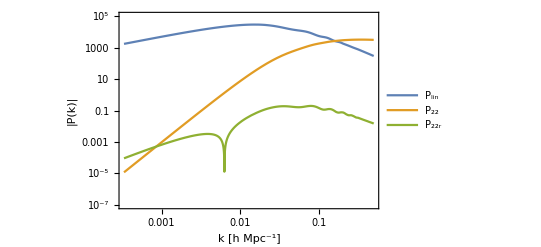

```mathematica
LogLogPlot[{Plin[k],Abs[P22[k]],Abs[P22r[k]]},{k,Subscript[h, 0],0.5},Frame->True,PlotRange->{{Subscript[h, 0],0.5},{10^-7,10^5}},FrameLabel->{"k [h \!\(\*SuperscriptBox[\(Mpc\), \(-1\)]\)]","|P(k)|"},FrameStyle->Directive[Thickness[0.001],Black,FontSize->16],PlotLegends->Placed[LineLegend[{"\!\(\*SubscriptBox[\(P\), \(lin\)]\)","\!\(\*SubscriptBox[\(P\), \(22\)]\)","\!\(\*SubscriptBox[\(P\), \(22r\)]\)"}],{0.85,0.2}]]
```

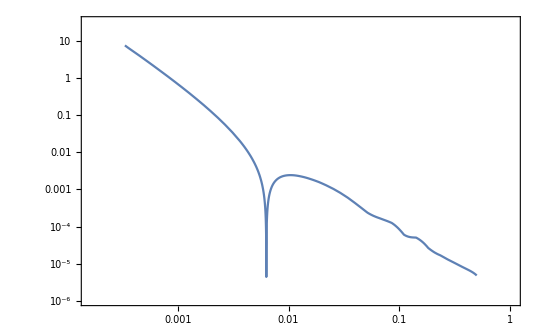

```mathematica
LogLogPlot[{Abs[P22r[k]]/P22[k]},{k,Subscript[h, 0],0.5},Frame->True]
```

#### determining the cutoff (to be done)

```mathematica
test=integrand/.k-> 10^-1;
qmin=10^-n;
qmax=10^(m-1);
```

```mathematica
Table[{m-1,NIntegrate[test,{θa,0,Pi},{q,qmin/.n-> 4,qmax}]},{m,0,10,2}]
```

NIntegrate::inumr: The integrand integrand has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.14159}, {1/10000, 1/10}}.

NIntegrate::inumr: The integrand integrand has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.14159}, {1/10000, 10}}.

NIntegrate::inumr: The integrand integrand has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.14159}, {1/10000, 1000}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::nlim: q = 10.^-1. + m is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{{-1,NIntegrate[test,{θa,0,π},{q,qmin/.n→4,qmax}]},{1,NIntegrate[test,{θa,0,π},{q,qmin/.n→4,qmax}]},{3,NIntegrate[test,{θa,0,π},{q,qmin/.n→4,qmax}]},{5,NIntegrate[test,{θa,0,π},{q,qmin/.n→4,qmax}]},{7,NIntegrate[test,{θa,0,π},{q,qmin/.n→4,qmax}]},{9,NIntegrate[test,{θa,0,π},{q,qmin/.n→4,qmax}]}}

conclusion : Qmin=10^-4 Qmax=1

```mathematica
Table[{n,NIntegrate[renormtest,{θa,0,Pi},{q,qmin,qmax}]},{n,0,10,2}]
```

NIntegrate::nlim: q = 10.^-1. + m is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{{0,NIntegrate[renormtest,{θa,0,π},{q,qmin,qmax}]},{2,NIntegrate[renormtest,{θa,0,π},{q,qmin,qmax}]},{4,NIntegrate[renormtest,{θa,0,π},{q,qmin,qmax}]},{6,NIntegrate[renormtest,{θa,0,π},{q,qmin,qmax}]},{8,NIntegrate[renormtest,{θa,0,π},{q,qmin,qmax}]},{10,NIntegrate[renormtest,{θa,0,π},{q,qmin,qmax}]}}

### P13 and P13R

2-HeavisideTheta[-1+t]+HeavisideTheta[1+t]

#### Brute force integration

```mathematica
integrand13=6*q^2(2 π)/(2 π)^3 Sin[θa]preinf3*Plin[q]*Plin[k];
totintegrandrenorm=6*Subscript[h, 0]^2*q^2(2 π)/(2 π)^3 Sin[θa]*(preinf3r+3/k^2*preinf3-renomadd)*Plin[q]*Plin[k];
```

```mathematica
put=ParallelTable[{k,NIntegrate[integrand13,{q,lowercutof,uppercutof},{θa,0,Pi}]},{k,kn}]

ListLogLogPlot[put];
P13=Interpolation[put]
```

$Aborted

InterpolatingFunction[{{0.000333333, 1.}}, <>]

```mathematica
preinf3
```

1/9+Cos[θa]^2/54-(7 k^2 Cos[θa]^2)/(54 q^2)-k^2/(63 (k^2+q^2-2 k q Cos[θa]))-q^2/(18 (k^2+q^2-2 k q Cos[θa]))+(13 k^3 Cos[θa])/(378 q (k^2+q^2-2 k q Cos[θa]))+(5 k q Cos[θa])/(36 (k^2+q^2-2 k q Cos[θa]))+(7 q^3 Cos[θa])/(108 k (k^2+q^2-2 k q Cos[θa]))-(79 k^2 Cos[θa]^2)/(756 (k^2+q^2-2 k q Cos[θa]))-(k^4 Cos[θa]^2)/(54 q^2 (k^2+q^2-2 k q Cos[θa]))-(5 q^2 Cos[θa]^2)/(36 (k^2+q^2-2 k q Cos[θa]))+(4 k^3 Cos[θa]^3)/(189 q (k^2+q^2-2 k q Cos[θa]))+(2 k q Cos[θa]^3)/(27 (k^2+q^2-2 k q Cos[θa]))-k^2/(63 (k^2+q^2+2 k q Cos[θa]))-q^2/(18 (k^2+q^2+2 k q Cos[θa]))-(13 k^3 Cos[θa])/(378 q (k^2+q^2+2 k q Cos[θa]))-(5 k q Cos[θa])/(36 (k^2+q^2+2 k q Cos[θa]))-(7 q^3 Cos[θa])/(108 k (k^2+q^2+2 k q Cos[θa]))-(79 k^2 Cos[θa]^2)/(756 (k^2+q^2+2 k q Cos[θa]))-(k^4 Cos[θa]^2)/(54 q^2 (k^2+q^2+2 k q Cos[θa]))-(5 q^2 Cos[θa]^2)/(36 (k^2+q^2+2 k q Cos[θa]))-(4 k^3 Cos[θa]^3)/(189 q (k^2+q^2+2 k q Cos[θa]))-(2 k q Cos[θa]^3)/(27 (k^2+q^2+2 k q Cos[θa]))

```mathematica
NIntegrate[totintegrandrenorm/.k->0.001,{q,lowercutof,uppercutof},{θa,0,Pi}]
```

-12.8064

```mathematica
puter=ParallelTable[{k,NIntegrate[totintegrandrenorm,{q,lowercutof,uppercutof},{θa,0,Pi}]},{k,kn}]

ListLogLogPlot[puter];
P13er=Interpolation[puter]
```

{{0.000333333,-4.51963},{0.000392501,-5.28687},{0.00046217,-6.18181},{0.000544206,-7.22423},{0.000640804,-8.43671},{0.000754548,-9.84355},{0.000888482,-11.4726},{0.00104619,-13.3532},{0.00123189,-15.5153},{0.00145055,-17.9908},{0.00170803,-20.8079},{0.00201121,-23.9927},{0.0023682,-27.5618},{0.00278856,-31.5221},{0.00328354,-35.8612},{0.00386637,-40.5428},{0.00455266,-45.4941},{0.00536077,-50.6111},{0.00631231,-55.734},{0.00743276,-60.6427},{0.00875209,-65.061},{0.0103056,-68.6452},{0.0121349,-70.9974},{0.0142888,-71.7004},{0.0168251,-70.7232},{0.0198116,-67.226},{0.0233282,-61.2385},{0.027469,-53.8132},{0.0323449,-45.4363},{0.0380861,-37.4346},{0.0448465,-31.0352},{0.0528068,-26.5676},{0.0621802,-23.1396},{0.0732173,-18.9426},{0.0862135,-13.799},{0.101517,-10.0345},{0.119536,-8.34408},{0.140754,-6.16754},{0.165738,-4.33079},{0.195157,-3.36498},{0.229797,-2.33564},{0.270587,-1.68665},{0.318617,-1.21451},{0.375172,-0.853329},{0.441765,-0.595847},{0.52018,-0.413628},{0.612513,-0.285821},{0.721235,-0.196354},{0.849255,-0.134129},{1.,-0.0911383}}

InterpolatingFunction[{{0.000333333, 1.}}, <>]

#### Plots P13 :

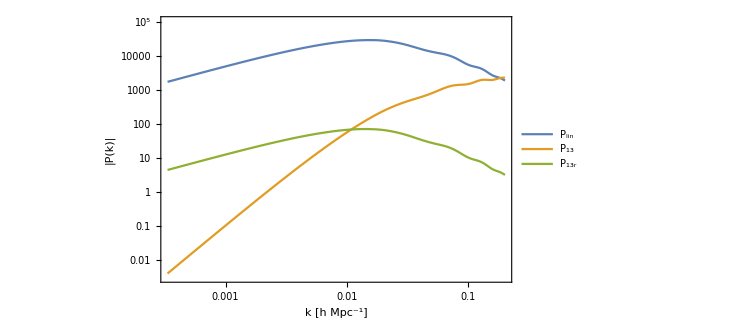

```mathematica
LogLogPlot[{Plin[k],Abs[P13[k]],Abs[P13er[k]]},{k,Subscript[h, 0],0.2},Frame->True,PlotRange->{{Subscript[h, 0],0.2},{10^-2.5,10^5}},FrameLabel->{"k [h \!\(\*SuperscriptBox[\(Mpc\), \(-1\)]\)]","|P(k)|"},FrameStyle->Directive[Thickness[0.001],Black,FontSize->16],PlotLegends->Placed[LineLegend[{"\!\(\*SubscriptBox[\(P\), \(lin\)]\)","\!\(\*SubscriptBox[\(P\),\(13\)]\)","\!\(\*SubscriptBox[\(P\), \(13r\)]\)"}],{0.85,0.2}]]
```

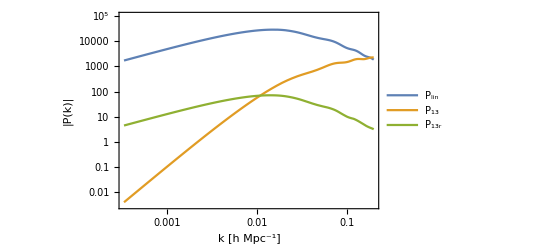

```mathematica
LogLogPlot[{Plin[k],Abs[P13[k]],Abs[P13er[k]]},{k,Subscript[h, 0],0.2},Frame->True,PlotRange->{{Subscript[h, 0],0.2},{10^-2.5,10^5}},FrameLabel->{"k [h \!\(\*SuperscriptBox[\(Mpc\), \(-1\)]\)]","|P(k)|"},FrameStyle->Directive[Thickness[0.001],Black,FontSize->16],PlotLegends->Placed[LineLegend[{"\!\(\*SubscriptBox[\(P\), \(lin\)]\)","\!\(\*SubscriptBox[\(P\),\(13\)]\)","\!\(\*SubscriptBox[\(P\), \(13r\)]\)"}],{0.85,0.2}]]
```

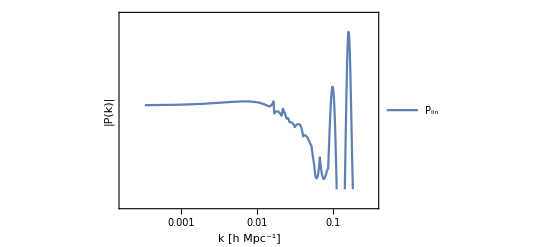

```mathematica
LogLogPlot[{1/(Plin[k]/Abs[P13er[k]])},{k,Subscript[h, 0],0.2},Frame->True,FrameLabel->{"k [h \!\(\*SuperscriptBox[\(Mpc\), \(-1\)]\)]","|P(k)|"},FrameStyle->Directive[Thickness[0.001],Black,FontSize->16],PlotLegends->Placed[LineLegend[{"\!\(\*SubscriptBox[\(P\), \(lin\)]\)","\!\(\*SubscriptBox[\(P\),\(13\)]\)","\!\(\*SubscriptBox[\(P\), \(13r\)]\)"}],{0.85,0.2}]]
```

### Final plot

```mathematica
P1loop=(P13[l]+P22[l])/.l-> κ;
P1loopr=(P13er[l]+P22r[l])/.l-> κ;
```

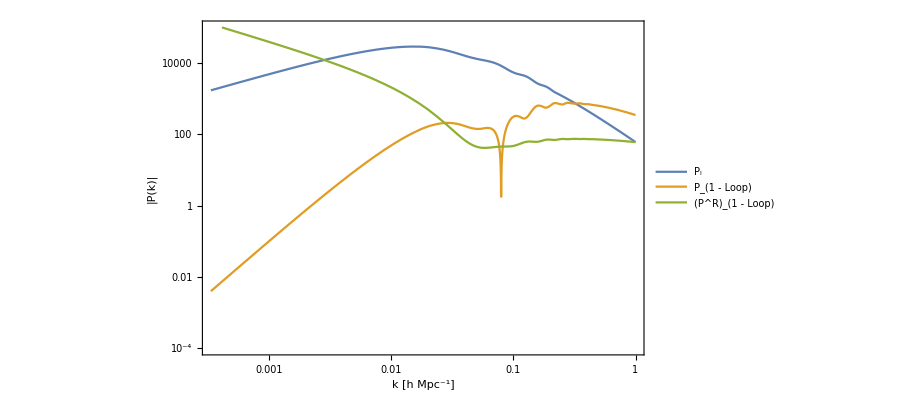

1loopPS.pdf

```mathematica
exportps=LogLogPlot[{Plin[κ],Abs[P1loop],Abs[P1loopr]},{κ,Subscript[h, 0],1},Frame->True,PlotRange->{{Subscript[h, 0],1},{10^-4,10^5}},FrameLabel->{"k [h \!\(\*SuperscriptBox[\(Mpc\), \(-1\)]\)]","|P(k)|"},FrameStyle->Directive[Thickness[0.001],Black,FontSize->14],PlotLegends->Placed[LineLegend[{"P_l","P_(1 - Loop)","(P^R)_(1 - Loop)"}],{0.85,0.25}],LabelStyle->{FontFamily->"Latin Modern Roman",14,GrayLevel[0]}]
Export["1loopPS.pdf",exportps]
```

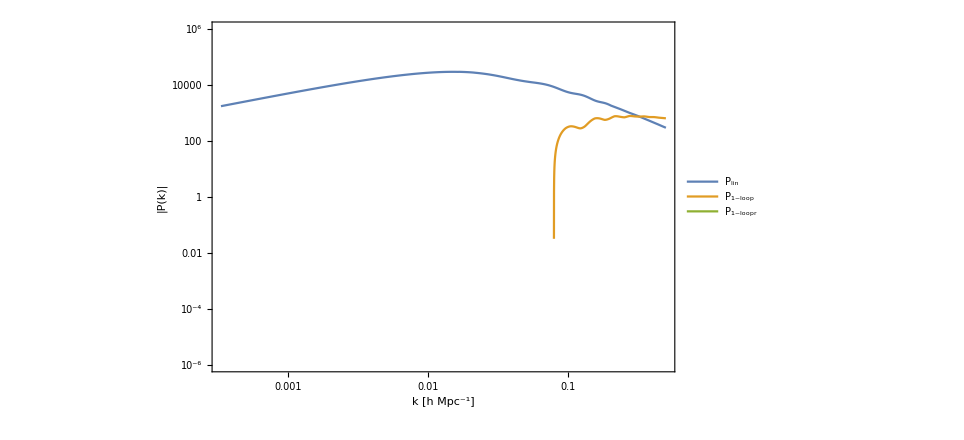

```mathematica
LogLogPlot[{Plin[κ],P1loop,P1loopr},{κ,Subscript[h, 0],0.5},Frame->True,PlotRange->{{Subscript[h, 0],0.5},{10^-6,10^6}},FrameLabel->{"k [h \!\(\*SuperscriptBox[\(Mpc\), \(-1\)]\)]","|P(k)|"},FrameStyle->Directive[Thickness[0.001],Black,FontSize->16],LabelStyle->Directive[16],PlotLegends->Placed[LineLegend[{"\!\(\*SubscriptBox[\(P\), \(lin\)]\)","\!\(\*SubscriptBox[\(P\),\(1-loop\)]\)","\!\(\*SubscriptBox[\(P\), \(1-loopr\)]\)"}],{0.85,0.2}]]
```

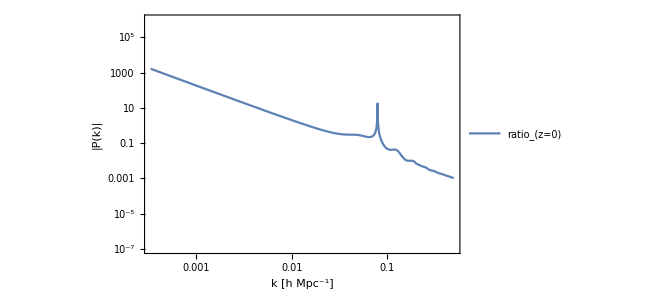

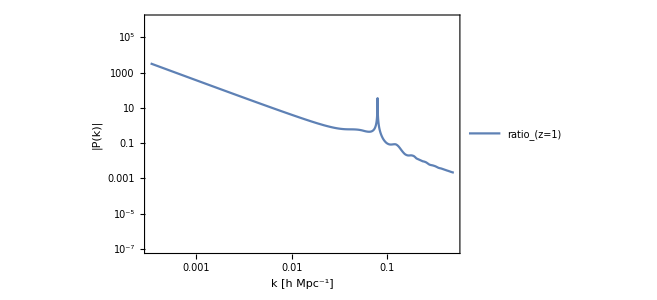

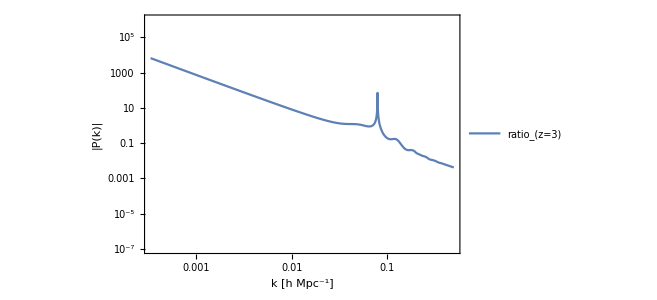

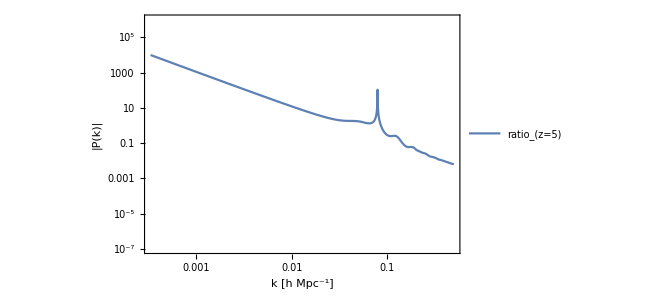

```mathematica
LogLogPlot[{Abs[P1loopr]/Abs[P1loop]},{κ,Subscript[h, 0],0.5},Frame->True,PlotRange->{{Subscript[h, 0],0.5},{10^-7,10^6}},FrameLabel->{"k [h \!\(\*SuperscriptBox[\(Mpc\), \(-1\)]\)]","|P(k)|"},FrameStyle->Directive[Thickness[0.001],Black,FontSize->16],PlotLegends->Placed[LineLegend[{"\!\(\*SubscriptBox[\(ratio\), \(z=0\)]\)","\!\(\*SubscriptBox[\(P\),\(1-loop\)]\)","\!\(\*SubscriptBox[\(P\), \(1-loopr\)]\)"}],{0.85,0.2}]]
LogLogPlot[{(1+1)Abs[P1loopr]/Abs[P1loop]},{κ,Subscript[h, 0],0.5},Frame->True,PlotRange->{{Subscript[h, 0],0.5},{10^-7,10^6}},FrameLabel->{"k [h \!\(\*SuperscriptBox[\(Mpc\), \(-1\)]\)]","|P(k)|"},FrameStyle->Directive[Thickness[0.001],Black,FontSize->16],PlotLegends->Placed[LineLegend[{"\!\(\*SubscriptBox[\(ratio\), \(z=1\)]\)","\!\(\*SubscriptBox[\(P\),\(1-loop\)]\)","\!\(\*SubscriptBox[\(P\), \(1-loopr\)]\)"}],{0.85,0.2}]]
LogLogPlot[{(1+3)Abs[P1loopr]/Abs[P1loop]},{κ,Subscript[h, 0],0.5},Frame->True,PlotRange->{{Subscript[h, 0],0.5},{10^-7,10^6}},FrameLabel->{"k [h \!\(\*SuperscriptBox[\(Mpc\), \(-1\)]\)]","|P(k)|"},FrameStyle->Directive[Thickness[0.001],Black,FontSize->16],PlotLegends->Placed[LineLegend[{"\!\(\*SubscriptBox[\(ratio\), \(z=3\)]\)","\!\(\*SubscriptBox[\(P\),\(1-loop\)]\)","\!\(\*SubscriptBox[\(P\), \(1-loopr\)]\)"}],{0.85,0.2}]]
LogLogPlot[{(1+5)Abs[P1loopr]/Abs[P1loop]},{κ,Subscript[h, 0],0.5},Frame->True,PlotRange->{{Subscript[h, 0],0.5},{10^-7,10^6}},FrameLabel->{"k [h \!\(\*SuperscriptBox[\(Mpc\), \(-1\)]\)]","|P(k)|"},FrameStyle->Directive[Thickness[0.001],Black,FontSize->16],PlotLegends->Placed[LineLegend[{"\!\(\*SubscriptBox[\(ratio\), \(z=5\)]\)","\!\(\*SubscriptBox[\(P\),\(1-loop\)]\)","\!\(\*SubscriptBox[\(P\), \(1-loopr\)]\)"}],{0.85,0.2}]]
```

### Compare with C code

```mathematica
SetDirectory["/home/clement/Documents/relativistic effects/codes/year 2"];
ploop=Import["out.dat"];
(*plindatsy=Import["Plinearsynchro.dat"];
plindat=Import["plinearnewton.dat"];
plindatnew=Import["Plinear.dat"];*)
ploop;
ass=ploop[[1,2]]
kbb=ploop[[2,1]]
plinc=Table[{ploop[[i,1]],ploop[[i,2]]},{i,1,Length[ploop]}];
pddd=Table[{ploop[[i,1]],ploop[[i,3]]},{i,1,Length[ploop]}];
puntrois=Table[{ploop[[i,1]],ploop[[i,4]]},{i,1,Length[ploop]}];
puntroisr=Table[{ploop[[i,1]],ploop[[i,5]]},{i,1,Length[ploop]}];
pdeuxdeuxr=Table[{ploop[[i,1]],ploop[[i,6]]},{i,1,Length[ploop]}];

pdddd=Interpolation[pddd]
putut=Interpolation[puntrois]

hey=Table[If[ploop[[i,6]]=!="-nan",{ploop[[i,1]],ploop[[i,6]]}],{i,1,Length[ploop]}];
coco=DeleteCases[hey,Null];
ListLogLogPlot[Abs[coco]];
ptutut=Interpolation[pdeuxdeuxr];
testouse=Interpolation[coco];

gropgrop=Interpolation[puntroisr]
```

4135.67

0.001002

InterpolatingFunction[{{0.001, 1.}}, <>]

InterpolatingFunction[{{0.001, 1.}}, <>]

InterpolatingFunction[{{0.001, 1.}}, <>]

```mathematica
LogLogPlot[{Abs[P13[k]],Abs[putut[k]]},{k,0.001,0.2}]
LogLogPlot[{Abs[P13[k]]/Abs[putut[k]]},{k,0.001,0.2}]
LogLogPlot[{Abs[P22[k]],Abs[pdddd[k]]},{k,0.001,0.2}]
LogLogPlot[{Abs[P22[k]]/Abs[pdddd[k]]},{k,0.001,0.2}]
LogLogPlot[{Abs[P22r[k]]/Subscript[h,0]^2,Abs[ptutut[k]]},{k,0.001,0.2}]
LogLogPlot[{Abs[P22r[k]]/Subscript[h,0]^2,Abs[testouse[k]]},{k,0.001,0.2}]
LogLogPlot[{(Abs[P22r[k]]/Subscript[h,0]^2)/Abs[testouse[k]]},{k,0.001,0.2}]
LogLogPlot[{Abs[P13er[k]],Subscript[h,0]^2 Abs[gropgrop[k]]},{k,0.001,0.2}]
LogLogPlot[{Abs[1/Subscript[h,0]^2 P13er[k]]/Abs[gropgrop[k]]},{k,0.001,0.2}]
```

### P22 and P22R lina

#### calculation of the integral :

```mathematica
preinf2
```

5/14+(5 k Cos[θa])/(14 q)-k^2/(7 (k^2+q^2-2 k q Cos[θa]))-(5 q^2)/(14 (k^2+q^2-2 k q Cos[θa]))+(k^3 Cos[θa])/(7 q (k^2+q^2-2 k q Cos[θa]))+(5 k q Cos[θa])/(14 (k^2+q^2-2 k q Cos[θa]))

```mathematica
integrand22=2*q^2(2 π)/(2 π)^3 Sin[θa](preinf2*preinf2*Plin[q]*Plin[mag[k-q]])/.rules2
relatintegrand22lina=2*2*Subscript[h, 0]^2*q^2(2 π)/(2 π)^3 Sin[θa](preinf2*preinf2rdlina*Plin[q]*Plin[mag[k-q]])/.rules2
```

1/(2 π^2)ⅇ^(-0.025 q-0.025 √(k^2+q^2-2 k q Cos[θa])+InterpolatingFunction[{{-23.0259, 6.90965}}, <>][Log[q]]+InterpolatingFunction[{{-23.0259, 6.90965}}, <>][Log[√(k^2+q^2-2 k q Cos[θa])]]) q^2 (5/14+(5 k Cos[θa])/(14 q)-k^2/(7 (k^2+q^2-2 k q Cos[θa]))-(5 q^2)/(14 (k^2+q^2-2 k q Cos[θa]))+(k^3 Cos[θa])/(7 q (k^2+q^2-2 k q Cos[θa]))+(5 k q Cos[θa])/(14 (k^2+q^2-2 k q Cos[θa])))^2 Sin[θa]

1/(9000000 π^2)ⅇ^(-0.025 q-0.025 √(k^2+q^2-2 k q Cos[θa])+InterpolatingFunction[{{-23.0259, 6.90965}}, <>][Log[q]]+InterpolatingFunction[{{-23.0259, 6.90965}}, <>][Log[√(k^2+q^2-2 k q Cos[θa])]]) q^2 (5/14+(5 k Cos[θa])/(14 q)-k^2/(7 (k^2+q^2-2 k q Cos[θa]))-(5 q^2)/(14 (k^2+q^2-2 k q Cos[θa]))+(k^3 Cos[θa])/(7 q (k^2+q^2-2 k q Cos[θa]))+(5 k q Cos[θa])/(14 (k^2+q^2-2 k q Cos[θa]))) (-(5 k^2)/(2 (q^2 Cos[θa]^2+q^2 (1-Cos[θa]^2)) ((k-q Cos[θa])^2+q^2 (1-Cos[θa]^2)))-(25 q^2)/(4 (q^2 Cos[θa]^2+q^2 (1-Cos[θa]^2)) ((k-q Cos[θa])^2+q^2 (1-Cos[θa]^2)))+(25 k q Cos[θa])/(4 (q^2 Cos[θa]^2+q^2 (1-Cos[θa]^2)) ((k-q Cos[θa])^2+q^2 (1-Cos[θa]^2)))) Sin[θa]

```mathematica
integrand22/.k-> 1/.q-> 1/.θa-> 1
```

15.7871

```mathematica
pdd=ParallelTable[{k,NIntegrate[integrand22,{q,lowercutof,uppercutof},{θa,0,Pi}]},{k,kn}]

ListLogLogPlot[pdd];
P22=Interpolation[pdd]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{{0.000333333,0.0000118688},{0.000361411,0.0000163982},{0.000391853,0.0000226555},{0.00042486,0.0000312996},{0.000460647,0.0000432401},{0.000499449,0.0000597335},{0.000541519,0.0000825144},{0.000587132,0.000113978},{0.000636588,0.00015743},{0.000690209,0.000217434},{0.000748347,0.000300287},{0.000811382,0.000414678},{0.000879727,0.000572595},{0.000953829,0.000790571},{0.00103417,0.0010914},{0.00112128,0.00150651},{0.00121573,0.0020792},{0.00131814,0.00286912},{0.00142917,0.00395838},{0.00154955,0.00546003},{0.00168007,0.0075295},{0.00182159,0.0103805},{0.00197502,0.0143064},{0.00214139,0.0197102},{0.00232176,0.027144},{0.00251733,0.0373643},{0.00272937,0.0514061},{0.00295927,0.070683},{0.00320854,0.0971238},{0.0034788,0.133355},{0.00377183,0.182946},{0.00408954,0.250737},{0.00443401,0.34328},{0.0048075,0.469409},{0.00521245,0.64101},{0.0056515,0.874014},{0.00612754,1.18969},{0.00664368,1.61633},{0.0072033,2.19133},{0.00781005,2.96394},{0.00846791,3.99853},{0.00918118,5.37872},{0.00995454,7.21227},{0.010793,9.63682},{0.0117022,12.8264},{0.0126879,16.9984},{0.0137566,22.4213},{0.0149153,29.4206},{0.0161717,38.3844},{0.0175339,49.7688},{0.0190108,64.1025},{0.0206121,81.9625},{0.0223484,103.961},{0.0242308,130.699},{0.0262718,162.771},{0.0284848,200.727},{0.0308841,245.012},{0.0334856,295.942},{0.0363061,353.734},{0.0393643,418.555},{0.0426801,490.651},{0.0462751,570.56},{0.050173,659.279},{0.0543992,758.244},{0.0589813,869.114},{0.0639495,993.355},{0.0693361,1130.92},{0.0751765,1279.19},{0.0815088,1432.54},{0.0883745,1583.93},{0.0958185,1728.55},{0.10389,1867.63},{0.11264,2008.4},{0.122128,2158.12},{0.132416,2314.48},{0.143569,2461.26},{0.155662,2585.05},{0.168774,2692.91},{0.182991,2802.61},{0.198404,2909.91},{0.215116,2993.31},{0.233236,3057.32},{0.252882,3118.94},{0.274183,3164.45},{0.297278,3191.17},{0.322319,3210.72},{0.349469,3213.71},{0.378905,3206.27},{0.410822,3186.87},{0.445426,3157.43},{0.482945,3118.15},{0.523625,3070.58},{0.567731,3015.26},{0.615553,2953.35},{0.667402,2885.79},{0.723619,2813.47},{0.784572,2737.2},{0.850658,2657.76},{0.922311,2575.92},{1.,2492.3}}

InterpolatingFunction[{{0.000333333, 1.}}, <>]

```mathematica
relatintegrand22lina/.k-> 1/.q-> 1/.θa-> 1
```

-0.0000683181

```mathematica
(*pddrlina=ParallelTable[{k,NIntegrate[relatintegrand22lina,{q,lowercutof,uppercutof},{θa,0,Pi}]},{k,kn}]*)
pddrlina={{0.000333333,0.0000604904},{0.000361411,0.0000696133},{0.000391853,0.0000799461},{0.00042486,0.0000916005},{0.000460647,0.000104682},{0.000499449,0.000119285},{0.000541519,0.000135472},{0.000587132,0.000153284},{0.000636588,0.000172676},{0.000690209,0.000193579},{0.000748347,0.000215737},{0.000811382,0.000238794},{0.000879727,0.000262114},{0.000953829,0.000284914},{0.00103417,0.000305933},{0.00112128,0.000323446},{0.00121573,0.000335108},{0.00131814,0.00033792},{0.00142917,0.000327561},{0.00154955,0.000298745},{0.00168007,0.000244474},{0.00182159,0.000155625},{0.00197502,0.0000206942},{0.00214139,-0.000174984},{0.00232176,-0.000449661},{0.00251733,-0.00082663},{0.00272937,-0.0013345},{0.00295927,-0.00200802},{0.00320854,-0.00289172},{0.0034788,-0.00403668},{0.00377183,-0.00551269},{0.00408954,-0.00738292},{0.00443401,-0.00975249},{0.0048075,-0.0127261},{0.00521245,-0.016429},{0.0056515,-0.0210103},{0.00612754,-0.0266412},{0.00664368,-0.0335178},{0.0072033,-0.041851},{0.00781005,-0.0518882},{0.00846791,-0.0638793},{0.00918118,-0.0781077},{0.00995454,-0.0948498},{0.010793,-0.114386},{0.0117022,-0.136946},{0.0126879,-0.162784},{0.0137566,-0.191992},{0.0149153,-0.224599},{0.0161717,-0.260418},{0.0175339,-0.299773},{0.0190108,-0.34185},{0.0206121,-0.385723},{0.0223484,-0.429581},{0.0242308,-0.471997},{0.0262718,-0.511674},{0.0284848,-0.547207},{0.0308841,-0.576023},{0.0334856,-0.596569},{0.0363061,-0.607751},{0.0393643,-0.609177},{0.0426801,-0.602202},{0.0462751,-0.590014},{0.050173,-0.576595},{0.0543992,-0.56626},{0.0589813,-0.563569},{0.0639495,-0.570435},{0.0693361,-0.58275},{0.0751765,-0.59121},{0.0815088,-0.583212},{0.0883745,-0.55043},{0.0958185,-0.495295},{0.10389,-0.433633},{0.11264,-0.387687},{0.122128,-0.371513},{0.132416,-0.370711},{0.143569,-0.351363},{0.155662,-0.301861},{0.168774,-0.250894},{0.182991,-0.230721},{0.198404,-0.223738},{0.215116,-0.193522},{0.233236,-0.159372},{0.252882,-0.147898},{0.274183,-0.130918},{0.297278,-0.10836},{0.322319,-0.0982185},{0.349469,-0.0828801},{0.378905,-0.0719418},{0.410822,-0.0612333},{0.445426,-0.052588},{0.482945,-0.044467},{0.523625,-0.0379054},{0.567731,-0.0320406},{0.615553,-0.0270304},{0.667402,-0.0227421},{0.723619,-0.0190997},{0.784572,-0.0159989},{0.850658,-0.0133666},{0.922311,-0.0111563},{1.,-0.00928464}}
ListLogLogPlot[{pdd,pddrlina}];
P22rlina=Interpolation[pddrlina]
```

{{0.000333333,0.0000604904},{0.000361411,0.0000696133},{0.000391853,0.0000799461},{0.00042486,0.0000916005},{0.000460647,0.000104682},{0.000499449,0.000119285},{0.000541519,0.000135472},{0.000587132,0.000153284},{0.000636588,0.000172676},{0.000690209,0.000193579},{0.000748347,0.000215737},{0.000811382,0.000238794},{0.000879727,0.000262114},{0.000953829,0.000284914},{0.00103417,0.000305933},{0.00112128,0.000323446},{0.00121573,0.000335108},{0.00131814,0.00033792},{0.00142917,0.000327561},{0.00154955,0.000298745},{0.00168007,0.000244474},{0.00182159,0.000155625},{0.00197502,0.0000206942},{0.00214139,-0.000174984},{0.00232176,-0.000449661},{0.00251733,-0.00082663},{0.00272937,-0.0013345},{0.00295927,-0.00200802},{0.00320854,-0.00289172},{0.0034788,-0.00403668},{0.00377183,-0.00551269},{0.00408954,-0.00738292},{0.00443401,-0.00975249},{0.0048075,-0.0127261},{0.00521245,-0.016429},{0.0056515,-0.0210103},{0.00612754,-0.0266412},{0.00664368,-0.0335178},{0.0072033,-0.041851},{0.00781005,-0.0518882},{0.00846791,-0.0638793},{0.00918118,-0.0781077},{0.00995454,-0.0948498},{0.010793,-0.114386},{0.0117022,-0.136946},{0.0126879,-0.162784},{0.0137566,-0.191992},{0.0149153,-0.224599},{0.0161717,-0.260418},{0.0175339,-0.299773},{0.0190108,-0.34185},{0.0206121,-0.385723},{0.0223484,-0.429581},{0.0242308,-0.471997},{0.0262718,-0.511674},{0.0284848,-0.547207},{0.0308841,-0.576023},{0.0334856,-0.596569},{0.0363061,-0.607751},{0.0393643,-0.609177},{0.0426801,-0.602202},{0.0462751,-0.590014},{0.050173,-0.576595},{0.0543992,-0.56626},{0.0589813,-0.563569},{0.0639495,-0.570435},{0.0693361,-0.58275},{0.0751765,-0.59121},{0.0815088,-0.583212},{0.0883745,-0.55043},{0.0958185,-0.495295},{0.10389,-0.433633},{0.11264,-0.387687},{0.122128,-0.371513},{0.132416,-0.370711},{0.143569,-0.351363},{0.155662,-0.301861},{0.168774,-0.250894},{0.182991,-0.230721},{0.198404,-0.223738},{0.215116,-0.193522},{0.233236,-0.159372},{0.252882,-0.147898},{0.274183,-0.130918},{0.297278,-0.10836},{0.322319,-0.0982185},{0.349469,-0.0828801},{0.378905,-0.0719418},{0.410822,-0.0612333},{0.445426,-0.052588},{0.482945,-0.044467},{0.523625,-0.0379054},{0.567731,-0.0320406},{0.615553,-0.0270304},{0.667402,-0.0227421},{0.723619,-0.0190997},{0.784572,-0.0159989},{0.850658,-0.0133666},{0.922311,-0.0111563},{1.,-0.00928464}}

InterpolatingFunction[{{0.000333333, 1.}}, <>]

#### Plots P22 :

```mathematica
LogLogPlot[{Plin[k],Abs[P22[k]],Abs[P22r[k]]},{k,Subscript[h, 0],0.5},Frame->True,PlotRange->{{Subscript[h, 0],0.5},{10^-7,10^5}},FrameLabel->{"k [h \!\(\*SuperscriptBox[\(Mpc\), \(-1\)]\)]","|P(k)|"},FrameStyle->Directive[Thickness[0.001],Black,FontSize->16],PlotLegends->Placed[LineLegend[{"\!\(\*SubscriptBox[\(P\), \(lin\)]\)","\!\(\*SubscriptBox[\(P\), \(22\)]\)","\!\(\*SubscriptBox[\(P\), \(22r\)]\)"}],{0.85,0.2}]]
```

-Graphics-

```mathematica
LogLogPlot[{Abs[P22r[k]]/P22[k]},{k,Subscript[h, 0],0.5},Frame->True]
```

-Graphics-

#### determining the cutoff (to be done)

```mathematica
test=integrand/.k-> 10^-1;
qmin=10^-n;
qmax=10^(m-1);
```

```mathematica
Table[{m-1,NIntegrate[test,{θa,0,Pi},{q,qmin/.n-> 4,qmax}]},{m,0,10,2}]
```

NIntegrate::inumr: The integrand integrand has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.14159}, {1/10000, 1/10}}.

NIntegrate::inumr: The integrand integrand has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.14159}, {1/10000, 10}}.

NIntegrate::inumr: The integrand integrand has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 3.14159}, {1/10000, 1000}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::nlim: q = 10.^-1. + m is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{{-1,NIntegrate[test,{θa,0,π},{q,qmin/.n→4,qmax}]},{1,NIntegrate[test,{θa,0,π},{q,qmin/.n→4,qmax}]},{3,NIntegrate[test,{θa,0,π},{q,qmin/.n→4,qmax}]},{5,NIntegrate[test,{θa,0,π},{q,qmin/.n→4,qmax}]},{7,NIntegrate[test,{θa,0,π},{q,qmin/.n→4,qmax}]},{9,NIntegrate[test,{θa,0,π},{q,qmin/.n→4,qmax}]}}

conclusion : Qmin=10^-4 Qmax=1

```mathematica
Table[{n,NIntegrate[renormtest,{θa,0,Pi},{q,qmin,qmax}]},{n,0,10,2}]
```

NIntegrate::nlim: q = 10.^-1. + m is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{{0,NIntegrate[renormtest,{θa,0,π},{q,qmin,qmax}]},{2,NIntegrate[renormtest,{θa,0,π},{q,qmin,qmax}]},{4,NIntegrate[renormtest,{θa,0,π},{q,qmin,qmax}]},{6,NIntegrate[renormtest,{θa,0,π},{q,qmin,qmax}]},{8,NIntegrate[renormtest,{θa,0,π},{q,qmin,qmax}]},{10,NIntegrate[renormtest,{θa,0,π},{q,qmin,qmax}]}}

### Final plot

```mathematica
P1loop=(P13[l]+P22[l])/.l-> κ;
P1looprlina=(P13erlina[l]+P22rlina[l])/.l-> κ;
```

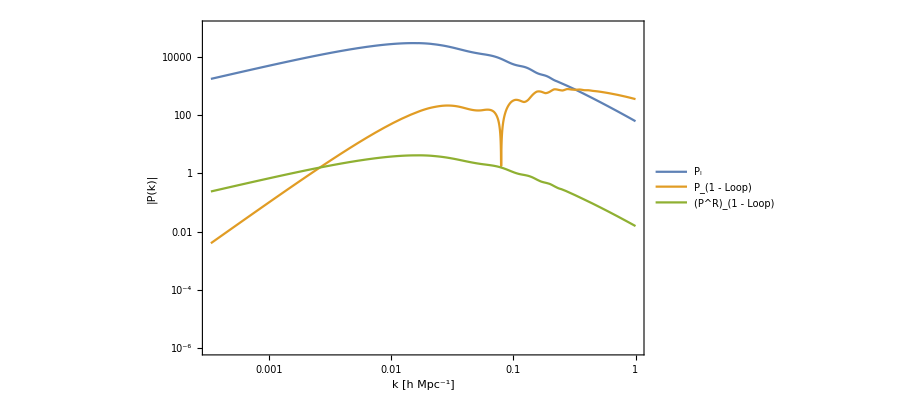

1loopPSlina.pdf

```mathematica
exportpslina=LogLogPlot[{Plin[κ],Abs[P1loop],Abs[P1looprlina]},{κ,Subscript[h, 0],1},Frame->True,PlotRange->{{Subscript[h, 0],1},{10^-6,10^5}},FrameLabel->{"k [h \!\(\*SuperscriptBox[\(Mpc\), \(-1\)]\)]","|P(k)|"},FrameStyle->Directive[Thickness[0.001],Black,FontSize->14],PlotLegends->Placed[LineLegend[{"P_l","P_(1 - Loop)","(P^R)_(1 - Loop)"}],{0.85,0.25}],LabelStyle->{FontFamily->"Latin Modern Roman",14,GrayLevel[0]}]
Export["1loopPSlina.pdf",exportpslina]
```

```mathematica
LogLogPlot[{Plin[κ],P1loop,P1loopr},{κ,Subscript[h, 0],0.5},Frame->True,PlotRange->{{Subscript[h, 0],0.5},{10^-6,10^6}},FrameLabel->{"k [h \!\(\*SuperscriptBox[\(Mpc\), \(-1\)]\)]","|P(k)|"},FrameStyle->Directive[Thickness[0.001],Black,FontSize->16],LabelStyle->Directive[16],PlotLegends->Placed[LineLegend[{"\!\(\*SubscriptBox[\(P\), \(lin\)]\)","\!\(\*SubscriptBox[\(P\),\(1-loop\)]\)","\!\(\*SubscriptBox[\(P\), \(1-loopr\)]\)"}],{0.85,0.2}]]
```

-Graphics-

```mathematica
LogLogPlot[{Abs[P1loopr]/Abs[P1loop]},{κ,Subscript[h, 0],0.5},Frame->True,PlotRange->{{Subscript[h, 0],0.5},{10^-7,10^6}},FrameLabel->{"k [h \!\(\*SuperscriptBox[\(Mpc\), \(-1\)]\)]","|P(k)|"},FrameStyle->Directive[Thickness[0.001],Black,FontSize->16],PlotLegends->Placed[LineLegend[{"\!\(\*SubscriptBox[\(ratio\), \(z=0\)]\)","\!\(\*SubscriptBox[\(P\),\(1-loop\)]\)","\!\(\*SubscriptBox[\(P\), \(1-loopr\)]\)"}],{0.85,0.2}]]
LogLogPlot[{(1+1)Abs[P1loopr]/Abs[P1loop]},{κ,Subscript[h, 0],0.5},Frame->True,PlotRange->{{Subscript[h, 0],0.5},{10^-7,10^6}},FrameLabel->{"k [h \!\(\*SuperscriptBox[\(Mpc\), \(-1\)]\)]","|P(k)|"},FrameStyle->Directive[Thickness[0.001],Black,FontSize->16],PlotLegends->Placed[LineLegend[{"\!\(\*SubscriptBox[\(ratio\), \(z=1\)]\)","\!\(\*SubscriptBox[\(P\),\(1-loop\)]\)","\!\(\*SubscriptBox[\(P\), \(1-loopr\)]\)"}],{0.85,0.2}]]
LogLogPlot[{(1+3)Abs[P1loopr]/Abs[P1loop]},{κ,Subscript[h, 0],0.5},Frame->True,PlotRange->{{Subscript[h, 0],0.5},{10^-7,10^6}},FrameLabel->{"k [h \!\(\*SuperscriptBox[\(Mpc\), \(-1\)]\)]","|P(k)|"},FrameStyle->Directive[Thickness[0.001],Black,FontSize->16],PlotLegends->Placed[LineLegend[{"\!\(\*SubscriptBox[\(ratio\), \(z=3\)]\)","\!\(\*SubscriptBox[\(P\),\(1-loop\)]\)","\!\(\*SubscriptBox[\(P\), \(1-loopr\)]\)"}],{0.85,0.2}]]
LogLogPlot[{(1+5)Abs[P1loopr]/Abs[P1loop]},{κ,Subscript[h, 0],0.5},Frame->True,PlotRange->{{Subscript[h, 0],0.5},{10^-7,10^6}},FrameLabel->{"k [h \!\(\*SuperscriptBox[\(Mpc\), \(-1\)]\)]","|P(k)|"},FrameStyle->Directive[Thickness[0.001],Black,FontSize->16],PlotLegends->Placed[LineLegend[{"\!\(\*SubscriptBox[\(ratio\), \(z=5\)]\)","\!\(\*SubscriptBox[\(P\),\(1-loop\)]\)","\!\(\*SubscriptBox[\(P\), \(1-loopr\)]\)"}],{0.85,0.2}]]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-